Probabilities

```mathematica
detect[ro_,sig_,K_]:=1-N[Binomial[K (1-ro),sig K]/Binomial[K,sig K]]
newDetect[ro_,sig_,K1_,K2_]:=1-N[Binomial[K1 (1-ro),sig K1]/Binomial[K1,sig K1] Binomial[K2 (1-ro),sig K2]/Binomial[K2,sig K2]]
SGDDetect[ro_,sig_,K_,n_]:=1-N[Binomial[K (1-ro),sig K]/Binomial[K,sig K]]^n
getSig[ro_,K_,x_]:=Module[{sig=N[1/K]},While[detect[ro,sig,K]<N[(1+x)^(-1)],sig+=1/K];sig]
getNewSig[ro_,K1_,K2_,x_]:=Module[{sig=N[100/(K1+K2)]},While[newDetect[ro,sig,K1,K2]<N[(1+x)^(-1)],sig+=10/(K1+K2)];sig]
getSGDSig[ro_,K_,n_,x_]:=Module[{sig=N[1/K]},While[SGDDetect[ro,sig,K,n]<N[(1+x)^(-1)],sig+=1/K];sig]
```

```mathematica
payoffC[theta_,ro_,x_]:=Module[{sig=getSig[theta,1000000,x]},{N[sig],detect[ro,sig,1000000],detect[ro,sig,1000000] (-sig)+(1-detect[ro,sig,1000000]) (0.1-x-sig)}]
payoffS[theta_,ro_,x_]:=Module[{sig=getSig[theta,1000000,x]},{detect[ro,sig,1000000],detect[ro,sig,1000000] (ro-1)+(1-detect[ro,sig,1000000]) (x+ro)}]
```

Verification costs WSO

```mathematica
y[x_,x1_,y1_,x2_, y2_]:=(x y1-x2 y1-x y2+x1 y2)/(x1-x2)
Vd[x_,data_]:=If[data==1,
If[x>0 && x≤0.000001,y[x,0,0,0.000001,6.9/2649],
If[x>0.000001 && x≤0.00001,y[x,0.000001,6.9/2649,0.00001,63.7/2649],
If[x>0.00001 && x≤0.0001,y[x,0.00001,63.7/2649,0.0001,492/2649],
If[x>0.0001 && x≤0.001,y[x,0.0001,492/2649,0.001,1077/2649],
If[x>0.001 && x≤0.01,y[x,0.001,1077/2649,0.01,1090/2649],
If[x>0.01 && x≤0.1,y[x,0.01,1090/2649,0.1,1254/2649],
If[x>0.1 && x≤1,y[x,0.1,1254/2649,1,2649/2649]]]]]]]],
If[x>0 && x≤0.0001,y[x,0,0,0.0001,3.1/102],
If[x>0.0001 && x≤0.001,y[x,0.0001,3.1/102,0.001,20.9/102],
If[x>0.001 && x≤0.01,y[x,0.001,20.9/102,0.01,37.2/102],
If[x>0.01 && x≤0.1,y[x,0.01,37.2/102,0.1,42.6/102],
If[x>0.1 && x≤1,y[x,0.1,42.6/102,1,102/102]]]]]]]
```

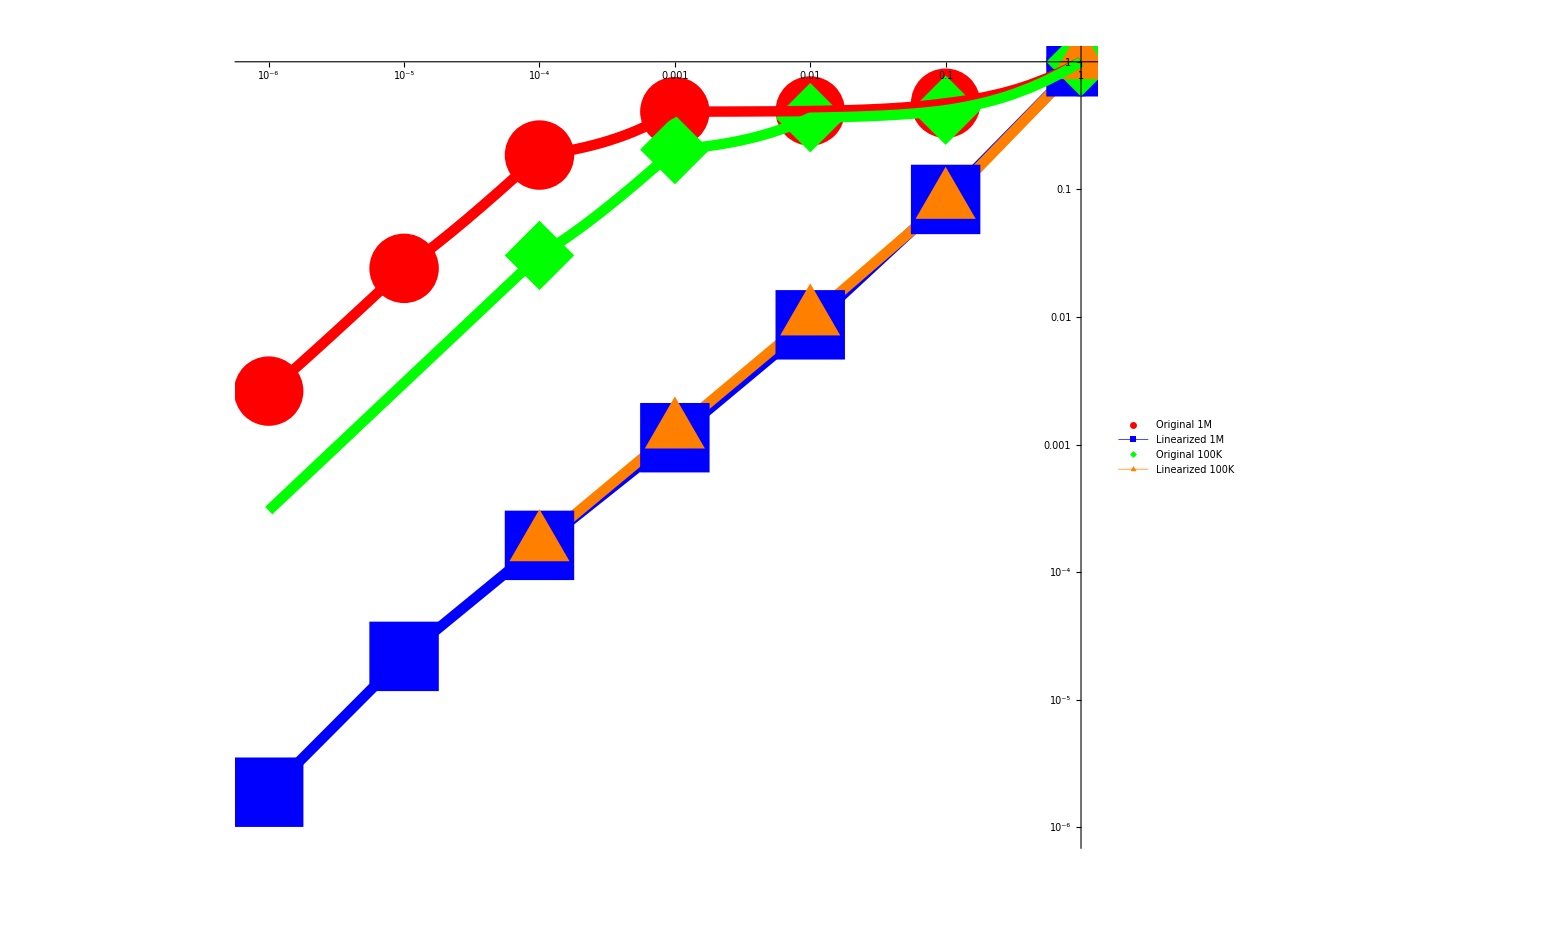

```mathematica
Show[ListLogLogPlot[
{{{0,0},{0.000001,6.953/2649},{0.00001,63.7/2649},{0.0001,492/2649},{0.001,1077/2649},{0.01,1090/2649},{0.1,1254/2649},{1,1}},
{{0,0},{0.000001,0.005/2650},{0.00001,0.058/2650},{0.0001,0.43/2650},{0.001,3/2650},{0.01,23/2650},{0.1,221/2650},{1,1}},
{{0,0},{0.0001,3.1/102},{0.001,20.9/102},{0.01,37.2/102},{0.1,42.6/102},{1,1}},
{{0,0},{0.0001,0.017/102},{0.001,0.13/102},{0.01,1/102},{0.1,8.2/102},{1,1}}},
 PlotLegends->Placed[PointLegend[{Text[Style["Original 1M",FontSize->24]],Text[Style["Linearized 1M",FontSize->24]],Text[Style["Original 100K",FontSize->24]],Text[Style["Linearized 100K",FontSize->24]]},LegendMarkerSize->100,LegendFunction->Frame],{0.8,0.33}],Joined->{False,True,False,True},Mesh->All,  PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]},{Green,Thickness[0.005]},{Orange,Thickness[0.005]}}, AxesOrigin->{1,1},PlotMarkers-> {Automatic,75},ImageSize->1500],
LogLogPlot[Vd[x,1],{x,0.000001,01}, PlotStyle->Directive[Red,Thickness[0.005]], ImageSize->1500],
LogLogPlot[Vd[x,100],{x,0.000001,01}, PlotStyle->Directive[Green,Thickness[0.005]], ImageSize->1500]]
```

Fictional case

```mathematica
MatrixForm[Table[Module[{sig=getSig[0.001,1000000,x]},{x,sig,sig+x}],{x,0.0005,0.0015,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.0001,1000000,x]},{x,sig,sig+x}],{x,0.009,0.01,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.00001,1000000,x]},{x,sig,sig+x}],{x,0.071,0.072,0.00001}]]
```

(0.0005 | 0.007569 | 0.008069
0.00051 | 0.00755 | 0.00806
0.00052 | 0.00753 | 0.00805
0.00053 | 0.007512 | 0.008042
0.00054 | 0.007493 | 0.008033
0.00055 | 0.007475 | 0.008025
0.00056 | 0.007457 | 0.008017
0.00057 | 0.007439 | 0.008009
0.00058 | 0.007422 | 0.008002
0.00059 | 0.007405 | 0.007995
0.0006 | 0.007389 | 0.007989
0.00061 | 0.007372 | 0.007982
0.00062 | 0.007356 | 0.007976
0.00063 | 0.00734 | 0.00797
0.00064 | 0.007325 | 0.007965
0.00065 | 0.007309 | 0.007959
0.00066 | 0.007294 | 0.007954
0.00067 | 0.007279 | 0.007949
0.00068 | 0.007264 | 0.007944
0.00069 | 0.00725 | 0.00794
0.0007 | 0.007236 | 0.007936
0.00071 | 0.007222 | 0.007932
0.00072 | 0.007208 | 0.007928
0.00073 | 0.007194 | 0.007924
0.00074 | 0.007181 | 0.007921
0.00075 | 0.007167 | 0.007917
0.00076 | 0.007154 | 0.007914
0.00077 | 0.007141 | 0.007911
0.00078 | 0.007128 | 0.007908
0.00079 | 0.007116 | 0.007906
0.0008 | 0.007103 | 0.007903
0.00081 | 0.007091 | 0.007901
0.00082 | 0.007079 | 0.007899
0.00083 | 0.007067 | 0.007897
0.00084 | 0.007055 | 0.007895
0.00085 | 0.007043 | 0.007893
0.00086 | 0.007032 | 0.007892
0.00087 | 0.00702 | 0.00789
0.00088 | 0.007009 | 0.007889
0.00089 | 0.006998 | 0.007888
0.0009 | 0.006986 | 0.007886
0.00091 | 0.006976 | 0.007886
0.00092 | 0.006965 | 0.007885
0.00093 | 0.006954 | 0.007884
0.00094 | 0.006943 | 0.007883
0.00095 | 0.006933 | 0.007883
0.00096 | 0.006922 | 0.007882
0.00097 | 0.006912 | 0.007882
0.00098 | 0.006902 | 0.007882
0.00099 | 0.006892 | 0.007882
0.001 | 0.006882 | 0.007882
0.00101 | 0.006872 | 0.007882
0.00102 | 0.006862 | 0.007882
0.00103 | 0.006853 | 0.007883
0.00104 | 0.006843 | 0.007883
0.00105 | 0.006834 | 0.007884
0.00106 | 0.006824 | 0.007884
0.00107 | 0.006815 | 0.007885
0.00108 | 0.006806 | 0.007886
0.00109 | 0.006797 | 0.007887
0.0011 | 0.006787 | 0.007887
0.00111 | 0.006779 | 0.007889
0.00112 | 0.00677 | 0.00789
0.00113 | 0.006761 | 0.007891
0.00114 | 0.006752 | 0.007892
0.00115 | 0.006743 | 0.007893
0.00116 | 0.006735 | 0.007895
0.00117 | 0.006726 | 0.007896
0.00118 | 0.006718 | 0.007898
0.00119 | 0.00671 | 0.0079
0.0012 | 0.006701 | 0.007901
0.00121 | 0.006693 | 0.007903
0.00122 | 0.006685 | 0.007905
0.00123 | 0.006677 | 0.007907
0.00124 | 0.006669 | 0.007909
0.00125 | 0.006661 | 0.007911
0.00126 | 0.006653 | 0.007913
0.00127 | 0.006645 | 0.007915
0.00128 | 0.006637 | 0.007917
0.00129 | 0.006629 | 0.007919
0.0013 | 0.006622 | 0.007922
0.00131 | 0.006614 | 0.007924
0.00132 | 0.006607 | 0.007927
0.00133 | 0.006599 | 0.007929
0.00134 | 0.006592 | 0.007932
0.00135 | 0.006584 | 0.007934
0.00136 | 0.006577 | 0.007937
0.00137 | 0.00657 | 0.00794
0.00138 | 0.006563 | 0.007943
0.00139 | 0.006555 | 0.007945
0.0014 | 0.006548 | 0.007948
0.00141 | 0.006541 | 0.007951
0.00142 | 0.006534 | 0.007954
0.00143 | 0.006527 | 0.007957
0.00144 | 0.00652 | 0.00796
0.00145 | 0.006514 | 0.007964
0.00146 | 0.006507 | 0.007967
0.00147 | 0.0065 | 0.00797
0.00148 | 0.006493 | 0.007973
0.00149 | 0.006487 | 0.007977
0.0015 | 0.00648 | 0.00798)

(0.009 | 0.046097 | 0.055097
0.00901 | 0.046086 | 0.055096
0.00902 | 0.046076 | 0.055096
0.00903 | 0.046065 | 0.055095
0.00904 | 0.046055 | 0.055095
0.00905 | 0.046044 | 0.055094
0.00906 | 0.046034 | 0.055094
0.00907 | 0.046024 | 0.055094
0.00908 | 0.046013 | 0.055093
0.00909 | 0.046003 | 0.055093
0.0091 | 0.045992 | 0.055092
0.00911 | 0.045982 | 0.055092
0.00912 | 0.045972 | 0.055092
0.00913 | 0.045961 | 0.055091
0.00914 | 0.045951 | 0.055091
0.00915 | 0.04594 | 0.05509
0.00916 | 0.04593 | 0.05509
0.00917 | 0.04592 | 0.05509
0.00918 | 0.04591 | 0.05509
0.00919 | 0.045899 | 0.055089
0.0092 | 0.045889 | 0.055089
0.00921 | 0.045879 | 0.055089
0.00922 | 0.045868 | 0.055088
0.00923 | 0.045858 | 0.055088
0.00924 | 0.045848 | 0.055088
0.00925 | 0.045838 | 0.055088
0.00926 | 0.045828 | 0.055088
0.00927 | 0.045817 | 0.055087
0.00928 | 0.045807 | 0.055087
0.00929 | 0.045797 | 0.055087
0.0093 | 0.045787 | 0.055087
0.00931 | 0.045777 | 0.055087
0.00932 | 0.045766 | 0.055086
0.00933 | 0.045756 | 0.055086
0.00934 | 0.045746 | 0.055086
0.00935 | 0.045736 | 0.055086
0.00936 | 0.045726 | 0.055086
0.00937 | 0.045716 | 0.055086
0.00938 | 0.045706 | 0.055086
0.00939 | 0.045696 | 0.055086
0.0094 | 0.045686 | 0.055086
0.00941 | 0.045676 | 0.055086
0.00942 | 0.045666 | 0.055086
0.00943 | 0.045656 | 0.055086
0.00944 | 0.045646 | 0.055086
0.00945 | 0.045636 | 0.055086
0.00946 | 0.045626 | 0.055086
0.00947 | 0.045616 | 0.055086
0.00948 | 0.045606 | 0.055086
0.00949 | 0.045596 | 0.055086
0.0095 | 0.045586 | 0.055086
0.00951 | 0.045576 | 0.055086
0.00952 | 0.045566 | 0.055086
0.00953 | 0.045556 | 0.055086
0.00954 | 0.045546 | 0.055086
0.00955 | 0.045536 | 0.055086
0.00956 | 0.045526 | 0.055086
0.00957 | 0.045516 | 0.055086
0.00958 | 0.045506 | 0.055086
0.00959 | 0.045496 | 0.055086
0.0096 | 0.045487 | 0.055087
0.00961 | 0.045477 | 0.055087
0.00962 | 0.045467 | 0.055087
0.00963 | 0.045457 | 0.055087
0.00964 | 0.045447 | 0.055087
0.00965 | 0.045438 | 0.055088
0.00966 | 0.045428 | 0.055088
0.00967 | 0.045418 | 0.055088
0.00968 | 0.045408 | 0.055088
0.00969 | 0.045398 | 0.055088
0.0097 | 0.045389 | 0.055089
0.00971 | 0.045379 | 0.055089
0.00972 | 0.045369 | 0.055089
0.00973 | 0.045359 | 0.055089
0.00974 | 0.04535 | 0.05509
0.00975 | 0.04534 | 0.05509
0.00976 | 0.04533 | 0.05509
0.00977 | 0.045321 | 0.055091
0.00978 | 0.045311 | 0.055091
0.00979 | 0.045301 | 0.055091
0.0098 | 0.045292 | 0.055092
0.00981 | 0.045282 | 0.055092
0.00982 | 0.045272 | 0.055092
0.00983 | 0.045263 | 0.055093
0.00984 | 0.045253 | 0.055093
0.00985 | 0.045244 | 0.055094
0.00986 | 0.045234 | 0.055094
0.00987 | 0.045224 | 0.055094
0.00988 | 0.045215 | 0.055095
0.00989 | 0.045205 | 0.055095
0.0099 | 0.045196 | 0.055096
0.00991 | 0.045186 | 0.055096
0.00992 | 0.045177 | 0.055097
0.00993 | 0.045167 | 0.055097
0.00994 | 0.045158 | 0.055098
0.00995 | 0.045148 | 0.055098
0.00996 | 0.045139 | 0.055099
0.00997 | 0.045129 | 0.055099
0.00998 | 0.04512 | 0.0551
0.00999 | 0.04511 | 0.0551
0.01 | 0.045101 | 0.055101)

(0.071 | 0.237663 | 0.308663
0.07101 | 0.237653 | 0.308663
0.07102 | 0.237643 | 0.308663
0.07103 | 0.237633 | 0.308663
0.07104 | 0.237623 | 0.308663
0.07105 | 0.237613 | 0.308663
0.07106 | 0.237602 | 0.308662
0.07107 | 0.237592 | 0.308662
0.07108 | 0.237582 | 0.308662
0.07109 | 0.237572 | 0.308662
0.0711 | 0.237562 | 0.308662
0.07111 | 0.237552 | 0.308662
0.07112 | 0.237542 | 0.308662
0.07113 | 0.237532 | 0.308662
0.07114 | 0.237522 | 0.308662
0.07115 | 0.237512 | 0.308662
0.07116 | 0.237502 | 0.308662
0.07117 | 0.237492 | 0.308662
0.07118 | 0.237482 | 0.308662
0.07119 | 0.237472 | 0.308662
0.0712 | 0.237462 | 0.308662
0.07121 | 0.237452 | 0.308662
0.07122 | 0.237442 | 0.308662
0.07123 | 0.237432 | 0.308662
0.07124 | 0.237422 | 0.308662
0.07125 | 0.237412 | 0.308662
0.07126 | 0.237402 | 0.308662
0.07127 | 0.237392 | 0.308662
0.07128 | 0.237382 | 0.308662
0.07129 | 0.237372 | 0.308662
0.0713 | 0.237362 | 0.308662
0.07131 | 0.237352 | 0.308662
0.07132 | 0.237343 | 0.308663
0.07133 | 0.237333 | 0.308663
0.07134 | 0.237323 | 0.308663
0.07135 | 0.237313 | 0.308663
0.07136 | 0.237303 | 0.308663
0.07137 | 0.237293 | 0.308663
0.07138 | 0.237283 | 0.308663
0.07139 | 0.237273 | 0.308663
0.0714 | 0.237263 | 0.308663
0.07141 | 0.237253 | 0.308663
0.07142 | 0.237243 | 0.308663
0.07143 | 0.237233 | 0.308663
0.07144 | 0.237223 | 0.308663
0.07145 | 0.237213 | 0.308663
0.07146 | 0.237203 | 0.308663
0.07147 | 0.237193 | 0.308663
0.07148 | 0.237183 | 0.308663
0.07149 | 0.237173 | 0.308663
0.0715 | 0.237163 | 0.308663
0.07151 | 0.237153 | 0.308663
0.07152 | 0.237143 | 0.308663
0.07153 | 0.237133 | 0.308663
0.07154 | 0.237123 | 0.308663
0.07155 | 0.237113 | 0.308663
0.07156 | 0.237103 | 0.308663
0.07157 | 0.237093 | 0.308663
0.07158 | 0.237083 | 0.308663
0.07159 | 0.237074 | 0.308664
0.0716 | 0.237064 | 0.308664
0.07161 | 0.237054 | 0.308664
0.07162 | 0.237044 | 0.308664
0.07163 | 0.237034 | 0.308664
0.07164 | 0.237024 | 0.308664
0.07165 | 0.237014 | 0.308664
0.07166 | 0.237004 | 0.308664
0.07167 | 0.236994 | 0.308664
0.07168 | 0.236984 | 0.308664
0.07169 | 0.236974 | 0.308664
0.0717 | 0.236964 | 0.308664
0.07171 | 0.236954 | 0.308664
0.07172 | 0.236944 | 0.308664
0.07173 | 0.236934 | 0.308664
0.07174 | 0.236924 | 0.308664
0.07175 | 0.236915 | 0.308665
0.07176 | 0.236905 | 0.308665
0.07177 | 0.236895 | 0.308665
0.07178 | 0.236885 | 0.308665
0.07179 | 0.236875 | 0.308665
0.0718 | 0.236865 | 0.308665
0.07181 | 0.236855 | 0.308665
0.07182 | 0.236845 | 0.308665
0.07183 | 0.236835 | 0.308665
0.07184 | 0.236825 | 0.308665
0.07185 | 0.236815 | 0.308665
0.07186 | 0.236805 | 0.308665
0.07187 | 0.236796 | 0.308666
0.07188 | 0.236786 | 0.308666
0.07189 | 0.236776 | 0.308666
0.0719 | 0.236766 | 0.308666
0.07191 | 0.236756 | 0.308666
0.07192 | 0.236746 | 0.308666
0.07193 | 0.236736 | 0.308666
0.07194 | 0.236726 | 0.308666
0.07195 | 0.236716 | 0.308666
0.07196 | 0.236706 | 0.308666
0.07197 | 0.236697 | 0.308667
0.07198 | 0.236687 | 0.308667
0.07199 | 0.236677 | 0.308667
0.072 | 0.236667 | 0.308667)

```mathematica
MatrixForm[Table[Module[{sig=getSig[0.001,100000000,x]},{x,sig,sig+x}],{x,0.00001,0.0001,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.0001,100000000,x]},{x,sig,sig+x}],{x,0.00001,0.0002,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.00001,100000000,x]},{x,sig,sig+x}],{x,0.0005,0.0015,0.00001}]]
```

(0.00001 | 0.00011507 | 0.00012507
0.00002 | 0.00010814 | 0.00012814
0.00003 | 0.00010409 | 0.00013409
0.00004 | 0.00010122 | 0.00014122
0.00005 | 0.00009899 | 0.00014899
0.00006 | 0.00009716 | 0.00015716
0.00007 | 0.00009562 | 0.00016562
0.00008 | 0.00009429 | 0.00017429
0.00009 | 0.00009311 | 0.00018311
0.0001 | 0.00009206 | 0.00019206)

(0.00001 | 0.00115058 | 0.00116058
0.00002 | 0.00108135 | 0.00110135
0.00003 | 0.00104085 | 0.00107085
0.00004 | 0.00101211 | 0.00105211
0.00005 | 0.00098982 | 0.00103982
0.00006 | 0.00097161 | 0.00103161
0.00007 | 0.00095621 | 0.00102621
0.00008 | 0.00094287 | 0.00102287
0.00009 | 0.0009311 | 0.0010211
0.0001 | 0.00092058 | 0.00102058
0.00011 | 0.00091106 | 0.00102106
0.00012 | 0.00090237 | 0.00102237
0.00013 | 0.00089437 | 0.00102437
0.00014 | 0.00088697 | 0.00102697
0.00015 | 0.00088008 | 0.00103008
0.00016 | 0.00087363 | 0.00103363
0.00017 | 0.00086757 | 0.00103757
0.00018 | 0.00086186 | 0.00104186
0.00019 | 0.00085646 | 0.00104646
0.0002 | 0.00085134 | 0.00105134)

(0.0005 | 0.00757255 | 0.00807255
0.00051 | 0.00755291 | 0.00806291
0.00052 | 0.00753365 | 0.00805365
0.00053 | 0.00751475 | 0.00804475
0.00054 | 0.00749621 | 0.00803621
0.00055 | 0.00747801 | 0.00802801
0.00056 | 0.00746014 | 0.00802014
0.00057 | 0.00744258 | 0.00801258
0.00058 | 0.00742533 | 0.00800533
0.00059 | 0.00740837 | 0.00799837
0.0006 | 0.00739169 | 0.00799169
0.00061 | 0.0073753 | 0.0079853
0.00062 | 0.00735917 | 0.00797917
0.00063 | 0.00734329 | 0.00797329
0.00064 | 0.00732767 | 0.00796767
0.00065 | 0.00731229 | 0.00796229
0.00066 | 0.00729714 | 0.00795714
0.00067 | 0.00728223 | 0.00795223
0.00068 | 0.00726753 | 0.00794753
0.00069 | 0.00725305 | 0.00794305
0.0007 | 0.00723877 | 0.00793877
0.00071 | 0.0072247 | 0.0079347
0.00072 | 0.00721082 | 0.00793082
0.00073 | 0.00719714 | 0.00792714
0.00074 | 0.00718364 | 0.00792364
0.00075 | 0.00717033 | 0.00792033
0.00076 | 0.00715719 | 0.00791719
0.00077 | 0.00714422 | 0.00791422
0.00078 | 0.00713142 | 0.00791142
0.00079 | 0.00711878 | 0.00790878
0.0008 | 0.0071063 | 0.0079063
0.00081 | 0.00709397 | 0.00790397
0.00082 | 0.0070818 | 0.0079018
0.00083 | 0.00706977 | 0.00789977
0.00084 | 0.00705789 | 0.00789789
0.00085 | 0.00704615 | 0.00789615
0.00086 | 0.00703455 | 0.00789455
0.00087 | 0.00702308 | 0.00789308
0.00088 | 0.00701174 | 0.00789174
0.00089 | 0.00700053 | 0.00789053
0.0009 | 0.00698944 | 0.00788944
0.00091 | 0.00697848 | 0.00788848
0.00092 | 0.00696764 | 0.00788764
0.00093 | 0.00695691 | 0.00788691
0.00094 | 0.0069463 | 0.0078863
0.00095 | 0.0069358 | 0.0078858
0.00096 | 0.00692542 | 0.00788542
0.00097 | 0.00691513 | 0.00788513
0.00098 | 0.00690496 | 0.00788496
0.00099 | 0.00689489 | 0.00788489
0.001 | 0.00688491 | 0.00788491
0.00101 | 0.00687504 | 0.00788504
0.00102 | 0.00686527 | 0.00788527
0.00103 | 0.00685559 | 0.00788559
0.00104 | 0.006846 | 0.007886
0.00105 | 0.00683651 | 0.00788651
0.00106 | 0.00682711 | 0.00788711
0.00107 | 0.00681779 | 0.00788779
0.00108 | 0.00680856 | 0.00788856
0.00109 | 0.00679942 | 0.00788942
0.0011 | 0.00679036 | 0.00789036
0.00111 | 0.00678138 | 0.00789138
0.00112 | 0.00677248 | 0.00789248
0.00113 | 0.00676366 | 0.00789366
0.00114 | 0.00675492 | 0.00789492
0.00115 | 0.00674625 | 0.00789625
0.00116 | 0.00673767 | 0.00789767
0.00117 | 0.00672915 | 0.00789915
0.00118 | 0.00672071 | 0.00790071
0.00119 | 0.00671233 | 0.00790233
0.0012 | 0.00670403 | 0.00790403
0.00121 | 0.0066958 | 0.0079058
0.00122 | 0.00668763 | 0.00790763
0.00123 | 0.00667953 | 0.00790953
0.00124 | 0.0066715 | 0.0079115
0.00125 | 0.00666353 | 0.00791353
0.00126 | 0.00665563 | 0.00791563
0.00127 | 0.00664778 | 0.00791778
0.00128 | 0.00664 | 0.00792
0.00129 | 0.00663228 | 0.00792228
0.0013 | 0.00662462 | 0.00792462
0.00131 | 0.00661702 | 0.00792702
0.00132 | 0.00660948 | 0.00792948
0.00133 | 0.00660199 | 0.00793199
0.00134 | 0.00659456 | 0.00793456
0.00135 | 0.00658718 | 0.00793718
0.00136 | 0.00657986 | 0.00793986
0.00137 | 0.00657259 | 0.00794259
0.00138 | 0.00656538 | 0.00794538
0.00139 | 0.00655821 | 0.00794821
0.0014 | 0.0065511 | 0.0079511
0.00141 | 0.00654404 | 0.00795404
0.00142 | 0.00653703 | 0.00795703
0.00143 | 0.00653007 | 0.00796007
0.00144 | 0.00652315 | 0.00796315
0.00145 | 0.00651629 | 0.00796629
0.00146 | 0.00650947 | 0.00796947
0.00147 | 0.0065027 | 0.0079727
0.00148 | 0.00649597 | 0.00797597
0.00149 | 0.00648929 | 0.00797929
0.0015 | 0.00648266 | 0.00798266)

WSO case for 100K

```mathematica
MatrixForm[Table[Module[{sig=getSig[0.001,1470988,x]},{x,sig,Vd[sig,100]+x}],{x,0.0115,0.0125,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.0001,1470988,x]},{x,sig,Vd[sig,100]+x}],{x,0.0033,0.0043,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.00001,1470988,x]},{x,sig,Vd[sig,100]+x}],{x,0.0333,0.0343,0.00001}]]
```

(0.0115 | 0.00303741 | 0.252578
0.01151 | 0.00303673 | 0.252576
0.01152 | 0.00303673 | 0.252586
0.01153 | 0.00303605 | 0.252584
0.01154 | 0.00303537 | 0.252582
0.01155 | 0.0030347 | 0.25258
0.01156 | 0.00303402 | 0.252578
0.01157 | 0.00303334 | 0.252576
0.01158 | 0.00303266 | 0.252574
0.01159 | 0.00303266 | 0.252584
0.0116 | 0.00303198 | 0.252582
0.01161 | 0.0030313 | 0.25258
0.01162 | 0.00303062 | 0.252578
0.01163 | 0.00302994 | 0.252575
0.01164 | 0.00302926 | 0.252573
0.01165 | 0.00302926 | 0.252583
0.01166 | 0.00302858 | 0.252581
0.01167 | 0.0030279 | 0.252579
0.01168 | 0.00302722 | 0.252577
0.01169 | 0.00302654 | 0.252575
0.0117 | 0.00302586 | 0.252573
0.01171 | 0.00302518 | 0.252571
0.01172 | 0.00302518 | 0.252581
0.01173 | 0.0030245 | 0.252579
0.01174 | 0.00302382 | 0.252577
0.01175 | 0.00302314 | 0.252575
0.01176 | 0.00302246 | 0.252573
0.01177 | 0.00302178 | 0.252571
0.01178 | 0.00302178 | 0.252581
0.01179 | 0.0030211 | 0.252579
0.0118 | 0.00302042 | 0.252577
0.01181 | 0.00301974 | 0.252574
0.01182 | 0.00301906 | 0.252572
0.01183 | 0.00301838 | 0.25257
0.01184 | 0.00301838 | 0.25258
0.01185 | 0.0030177 | 0.252578
0.01186 | 0.00301702 | 0.252576
0.01187 | 0.00301634 | 0.252574
0.01188 | 0.00301566 | 0.252572
0.01189 | 0.00301498 | 0.25257
0.0119 | 0.00301498 | 0.25258
0.01191 | 0.0030143 | 0.252578
0.01192 | 0.00301362 | 0.252576
0.01193 | 0.00301294 | 0.252574
0.01194 | 0.00301226 | 0.252572
0.01195 | 0.00301158 | 0.25257
0.01196 | 0.00301158 | 0.25258
0.01197 | 0.0030109 | 0.252578
0.01198 | 0.00301022 | 0.252575
0.01199 | 0.00300954 | 0.252573
0.012 | 0.00300886 | 0.252571
0.01201 | 0.00300886 | 0.252581
0.01202 | 0.00300818 | 0.252579
0.01203 | 0.0030075 | 0.252577
0.01204 | 0.00300682 | 0.252575
0.01205 | 0.00300614 | 0.252573
0.01206 | 0.00300546 | 0.252571
0.01207 | 0.00300546 | 0.252581
0.01208 | 0.00300478 | 0.252579
0.01209 | 0.0030041 | 0.252577
0.0121 | 0.00300342 | 0.252575
0.01211 | 0.00300274 | 0.252573
0.01212 | 0.00300274 | 0.252583
0.01213 | 0.00300206 | 0.252581
0.01214 | 0.00300138 | 0.252579
0.01215 | 0.0030007 | 0.252576
0.01216 | 0.00300002 | 0.252574
0.01217 | 0.00300002 | 0.252584
0.01218 | 0.00299934 | 0.252582
0.01219 | 0.00299866 | 0.25258
0.0122 | 0.00299799 | 0.252578
0.01221 | 0.00299731 | 0.252576
0.01222 | 0.00299663 | 0.252574
0.01223 | 0.00299663 | 0.252584
0.01224 | 0.00299595 | 0.252582
0.01225 | 0.00299527 | 0.25258
0.01226 | 0.00299459 | 0.252578
0.01227 | 0.00299391 | 0.252576
0.01228 | 0.00299391 | 0.252586
0.01229 | 0.00299323 | 0.252584
0.0123 | 0.00299255 | 0.252582
0.01231 | 0.00299187 | 0.25258
0.01232 | 0.00299119 | 0.252577
0.01233 | 0.00299119 | 0.252587
0.01234 | 0.00299051 | 0.252585
0.01235 | 0.00298983 | 0.252583
0.01236 | 0.00298915 | 0.252581
0.01237 | 0.00298847 | 0.252579
0.01238 | 0.00298847 | 0.252589
0.01239 | 0.00298779 | 0.252587
0.0124 | 0.00298711 | 0.252585
0.01241 | 0.00298643 | 0.252583
0.01242 | 0.00298643 | 0.252593
0.01243 | 0.00298575 | 0.252591
0.01244 | 0.00298507 | 0.252589
0.01245 | 0.00298439 | 0.252587
0.01246 | 0.00298371 | 0.252585
0.01247 | 0.00298371 | 0.252595
0.01248 | 0.00298303 | 0.252593
0.01249 | 0.00298235 | 0.252591
0.0125 | 0.00298167 | 0.252588)

(0.0033 | 0.0381349 | 0.384556
0.00331 | 0.0380771 | 0.384532
0.00332 | 0.0380608 | 0.384532
0.00333 | 0.0380438 | 0.384532
0.00334 | 0.0380275 | 0.384533
0.00335 | 0.0380112 | 0.384533
0.00336 | 0.0379956 | 0.384534
0.00337 | 0.0379792 | 0.384534
0.00338 | 0.0379629 | 0.384535
0.00339 | 0.0379459 | 0.384535
0.0034 | 0.0379303 | 0.384535
0.00341 | 0.0379147 | 0.384536
0.00342 | 0.0378983 | 0.384537
0.00343 | 0.0378834 | 0.384538
0.00344 | 0.0378236 | 0.384513
0.00345 | 0.0378079 | 0.384513
0.00346 | 0.0377916 | 0.384514
0.00347 | 0.0377773 | 0.384515
0.00348 | 0.0377603 | 0.384515
0.00349 | 0.0377461 | 0.384517
0.0035 | 0.0377297 | 0.384517
0.00351 | 0.0377148 | 0.384519
0.00352 | 0.0376998 | 0.38452
0.00353 | 0.0376835 | 0.38452
0.00354 | 0.0376672 | 0.384521
0.00355 | 0.0376529 | 0.384522
0.00356 | 0.0376366 | 0.384523
0.00357 | 0.0376223 | 0.384524
0.00358 | 0.0375632 | 0.3845
0.00359 | 0.0375496 | 0.384502
0.0036 | 0.0375333 | 0.384502
0.00361 | 0.037519 | 0.384504
0.00362 | 0.0375034 | 0.384504
0.00363 | 0.037487 | 0.384505
0.00364 | 0.0374728 | 0.384506
0.00365 | 0.0374592 | 0.384508
0.00366 | 0.0374435 | 0.384509
0.00367 | 0.0374293 | 0.384511
0.00368 | 0.0374129 | 0.384511
0.00369 | 0.0373987 | 0.384513
0.0037 | 0.037383 | 0.384514
0.00371 | 0.0373694 | 0.384516
0.00372 | 0.037311 | 0.384491
0.00373 | 0.0372974 | 0.384493
0.00374 | 0.0372824 | 0.384494
0.00375 | 0.0372668 | 0.384495
0.00376 | 0.0372539 | 0.384498
0.00377 | 0.0372403 | 0.3845
0.00378 | 0.037224 | 0.3845
0.00379 | 0.0372104 | 0.384502
0.0038 | 0.0371947 | 0.384503
0.00381 | 0.0371818 | 0.384505
0.00382 | 0.0371669 | 0.384506
0.00383 | 0.0371519 | 0.384508
0.00384 | 0.0371376 | 0.384509
0.00385 | 0.0371247 | 0.384512
0.00386 | 0.0371091 | 0.384512
0.00387 | 0.0370948 | 0.384514
0.00388 | 0.0370391 | 0.384491
0.00389 | 0.0370255 | 0.384493
0.0039 | 0.0370112 | 0.384495
0.00391 | 0.0369962 | 0.384496
0.00392 | 0.0369833 | 0.384498
0.00393 | 0.0369697 | 0.3845
0.00394 | 0.0369548 | 0.384502
0.00395 | 0.0369405 | 0.384503
0.00396 | 0.0369282 | 0.384506
0.00397 | 0.036914 | 0.384508
0.00398 | 0.0369017 | 0.38451
0.00399 | 0.0368881 | 0.384512
0.004 | 0.0368718 | 0.384513
0.00401 | 0.0368589 | 0.384515
0.00402 | 0.0368467 | 0.384518
0.00403 | 0.0368324 | 0.38452
0.00404 | 0.0367746 | 0.384496
0.00405 | 0.0367603 | 0.384497
0.00406 | 0.0367488 | 0.3845
0.00407 | 0.0367345 | 0.384502
0.00408 | 0.0367209 | 0.384504
0.00409 | 0.0367087 | 0.384507
0.0041 | 0.0366957 | 0.384509
0.00411 | 0.0366821 | 0.384511
0.00412 | 0.0366699 | 0.384514
0.00413 | 0.0366563 | 0.384516
0.00414 | 0.0366427 | 0.384518
0.00415 | 0.0366284 | 0.38452
0.00416 | 0.0366176 | 0.384523
0.00417 | 0.0366019 | 0.384524
0.00418 | 0.0365904 | 0.384527
0.00419 | 0.0365768 | 0.384529
0.0042 | 0.0365632 | 0.384531
0.00421 | 0.0365074 | 0.384508
0.00422 | 0.0364945 | 0.384511
0.00423 | 0.0364809 | 0.384513
0.00424 | 0.03647 | 0.384516
0.00425 | 0.0364551 | 0.384518
0.00426 | 0.0364435 | 0.384521
0.00427 | 0.0364299 | 0.384523
0.00428 | 0.036417 | 0.384525
0.00429 | 0.0364041 | 0.384528
0.0043 | 0.0363932 | 0.384531)

(0.0333 | 0.208251 | 0.520992
0.03331 | 0.208236 | 0.520992
0.03332 | 0.208219 | 0.520991
0.03333 | 0.208207 | 0.520993
0.03334 | 0.208188 | 0.520991
0.03335 | 0.208172 | 0.520991
0.03336 | 0.208157 | 0.520991
0.03337 | 0.208144 | 0.520992
0.03338 | 0.208129 | 0.520993
0.03339 | 0.208113 | 0.520992
0.0334 | 0.208097 | 0.520992
0.03341 | 0.208081 | 0.520992
0.03342 | 0.208065 | 0.520991
0.03343 | 0.208049 | 0.520991
0.03344 | 0.208034 | 0.520991
0.03345 | 0.208018 | 0.520991
0.03346 | 0.208003 | 0.520991
0.03347 | 0.207987 | 0.520991
0.03348 | 0.207971 | 0.520991
0.03349 | 0.207955 | 0.520991
0.0335 | 0.207939 | 0.52099
0.03351 | 0.207924 | 0.52099
0.03352 | 0.207908 | 0.52099
0.03353 | 0.207893 | 0.52099
0.03354 | 0.207877 | 0.52099
0.03355 | 0.207862 | 0.52099
0.03356 | 0.207845 | 0.520989
0.03357 | 0.20783 | 0.520989
0.03358 | 0.207813 | 0.520989
0.03359 | 0.207798 | 0.520989
0.0336 | 0.207783 | 0.520989
0.03361 | 0.207767 | 0.520989
0.03362 | 0.207754 | 0.52099
0.03363 | 0.207739 | 0.52099
0.03364 | 0.207723 | 0.52099
0.03365 | 0.207707 | 0.52099
0.03366 | 0.207692 | 0.52099
0.03367 | 0.207675 | 0.520989
0.03368 | 0.20766 | 0.52099
0.03369 | 0.207644 | 0.520989
0.0337 | 0.207628 | 0.520989
0.03371 | 0.207617 | 0.520992
0.03372 | 0.207601 | 0.520991
0.03373 | 0.207586 | 0.520991
0.03374 | 0.207569 | 0.520991
0.03375 | 0.207554 | 0.520991
0.03376 | 0.207538 | 0.520991
0.03377 | 0.207522 | 0.52099
0.03378 | 0.207507 | 0.52099
0.03379 | 0.207491 | 0.52099
0.0338 | 0.207476 | 0.52099
0.03381 | 0.20746 | 0.52099
0.03382 | 0.207444 | 0.52099
0.03383 | 0.207428 | 0.520989
0.03384 | 0.207414 | 0.52099
0.03385 | 0.207397 | 0.520989
0.03386 | 0.207382 | 0.520989
0.03387 | 0.207366 | 0.520989
0.03388 | 0.20735 | 0.520989
0.03389 | 0.207335 | 0.520989
0.0339 | 0.207318 | 0.520988
0.03391 | 0.207307 | 0.520991
0.03392 | 0.207291 | 0.520991
0.03393 | 0.207276 | 0.520991
0.03394 | 0.20726 | 0.520991
0.03395 | 0.207244 | 0.52099
0.03396 | 0.207228 | 0.52099
0.03397 | 0.207214 | 0.520991
0.03398 | 0.207197 | 0.52099
0.03399 | 0.207185 | 0.520992
0.034 | 0.20717 | 0.520993
0.03401 | 0.207154 | 0.520992
0.03402 | 0.207138 | 0.520992
0.03403 | 0.207123 | 0.520992
0.03404 | 0.207107 | 0.520992
0.03405 | 0.207092 | 0.520992
0.03406 | 0.207076 | 0.520992
0.03407 | 0.20706 | 0.520991
0.03408 | 0.207045 | 0.520992
0.03409 | 0.207029 | 0.520991
0.0341 | 0.207014 | 0.520991
0.03411 | 0.206998 | 0.520991
0.03412 | 0.206983 | 0.520991
0.03413 | 0.206967 | 0.520991
0.03414 | 0.206951 | 0.520991
0.03415 | 0.206939 | 0.520993
0.03416 | 0.206924 | 0.520993
0.03417 | 0.206909 | 0.520993
0.03418 | 0.206893 | 0.520993
0.03419 | 0.206877 | 0.520993
0.0342 | 0.206861 | 0.520992
0.03421 | 0.206846 | 0.520993
0.03422 | 0.206834 | 0.520995
0.03423 | 0.206818 | 0.520995
0.03424 | 0.206803 | 0.520995
0.03425 | 0.206787 | 0.520994
0.03426 | 0.206771 | 0.520994
0.03427 | 0.206756 | 0.520995
0.03428 | 0.206741 | 0.520995
0.03429 | 0.206725 | 0.520994
0.0343 | 0.206709 | 0.520994)

```mathematica
MatrixForm[Table[Module[{sig=getNewSig[0.001,1470988,1413721,x]},{x,sig,sig+x}],{x,0.00001,0.0005,0.00001}]]
MatrixForm[Table[Module[{sig=getNewSig[0.0001,1470988,1413721,x]},{x,sig,sig+x}],{x,0.003,0.004,0.00001}]]
MatrixForm[Table[Module[{sig=getNewSig[0.00001,1470988,1413721,x]},{x,sig,sig+x}],{x,0.0295,0.03,0.00001}]]
```

(0.00001 | 0.00398307 | 0.00399307
0.00002 | 0.00374388 | 0.00376388
0.00003 | 0.00360522 | 0.00363522
0.00004 | 0.00350469 | 0.00354469
0.00005 | 0.00342842 | 0.00347842
0.00006 | 0.00336602 | 0.00342602
0.00007 | 0.00331056 | 0.00338056
0.00008 | 0.00326549 | 0.00334549
0.00009 | 0.0032239 | 0.0033139
0.0001 | 0.00318923 | 0.00328923
0.00011 | 0.00315456 | 0.00326456
0.00012 | 0.00312337 | 0.00324337
0.00013 | 0.00309563 | 0.00322563
0.00014 | 0.00307137 | 0.00321137
0.00015 | 0.0030471 | 0.0031971
0.00016 | 0.0030263 | 0.0031863
0.00017 | 0.0030055 | 0.0031755
0.00018 | 0.0029847 | 0.0031647
0.00019 | 0.00296737 | 0.00315737
0.0002 | 0.00295004 | 0.00315004
0.00021 | 0.0029327 | 0.0031427
0.00022 | 0.00291537 | 0.00313537
0.00023 | 0.00290151 | 0.00313151
0.00024 | 0.00288417 | 0.00312417
0.00025 | 0.00287031 | 0.00312031
0.00026 | 0.00285644 | 0.00311644
0.00027 | 0.00284604 | 0.00311604
0.00028 | 0.00283217 | 0.00311217
0.00029 | 0.00282178 | 0.00311178
0.0003 | 0.00280791 | 0.00310791
0.00031 | 0.00279751 | 0.00310751
0.00032 | 0.00278711 | 0.00310711
0.00033 | 0.00277671 | 0.00310671
0.00034 | 0.00276631 | 0.00310631
0.00035 | 0.00275591 | 0.00310591
0.00036 | 0.00274551 | 0.00310551
0.00037 | 0.00273511 | 0.00310511
0.00038 | 0.00272818 | 0.00310818
0.00039 | 0.00271778 | 0.00310778
0.0004 | 0.00270738 | 0.00310738
0.00041 | 0.00270045 | 0.00311045
0.00042 | 0.00269351 | 0.00311351
0.00043 | 0.00268311 | 0.00311311
0.00044 | 0.00267618 | 0.00311618
0.00045 | 0.00266925 | 0.00311925
0.00046 | 0.00266231 | 0.00312231
0.00047 | 0.00265191 | 0.00312191
0.00048 | 0.00264498 | 0.00312498
0.00049 | 0.00263805 | 0.00312805
0.0005 | 0.00263111 | 0.00313111)

(0.003 | 0.0199466 | 0.0229466
0.00301 | 0.0199362 | 0.0229462
0.00302 | 0.0199258 | 0.0229458
0.00303 | 0.0199119 | 0.0229419
0.00304 | 0.0199015 | 0.0229415
0.00305 | 0.0198911 | 0.0229411
0.00306 | 0.0198807 | 0.0229407
0.00307 | 0.0198703 | 0.0229403
0.00308 | 0.0198564 | 0.0229364
0.00309 | 0.019846 | 0.022936
0.0031 | 0.0198356 | 0.0229356
0.00311 | 0.0198252 | 0.0229352
0.00312 | 0.0198148 | 0.0229348
0.00313 | 0.0198044 | 0.0229344
0.00314 | 0.019794 | 0.022934
0.00315 | 0.0197836 | 0.0229336
0.00316 | 0.0197698 | 0.0229298
0.00317 | 0.0197594 | 0.0229294
0.00318 | 0.019749 | 0.022929
0.00319 | 0.0197386 | 0.0229286
0.0032 | 0.0197282 | 0.0229282
0.00321 | 0.0197178 | 0.0229278
0.00322 | 0.0197074 | 0.0229274
0.00323 | 0.019697 | 0.022927
0.00324 | 0.0196866 | 0.0229266
0.00325 | 0.0196762 | 0.0229262
0.00326 | 0.0196658 | 0.0229258
0.00327 | 0.0196554 | 0.0229254
0.00328 | 0.019645 | 0.022925
0.00329 | 0.0196346 | 0.0229246
0.0033 | 0.0196242 | 0.0229242
0.00331 | 0.0196138 | 0.0229238
0.00332 | 0.0196034 | 0.0229234
0.00333 | 0.019593 | 0.022923
0.00334 | 0.0195826 | 0.0229226
0.00335 | 0.0195722 | 0.0229222
0.00336 | 0.0195618 | 0.0229218
0.00337 | 0.0195548 | 0.0229248
0.00338 | 0.0195444 | 0.0229244
0.00339 | 0.019534 | 0.022924
0.0034 | 0.0195236 | 0.0229236
0.00341 | 0.0195132 | 0.0229232
0.00342 | 0.0195028 | 0.0229228
0.00343 | 0.0194924 | 0.0229224
0.00344 | 0.019482 | 0.022922
0.00345 | 0.0194751 | 0.0229251
0.00346 | 0.0194647 | 0.0229247
0.00347 | 0.0194543 | 0.0229243
0.00348 | 0.0194439 | 0.0229239
0.00349 | 0.0194335 | 0.0229235
0.0035 | 0.0194266 | 0.0229266
0.00351 | 0.0194162 | 0.0229262
0.00352 | 0.0194058 | 0.0229258
0.00353 | 0.0193954 | 0.0229254
0.00354 | 0.019385 | 0.022925
0.00355 | 0.019378 | 0.022928
0.00356 | 0.0193676 | 0.0229276
0.00357 | 0.0193572 | 0.0229272
0.00358 | 0.0193468 | 0.0229268
0.00359 | 0.0193399 | 0.0229299
0.0036 | 0.0193295 | 0.0229295
0.00361 | 0.0193191 | 0.0229291
0.00362 | 0.0193122 | 0.0229322
0.00363 | 0.0193018 | 0.0229318
0.00364 | 0.0192914 | 0.0229314
0.00365 | 0.0192844 | 0.0229344
0.00366 | 0.019274 | 0.022934
0.00367 | 0.0192636 | 0.0229336
0.00368 | 0.0192567 | 0.0229367
0.00369 | 0.0192463 | 0.0229363
0.0037 | 0.0192359 | 0.0229359
0.00371 | 0.019229 | 0.022939
0.00372 | 0.0192186 | 0.0229386
0.00373 | 0.0192082 | 0.0229382
0.00374 | 0.0192012 | 0.0229412
0.00375 | 0.0191908 | 0.0229408
0.00376 | 0.0191839 | 0.0229439
0.00377 | 0.0191735 | 0.0229435
0.00378 | 0.0191631 | 0.0229431
0.00379 | 0.0191562 | 0.0229462
0.0038 | 0.0191458 | 0.0229458
0.00381 | 0.0191388 | 0.0229488
0.00382 | 0.0191284 | 0.0229484
0.00383 | 0.0191215 | 0.0229515
0.00384 | 0.0191111 | 0.0229511
0.00385 | 0.0191007 | 0.0229507
0.00386 | 0.0190938 | 0.0229538
0.00387 | 0.0190834 | 0.0229534
0.00388 | 0.0190764 | 0.0229564
0.00389 | 0.019066 | 0.022956
0.0039 | 0.0190591 | 0.0229591
0.00391 | 0.0190487 | 0.0229587
0.00392 | 0.0190418 | 0.0229618
0.00393 | 0.0190314 | 0.0229614
0.00394 | 0.0190244 | 0.0229644
0.00395 | 0.019014 | 0.022964
0.00396 | 0.0190071 | 0.0229671
0.00397 | 0.0189967 | 0.0229667
0.00398 | 0.0189898 | 0.0229698
0.00399 | 0.0189829 | 0.0229729
0.004 | 0.0189725 | 0.0229725)

(0.0295 | 0.115866 | 0.145366
0.02951 | 0.115859 | 0.145369
0.02952 | 0.115849 | 0.145369
0.02953 | 0.115838 | 0.145368
0.02954 | 0.115828 | 0.145368
0.02955 | 0.115818 | 0.145368
0.02956 | 0.115807 | 0.145367
0.02957 | 0.115797 | 0.145367
0.02958 | 0.115786 | 0.145366
0.02959 | 0.115776 | 0.145366
0.0296 | 0.115766 | 0.145366
0.02961 | 0.115755 | 0.145365
0.02962 | 0.115748 | 0.145368
0.02963 | 0.115738 | 0.145368
0.02964 | 0.115727 | 0.145367
0.02965 | 0.115717 | 0.145367
0.02966 | 0.115707 | 0.145367
0.02967 | 0.115696 | 0.145366
0.02968 | 0.115686 | 0.145366
0.02969 | 0.115675 | 0.145365
0.0297 | 0.115665 | 0.145365
0.02971 | 0.115658 | 0.145368
0.02972 | 0.115648 | 0.145368
0.02973 | 0.115637 | 0.145367
0.02974 | 0.115627 | 0.145367
0.02975 | 0.115617 | 0.145367
0.02976 | 0.115606 | 0.145366
0.02977 | 0.115596 | 0.145366
0.02978 | 0.115585 | 0.145365
0.02979 | 0.115575 | 0.145365
0.0298 | 0.115568 | 0.145368
0.02981 | 0.115558 | 0.145368
0.02982 | 0.115547 | 0.145367
0.02983 | 0.115537 | 0.145367
0.02984 | 0.115526 | 0.145366
0.02985 | 0.115516 | 0.145366
0.02986 | 0.115506 | 0.145366
0.02987 | 0.115495 | 0.145365
0.02988 | 0.115488 | 0.145368
0.02989 | 0.115478 | 0.145368
0.0299 | 0.115467 | 0.145367
0.02991 | 0.115457 | 0.145367
0.02992 | 0.115447 | 0.145367
0.02993 | 0.115436 | 0.145366
0.02994 | 0.115426 | 0.145366
0.02995 | 0.115415 | 0.145365
0.02996 | 0.115409 | 0.145369
0.02997 | 0.115398 | 0.145368
0.02998 | 0.115388 | 0.145368
0.02999 | 0.115377 | 0.145367
0.03 | 0.115367 | 0.145367)

WSO case for 1M

```mathematica
MatrixForm[Table[Module[{sig=getSig[0.001,22869871,x]},{x,sig,Vd[sig,1]+x}],{x,0.01,0.011,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.0001,22869871,x]},{x,sig,Vd[sig,1]+x}],{x,0.00001,0.0005,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.00001,22869871,x]},{x,sig,Vd[sig,1]+x}],{x,0.0028,0.0031,0.00001}]]
```

(0.01 | 0.000201706 | 0.220687
0.01001 | 0.000201663 | 0.220686
0.01002 | 0.000201619 | 0.220685
0.01003 | 0.000201575 | 0.220685
0.01004 | 0.000201532 | 0.220684
0.01005 | 0.000201488 | 0.220683
0.01006 | 0.000201444 | 0.220682
0.01007 | 0.0002014 | 0.220682
0.01008 | 0.000201357 | 0.220681
0.01009 | 0.000201313 | 0.22068
0.0101 | 0.000201269 | 0.220679
0.01011 | 0.000201225 | 0.220679
0.01012 | 0.000201182 | 0.220678
0.01013 | 0.000201138 | 0.220677
0.01014 | 0.000201094 | 0.220677
0.01015 | 0.000201051 | 0.220676
0.01016 | 0.000201007 | 0.220675
0.01017 | 0.000200963 | 0.220674
0.01018 | 0.000200919 | 0.220674
0.01019 | 0.000200876 | 0.220673
0.0102 | 0.000200832 | 0.220672
0.01021 | 0.000200788 | 0.220671
0.01022 | 0.000200744 | 0.220671
0.01023 | 0.000200701 | 0.22067
0.01024 | 0.000200657 | 0.220669
0.01025 | 0.000200613 | 0.220669
0.01026 | 0.00020057 | 0.220668
0.01027 | 0.000200526 | 0.220667
0.01028 | 0.000200526 | 0.220677
0.01029 | 0.000200482 | 0.220676
0.0103 | 0.000200438 | 0.220676
0.01031 | 0.000200395 | 0.220675
0.01032 | 0.000200351 | 0.220674
0.01033 | 0.000200307 | 0.220673
0.01034 | 0.000200263 | 0.220673
0.01035 | 0.00020022 | 0.220672
0.01036 | 0.000200176 | 0.220671
0.01037 | 0.000200132 | 0.22067
0.01038 | 0.000200089 | 0.22067
0.01039 | 0.000200045 | 0.220669
0.0104 | 0.000200001 | 0.220668
0.01041 | 0.000199957 | 0.220668
0.01042 | 0.000199914 | 0.220667
0.01043 | 0.00019987 | 0.220666
0.01044 | 0.000199826 | 0.220665
0.01045 | 0.000199782 | 0.220665
0.01046 | 0.000199739 | 0.220664
0.01047 | 0.000199695 | 0.220663
0.01048 | 0.000199651 | 0.220662
0.01049 | 0.000199651 | 0.220672
0.0105 | 0.000199608 | 0.220672
0.01051 | 0.000199564 | 0.220671
0.01052 | 0.00019952 | 0.22067
0.01053 | 0.000199476 | 0.22067
0.01054 | 0.000199433 | 0.220669
0.01055 | 0.000199389 | 0.220668
0.01056 | 0.000199345 | 0.220667
0.01057 | 0.000199302 | 0.220667
0.01058 | 0.000199258 | 0.220666
0.01059 | 0.000199214 | 0.220665
0.0106 | 0.00019917 | 0.220664
0.01061 | 0.000199127 | 0.220664
0.01062 | 0.000199083 | 0.220663
0.01063 | 0.000199039 | 0.220662
0.01064 | 0.000198995 | 0.220662
0.01065 | 0.000198995 | 0.220672
0.01066 | 0.000198952 | 0.220671
0.01067 | 0.000198908 | 0.22067
0.01068 | 0.000198864 | 0.220669
0.01069 | 0.000198821 | 0.220669
0.0107 | 0.000198777 | 0.220668
0.01071 | 0.000198733 | 0.220667
0.01072 | 0.000198689 | 0.220666
0.01073 | 0.000198646 | 0.220666
0.01074 | 0.000198602 | 0.220665
0.01075 | 0.000198558 | 0.220664
0.01076 | 0.000198514 | 0.220664
0.01077 | 0.000198471 | 0.220663
0.01078 | 0.000198471 | 0.220673
0.01079 | 0.000198427 | 0.220672
0.0108 | 0.000198383 | 0.220671
0.01081 | 0.00019834 | 0.220671
0.01082 | 0.000198296 | 0.22067
0.01083 | 0.000198252 | 0.220669
0.01084 | 0.000198208 | 0.220668
0.01085 | 0.000198165 | 0.220668
0.01086 | 0.000198121 | 0.220667
0.01087 | 0.000198077 | 0.220666
0.01088 | 0.000198033 | 0.220665
0.01089 | 0.000198033 | 0.220675
0.0109 | 0.00019799 | 0.220675
0.01091 | 0.000197946 | 0.220674
0.01092 | 0.000197902 | 0.220673
0.01093 | 0.000197859 | 0.220673
0.01094 | 0.000197815 | 0.220672
0.01095 | 0.000197771 | 0.220671
0.01096 | 0.000197727 | 0.22067
0.01097 | 0.000197684 | 0.22067
0.01098 | 0.00019764 | 0.220669
0.01099 | 0.000197596 | 0.220668
0.011 | 0.000197596 | 0.220678)

(0.00001 | 0.0049661 | 0.408741
0.00002 | 0.00471476 | 0.408614
0.00003 | 0.00454725 | 0.408533
0.00004 | 0.00441013 | 0.408468
0.00005 | 0.00432394 | 0.408431
0.00006 | 0.0042403 | 0.408395
0.00007 | 0.00417807 | 0.408371
0.00008 | 0.00411756 | 0.408348
0.00009 | 0.00406972 | 0.408332
0.0001 | 0.00401699 | 0.408314
0.00011 | 0.00397917 | 0.408303
0.00012 | 0.00393492 | 0.408289
0.00013 | 0.00390129 | 0.408281
0.00014 | 0.00386732 | 0.408272
0.00015 | 0.00384366 | 0.408269
0.00016 | 0.00381301 | 0.408262
0.00017 | 0.00378354 | 0.408256
0.00018 | 0.00376417 | 0.408256
0.00019 | 0.00373697 | 0.408251
0.0002 | 0.00371974 | 0.408252
0.00021 | 0.00369421 | 0.408248
0.00022 | 0.00367864 | 0.408249
0.00023 | 0.00365446 | 0.408246
0.00024 | 0.00364034 | 0.408248
0.00025 | 0.00361725 | 0.408246
0.00026 | 0.00360431 | 0.408249
0.00027 | 0.00358209 | 0.408246
0.00028 | 0.00357016 | 0.40825
0.00029 | 0.00354864 | 0.408248
0.0003 | 0.00353758 | 0.408252
0.00031 | 0.00352695 | 0.408256
0.00032 | 0.00350636 | 0.408255
0.00033 | 0.00349648 | 0.40826
0.00034 | 0.00348681 | 0.408265
0.00035 | 0.00346696 | 0.408264
0.00036 | 0.00345796 | 0.408269
0.00037 | 0.00344921 | 0.408274
0.00038 | 0.00344068 | 0.408279
0.00039 | 0.00342166 | 0.408279
0.0004 | 0.00341357 | 0.408285
0.00041 | 0.00340579 | 0.40829
0.00042 | 0.00338712 | 0.40829
0.00043 | 0.00337973 | 0.408296
0.00044 | 0.00337252 | 0.408302
0.00045 | 0.00336548 | 0.408308
0.00046 | 0.0033472 | 0.408308
0.00047 | 0.00334055 | 0.408315
0.00048 | 0.00333399 | 0.408321
0.00049 | 0.00332757 | 0.408328
0.0005 | 0.00332136 | 0.408334)

(0.0028 | 0.025386 | 0.42486
0.00281 | 0.025371 | 0.42486
0.00282 | 0.0253562 | 0.424859
0.00283 | 0.0253413 | 0.424859
0.00284 | 0.0253266 | 0.424859
0.00285 | 0.0253118 | 0.424859
0.00286 | 0.025297 | 0.424859
0.00287 | 0.0252806 | 0.424857
0.00288 | 0.025266 | 0.424857
0.00289 | 0.0252514 | 0.424857
0.0029 | 0.0252368 | 0.424857
0.00291 | 0.0252222 | 0.424857
0.00292 | 0.0252077 | 0.424857
0.00293 | 0.0251932 | 0.424857
0.00294 | 0.0251787 | 0.424857
0.00295 | 0.0251643 | 0.424857
0.00296 | 0.0251499 | 0.424857
0.00297 | 0.0251356 | 0.424858
0.00298 | 0.0251212 | 0.424858
0.00299 | 0.0251069 | 0.424858
0.003 | 0.0250926 | 0.424858
0.00301 | 0.0250783 | 0.424858
0.00302 | 0.0250641 | 0.424858
0.00303 | 0.0250516 | 0.42486
0.00304 | 0.0250375 | 0.42486
0.00305 | 0.0250233 | 0.42486
0.00306 | 0.0250092 | 0.424861
0.00307 | 0.0249952 | 0.424861
0.00308 | 0.0249811 | 0.424861
0.00309 | 0.0249671 | 0.424862
0.0031 | 0.0249531 | 0.424862)

```mathematica
MatrixForm[Table[Module[{sig=getNewSig[0.001,22869871,7807176,x]},{x,sig,sig+x}],{x,0.00001,0.0001,0.00001}]]
MatrixForm[Table[Module[{sig=getNewSig[0.0001,22869871,7807176,x]},{x,sig,sig+x}],{x,0.00001,0.0005,0.00001}]]
MatrixForm[Table[Module[{sig=getNewSig[0.00001,22869871,7807176,x]},{x,sig,sig+x}],{x,0.003,0.0033,0.00001}]]
```

(0.00001 | 0.000375199 | 0.000385199
0.00002 | 0.000352707 | 0.000372707
0.00003 | 0.000339342 | 0.000369342
0.00004 | 0.000329888 | 0.000369888
0.00005 | 0.000322717 | 0.000372717
0.00006 | 0.000316849 | 0.000376849
0.00007 | 0.00031196 | 0.00038196
0.00008 | 0.000307396 | 0.000387396
0.00009 | 0.000303484 | 0.000393484
0.0001 | 0.000300224 | 0.000400224)

(0.00001 | 0.0037458 | 0.0037558
0.00002 | 0.00352087 | 0.00354087
0.00003 | 0.00338918 | 0.00341918
0.00004 | 0.00329562 | 0.00333562
0.00005 | 0.00322326 | 0.00327326
0.00006 | 0.00316393 | 0.00322393
0.00007 | 0.00311373 | 0.00318373
0.00008 | 0.00307037 | 0.00315037
0.00009 | 0.00303223 | 0.00312223
0.0001 | 0.00299801 | 0.00309801
0.00011 | 0.00296704 | 0.00307704
0.00012 | 0.00293868 | 0.00305868
0.00013 | 0.0029126 | 0.0030426
0.00014 | 0.00288848 | 0.00302848
0.00015 | 0.00286599 | 0.00301599
0.00016 | 0.00284512 | 0.00300512
0.00017 | 0.00282557 | 0.00299557
0.00018 | 0.00280698 | 0.00298698
0.00019 | 0.00278938 | 0.00297938
0.0002 | 0.00277276 | 0.00297276
0.00021 | 0.00275678 | 0.00296678
0.00022 | 0.00274179 | 0.00296179
0.00023 | 0.00272712 | 0.00295712
0.00024 | 0.00271343 | 0.00295343
0.00025 | 0.00270006 | 0.00295006
0.00026 | 0.00268735 | 0.00294735
0.00027 | 0.00267496 | 0.00294496
0.00028 | 0.00266323 | 0.00294323
0.00029 | 0.00265182 | 0.00294182
0.0003 | 0.00264074 | 0.00294074
0.00031 | 0.00263031 | 0.00294031
0.00032 | 0.00261987 | 0.00293987
0.00033 | 0.00260977 | 0.00293977
0.00034 | 0.00260032 | 0.00294032
0.00035 | 0.00259086 | 0.00294086
0.00036 | 0.00258173 | 0.00294173
0.00037 | 0.00257261 | 0.00294261
0.00038 | 0.00256413 | 0.00294413
0.00039 | 0.00255566 | 0.00294566
0.0004 | 0.00254751 | 0.00294751
0.00041 | 0.00253936 | 0.00294936
0.00042 | 0.00253153 | 0.00295153
0.00043 | 0.00252371 | 0.00295371
0.00044 | 0.00251654 | 0.00295654
0.00045 | 0.00250904 | 0.00295904
0.00046 | 0.00250187 | 0.00296187
0.00047 | 0.00249503 | 0.00296503
0.00048 | 0.00248818 | 0.00296818
0.00049 | 0.00248133 | 0.00297133
0.0005 | 0.00247481 | 0.00297481)

(0.003 | 0.0187678 | 0.0217678
0.00301 | 0.0187573 | 0.0217673
0.00302 | 0.0187466 | 0.0217666
0.00303 | 0.0187362 | 0.0217662
0.00304 | 0.0187257 | 0.0217657
0.00305 | 0.0187153 | 0.0217653
0.00306 | 0.0187049 | 0.0217649
0.00307 | 0.0186944 | 0.0217644
0.00308 | 0.018684 | 0.021764
0.00309 | 0.0186736 | 0.0217636
0.0031 | 0.0186635 | 0.0217635
0.00311 | 0.018653 | 0.021763
0.00312 | 0.0186429 | 0.0217629
0.00313 | 0.0186325 | 0.0217625
0.00314 | 0.0186224 | 0.0217624
0.00315 | 0.0186123 | 0.0217623
0.00316 | 0.0186022 | 0.0217622
0.00317 | 0.0185921 | 0.0217621
0.00318 | 0.018582 | 0.021762
0.00319 | 0.0185722 | 0.0217622
0.0032 | 0.0185621 | 0.0217621
0.00321 | 0.0185523 | 0.0217623
0.00322 | 0.0185422 | 0.0217622
0.00323 | 0.0185324 | 0.0217624
0.00324 | 0.0185226 | 0.0217626
0.00325 | 0.0185125 | 0.0217625
0.00326 | 0.0185028 | 0.0217628
0.00327 | 0.018493 | 0.021763
0.00328 | 0.0184835 | 0.0217635
0.00329 | 0.0184737 | 0.0217637
0.0033 | 0.018464 | 0.021764)

SGD case for 100

```mathematica
MatrixForm[Table[Module[{sig=getSig[0.10,100,x]},{x,sig,0.978 sig+x}],{x,0.0502,0.0784,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.02,100,x]},{x,sig,0.978 sig+x}],{x,0.145,0.17,0.00001}]]
MatrixForm[Table[Module[{sig=getSig[0.05,100,x]},{x,sig,0.978 sig+x}],{x,0.1029,0.1233,0.00001}]]
```

(0.0502 | 0.26 | 0.30448
0.05021 | 0.26 | 0.30449
0.05022 | 0.26 | 0.3045
0.05023 | 0.26 | 0.30451
0.05024 | 0.26 | 0.30452
0.05025 | 0.26 | 0.30453
0.05026 | 0.26 | 0.30454
0.05027 | 0.26 | 0.30455
0.05028 | 0.26 | 0.30456
0.05029 | 0.26 | 0.30457
0.0503 | 0.25 | 0.2948
0.05031 | 0.25 | 0.29481
0.05032 | 0.25 | 0.29482
0.05033 | 0.25 | 0.29483
0.05034 | 0.25 | 0.29484
0.05035 | 0.25 | 0.29485
0.05036 | 0.25 | 0.29486
0.05037 | 0.25 | 0.29487
0.05038 | 0.25 | 0.29488
0.05039 | 0.25 | 0.29489
0.0504 | 0.25 | 0.2949
0.05041 | 0.25 | 0.29491
0.05042 | 0.25 | 0.29492
0.05043 | 0.25 | 0.29493
0.05044 | 0.25 | 0.29494
0.05045 | 0.25 | 0.29495
0.05046 | 0.25 | 0.29496
0.05047 | 0.25 | 0.29497
0.05048 | 0.25 | 0.29498
0.05049 | 0.25 | 0.29499
0.0505 | 0.25 | 0.295
0.05051 | 0.25 | 0.29501
0.05052 | 0.25 | 0.29502
0.05053 | 0.25 | 0.29503
0.05054 | 0.25 | 0.29504
0.05055 | 0.25 | 0.29505
0.05056 | 0.25 | 0.29506
0.05057 | 0.25 | 0.29507
0.05058 | 0.25 | 0.29508
0.05059 | 0.25 | 0.29509
0.0506 | 0.25 | 0.2951
0.05061 | 0.25 | 0.29511
0.05062 | 0.25 | 0.29512
0.05063 | 0.25 | 0.29513
0.05064 | 0.25 | 0.29514
0.05065 | 0.25 | 0.29515
0.05066 | 0.25 | 0.29516
0.05067 | 0.25 | 0.29517
0.05068 | 0.25 | 0.29518
0.05069 | 0.25 | 0.29519
0.0507 | 0.25 | 0.2952
0.05071 | 0.25 | 0.29521
0.05072 | 0.25 | 0.29522
0.05073 | 0.25 | 0.29523
0.05074 | 0.25 | 0.29524
0.05075 | 0.25 | 0.29525
0.05076 | 0.25 | 0.29526
0.05077 | 0.25 | 0.29527
0.05078 | 0.25 | 0.29528
0.05079 | 0.25 | 0.29529
0.0508 | 0.25 | 0.2953
0.05081 | 0.25 | 0.29531
0.05082 | 0.25 | 0.29532
0.05083 | 0.25 | 0.29533
0.05084 | 0.25 | 0.29534
0.05085 | 0.25 | 0.29535
0.05086 | 0.25 | 0.29536
0.05087 | 0.25 | 0.29537
0.05088 | 0.25 | 0.29538
0.05089 | 0.25 | 0.29539
0.0509 | 0.25 | 0.2954
0.05091 | 0.25 | 0.29541
0.05092 | 0.25 | 0.29542
0.05093 | 0.25 | 0.29543
0.05094 | 0.25 | 0.29544
0.05095 | 0.25 | 0.29545
0.05096 | 0.25 | 0.29546
0.05097 | 0.25 | 0.29547
0.05098 | 0.25 | 0.29548
0.05099 | 0.25 | 0.29549
0.051 | 0.25 | 0.2955
0.05101 | 0.25 | 0.29551
0.05102 | 0.25 | 0.29552
0.05103 | 0.25 | 0.29553
0.05104 | 0.25 | 0.29554
0.05105 | 0.25 | 0.29555
0.05106 | 0.25 | 0.29556
0.05107 | 0.25 | 0.29557
0.05108 | 0.25 | 0.29558
0.05109 | 0.25 | 0.29559
0.0511 | 0.25 | 0.2956
0.05111 | 0.25 | 0.29561
0.05112 | 0.25 | 0.29562
0.05113 | 0.25 | 0.29563
0.05114 | 0.25 | 0.29564
0.05115 | 0.25 | 0.29565
0.05116 | 0.25 | 0.29566
0.05117 | 0.25 | 0.29567
0.05118 | 0.25 | 0.29568
0.05119 | 0.25 | 0.29569
0.0512 | 0.25 | 0.2957
0.05121 | 0.25 | 0.29571
0.05122 | 0.25 | 0.29572
0.05123 | 0.25 | 0.29573
0.05124 | 0.25 | 0.29574
0.05125 | 0.25 | 0.29575
0.05126 | 0.25 | 0.29576
0.05127 | 0.25 | 0.29577
0.05128 | 0.25 | 0.29578
0.05129 | 0.25 | 0.29579
0.0513 | 0.25 | 0.2958
0.05131 | 0.25 | 0.29581
0.05132 | 0.25 | 0.29582
0.05133 | 0.25 | 0.29583
0.05134 | 0.25 | 0.29584
0.05135 | 0.25 | 0.29585
0.05136 | 0.25 | 0.29586
0.05137 | 0.25 | 0.29587
0.05138 | 0.25 | 0.29588
0.05139 | 0.25 | 0.29589
0.0514 | 0.25 | 0.2959
0.05141 | 0.25 | 0.29591
0.05142 | 0.25 | 0.29592
0.05143 | 0.25 | 0.29593
0.05144 | 0.25 | 0.29594
0.05145 | 0.25 | 0.29595
0.05146 | 0.25 | 0.29596
0.05147 | 0.25 | 0.29597
0.05148 | 0.25 | 0.29598
0.05149 | 0.25 | 0.29599
0.0515 | 0.25 | 0.296
0.05151 | 0.25 | 0.29601
0.05152 | 0.25 | 0.29602
0.05153 | 0.25 | 0.29603
0.05154 | 0.25 | 0.29604
0.05155 | 0.25 | 0.29605
0.05156 | 0.25 | 0.29606
0.05157 | 0.25 | 0.29607
0.05158 | 0.25 | 0.29608
0.05159 | 0.25 | 0.29609
0.0516 | 0.25 | 0.2961
0.05161 | 0.25 | 0.29611
0.05162 | 0.25 | 0.29612
0.05163 | 0.25 | 0.29613
0.05164 | 0.25 | 0.29614
0.05165 | 0.25 | 0.29615
0.05166 | 0.25 | 0.29616
0.05167 | 0.25 | 0.29617
0.05168 | 0.25 | 0.29618
0.05169 | 0.25 | 0.29619
0.0517 | 0.25 | 0.2962
0.05171 | 0.25 | 0.29621
0.05172 | 0.25 | 0.29622
0.05173 | 0.25 | 0.29623
0.05174 | 0.25 | 0.29624
0.05175 | 0.25 | 0.29625
0.05176 | 0.25 | 0.29626
0.05177 | 0.25 | 0.29627
0.05178 | 0.25 | 0.29628
0.05179 | 0.25 | 0.29629
0.0518 | 0.25 | 0.2963
0.05181 | 0.25 | 0.29631
0.05182 | 0.25 | 0.29632
0.05183 | 0.25 | 0.29633
0.05184 | 0.25 | 0.29634
0.05185 | 0.25 | 0.29635
0.05186 | 0.25 | 0.29636
0.05187 | 0.25 | 0.29637
0.05188 | 0.25 | 0.29638
0.05189 | 0.25 | 0.29639
0.0519 | 0.25 | 0.2964
0.05191 | 0.25 | 0.29641
0.05192 | 0.25 | 0.29642
0.05193 | 0.25 | 0.29643
0.05194 | 0.25 | 0.29644
0.05195 | 0.25 | 0.29645
0.05196 | 0.25 | 0.29646
0.05197 | 0.25 | 0.29647
0.05198 | 0.25 | 0.29648
0.05199 | 0.25 | 0.29649
0.052 | 0.25 | 0.2965
0.05201 | 0.25 | 0.29651
0.05202 | 0.25 | 0.29652
0.05203 | 0.25 | 0.29653
0.05204 | 0.25 | 0.29654
0.05205 | 0.25 | 0.29655
0.05206 | 0.25 | 0.29656
0.05207 | 0.25 | 0.29657
0.05208 | 0.25 | 0.29658
0.05209 | 0.25 | 0.29659
0.0521 | 0.25 | 0.2966
0.05211 | 0.25 | 0.29661
0.05212 | 0.25 | 0.29662
0.05213 | 0.25 | 0.29663
0.05214 | 0.25 | 0.29664
0.05215 | 0.25 | 0.29665
0.05216 | 0.25 | 0.29666
0.05217 | 0.25 | 0.29667
0.05218 | 0.25 | 0.29668
0.05219 | 0.25 | 0.29669
0.0522 | 0.25 | 0.2967
0.05221 | 0.25 | 0.29671
0.05222 | 0.25 | 0.29672
0.05223 | 0.25 | 0.29673
0.05224 | 0.25 | 0.29674
0.05225 | 0.25 | 0.29675
0.05226 | 0.25 | 0.29676
0.05227 | 0.25 | 0.29677
0.05228 | 0.25 | 0.29678
0.05229 | 0.25 | 0.29679
0.0523 | 0.25 | 0.2968
0.05231 | 0.25 | 0.29681
0.05232 | 0.25 | 0.29682
0.05233 | 0.25 | 0.29683
0.05234 | 0.25 | 0.29684
0.05235 | 0.25 | 0.29685
0.05236 | 0.25 | 0.29686
0.05237 | 0.25 | 0.29687
0.05238 | 0.25 | 0.29688
0.05239 | 0.25 | 0.29689
0.0524 | 0.25 | 0.2969
0.05241 | 0.25 | 0.29691
0.05242 | 0.25 | 0.29692
0.05243 | 0.25 | 0.29693
0.05244 | 0.25 | 0.29694
0.05245 | 0.25 | 0.29695
0.05246 | 0.25 | 0.29696
0.05247 | 0.25 | 0.29697
0.05248 | 0.25 | 0.29698
0.05249 | 0.25 | 0.29699
0.0525 | 0.25 | 0.297
0.05251 | 0.25 | 0.29701
0.05252 | 0.25 | 0.29702
0.05253 | 0.25 | 0.29703
0.05254 | 0.25 | 0.29704
0.05255 | 0.25 | 0.29705
0.05256 | 0.25 | 0.29706
0.05257 | 0.25 | 0.29707
0.05258 | 0.25 | 0.29708
0.05259 | 0.25 | 0.29709
0.0526 | 0.25 | 0.2971
0.05261 | 0.25 | 0.29711
0.05262 | 0.25 | 0.29712
0.05263 | 0.25 | 0.29713
0.05264 | 0.25 | 0.29714
0.05265 | 0.25 | 0.29715
0.05266 | 0.25 | 0.29716
0.05267 | 0.25 | 0.29717
0.05268 | 0.25 | 0.29718
0.05269 | 0.25 | 0.29719
0.0527 | 0.25 | 0.2972
0.05271 | 0.25 | 0.29721
0.05272 | 0.25 | 0.29722
0.05273 | 0.25 | 0.29723
0.05274 | 0.25 | 0.29724
0.05275 | 0.25 | 0.29725
0.05276 | 0.25 | 0.29726
0.05277 | 0.25 | 0.29727
0.05278 | 0.25 | 0.29728
0.05279 | 0.25 | 0.29729
0.0528 | 0.25 | 0.2973
0.05281 | 0.25 | 0.29731
0.05282 | 0.25 | 0.29732
0.05283 | 0.25 | 0.29733
0.05284 | 0.25 | 0.29734
0.05285 | 0.25 | 0.29735
0.05286 | 0.25 | 0.29736
0.05287 | 0.25 | 0.29737
0.05288 | 0.25 | 0.29738
0.05289 | 0.25 | 0.29739
0.0529 | 0.25 | 0.2974
0.05291 | 0.25 | 0.29741
0.05292 | 0.25 | 0.29742
0.05293 | 0.25 | 0.29743
0.05294 | 0.25 | 0.29744
0.05295 | 0.25 | 0.29745
0.05296 | 0.25 | 0.29746
0.05297 | 0.25 | 0.29747
0.05298 | 0.25 | 0.29748
0.05299 | 0.25 | 0.29749
0.053 | 0.25 | 0.2975
0.05301 | 0.25 | 0.29751
0.05302 | 0.25 | 0.29752
0.05303 | 0.25 | 0.29753
0.05304 | 0.25 | 0.29754
0.05305 | 0.25 | 0.29755
0.05306 | 0.25 | 0.29756
0.05307 | 0.25 | 0.29757
0.05308 | 0.25 | 0.29758
0.05309 | 0.25 | 0.29759
0.0531 | 0.25 | 0.2976
0.05311 | 0.25 | 0.29761
0.05312 | 0.25 | 0.29762
0.05313 | 0.25 | 0.29763
0.05314 | 0.25 | 0.29764
0.05315 | 0.25 | 0.29765
0.05316 | 0.25 | 0.29766
0.05317 | 0.25 | 0.29767
0.05318 | 0.25 | 0.29768
0.05319 | 0.25 | 0.29769
0.0532 | 0.25 | 0.2977
0.05321 | 0.25 | 0.29771
0.05322 | 0.25 | 0.29772
0.05323 | 0.25 | 0.29773
0.05324 | 0.25 | 0.29774
0.05325 | 0.25 | 0.29775
0.05326 | 0.25 | 0.29776
0.05327 | 0.25 | 0.29777
0.05328 | 0.25 | 0.29778
0.05329 | 0.25 | 0.29779
0.0533 | 0.25 | 0.2978
0.05331 | 0.25 | 0.29781
0.05332 | 0.25 | 0.29782
0.05333 | 0.25 | 0.29783
0.05334 | 0.25 | 0.29784
0.05335 | 0.25 | 0.29785
0.05336 | 0.25 | 0.29786
0.05337 | 0.25 | 0.29787
0.05338 | 0.25 | 0.29788
0.05339 | 0.25 | 0.29789
0.0534 | 0.25 | 0.2979
0.05341 | 0.25 | 0.29791
0.05342 | 0.25 | 0.29792
0.05343 | 0.25 | 0.29793
0.05344 | 0.25 | 0.29794
0.05345 | 0.25 | 0.29795
0.05346 | 0.25 | 0.29796
0.05347 | 0.25 | 0.29797
0.05348 | 0.25 | 0.29798
0.05349 | 0.25 | 0.29799
0.0535 | 0.25 | 0.298
0.05351 | 0.25 | 0.29801
0.05352 | 0.25 | 0.29802
0.05353 | 0.25 | 0.29803
0.05354 | 0.25 | 0.29804
0.05355 | 0.25 | 0.29805
0.05356 | 0.25 | 0.29806
0.05357 | 0.25 | 0.29807
0.05358 | 0.25 | 0.29808
0.05359 | 0.25 | 0.29809
0.0536 | 0.25 | 0.2981
0.05361 | 0.25 | 0.29811
0.05362 | 0.25 | 0.29812
0.05363 | 0.25 | 0.29813
0.05364 | 0.25 | 0.29814
0.05365 | 0.25 | 0.29815
0.05366 | 0.25 | 0.29816
0.05367 | 0.25 | 0.29817
0.05368 | 0.25 | 0.29818
0.05369 | 0.25 | 0.29819
0.0537 | 0.25 | 0.2982
0.05371 | 0.25 | 0.29821
0.05372 | 0.25 | 0.29822
0.05373 | 0.25 | 0.29823
0.05374 | 0.25 | 0.29824
0.05375 | 0.25 | 0.29825
0.05376 | 0.25 | 0.29826
0.05377 | 0.25 | 0.29827
0.05378 | 0.25 | 0.29828
0.05379 | 0.25 | 0.29829
0.0538 | 0.25 | 0.2983
0.05381 | 0.25 | 0.29831
0.05382 | 0.25 | 0.29832
0.05383 | 0.25 | 0.29833
0.05384 | 0.25 | 0.29834
0.05385 | 0.25 | 0.29835
0.05386 | 0.25 | 0.29836
0.05387 | 0.25 | 0.29837
0.05388 | 0.25 | 0.29838
0.05389 | 0.25 | 0.29839
0.0539 | 0.25 | 0.2984
0.05391 | 0.25 | 0.29841
0.05392 | 0.25 | 0.29842
0.05393 | 0.25 | 0.29843
0.05394 | 0.25 | 0.29844
0.05395 | 0.25 | 0.29845
0.05396 | 0.25 | 0.29846
0.05397 | 0.25 | 0.29847
0.05398 | 0.25 | 0.29848
0.05399 | 0.25 | 0.29849
0.054 | 0.25 | 0.2985
0.05401 | 0.25 | 0.29851
0.05402 | 0.25 | 0.29852
0.05403 | 0.25 | 0.29853
0.05404 | 0.25 | 0.29854
0.05405 | 0.25 | 0.29855
0.05406 | 0.25 | 0.29856
0.05407 | 0.25 | 0.29857
0.05408 | 0.25 | 0.29858
0.05409 | 0.25 | 0.29859
0.0541 | 0.25 | 0.2986
0.05411 | 0.25 | 0.29861
0.05412 | 0.25 | 0.29862
0.05413 | 0.25 | 0.29863
0.05414 | 0.25 | 0.29864
0.05415 | 0.25 | 0.29865
0.05416 | 0.25 | 0.29866
0.05417 | 0.25 | 0.29867
0.05418 | 0.25 | 0.29868
0.05419 | 0.25 | 0.29869
0.0542 | 0.25 | 0.2987
0.05421 | 0.25 | 0.29871
0.05422 | 0.25 | 0.29872
0.05423 | 0.25 | 0.29873
0.05424 | 0.25 | 0.29874
0.05425 | 0.25 | 0.29875
0.05426 | 0.25 | 0.29876
0.05427 | 0.25 | 0.29877
0.05428 | 0.25 | 0.29878
0.05429 | 0.25 | 0.29879
0.0543 | 0.25 | 0.2988
0.05431 | 0.25 | 0.29881
0.05432 | 0.25 | 0.29882
0.05433 | 0.25 | 0.29883
0.05434 | 0.25 | 0.29884
0.05435 | 0.25 | 0.29885
0.05436 | 0.25 | 0.29886
0.05437 | 0.25 | 0.29887
0.05438 | 0.25 | 0.29888
0.05439 | 0.25 | 0.29889
0.0544 | 0.25 | 0.2989
0.05441 | 0.25 | 0.29891
0.05442 | 0.25 | 0.29892
0.05443 | 0.25 | 0.29893
0.05444 | 0.25 | 0.29894
0.05445 | 0.25 | 0.29895
0.05446 | 0.25 | 0.29896
0.05447 | 0.25 | 0.29897
0.05448 | 0.25 | 0.29898
0.05449 | 0.25 | 0.29899
0.0545 | 0.25 | 0.299
0.05451 | 0.25 | 0.29901
0.05452 | 0.25 | 0.29902
0.05453 | 0.25 | 0.29903
0.05454 | 0.25 | 0.29904
0.05455 | 0.25 | 0.29905
0.05456 | 0.25 | 0.29906
0.05457 | 0.25 | 0.29907
0.05458 | 0.25 | 0.29908
0.05459 | 0.25 | 0.29909
0.0546 | 0.25 | 0.2991
0.05461 | 0.25 | 0.29911
0.05462 | 0.25 | 0.29912
0.05463 | 0.25 | 0.29913
0.05464 | 0.25 | 0.29914
0.05465 | 0.25 | 0.29915
0.05466 | 0.25 | 0.29916
0.05467 | 0.25 | 0.29917
0.05468 | 0.25 | 0.29918
0.05469 | 0.25 | 0.29919
0.0547 | 0.25 | 0.2992
0.05471 | 0.25 | 0.29921
0.05472 | 0.25 | 0.29922
0.05473 | 0.25 | 0.29923
0.05474 | 0.25 | 0.29924
0.05475 | 0.25 | 0.29925
0.05476 | 0.25 | 0.29926
0.05477 | 0.25 | 0.29927
0.05478 | 0.25 | 0.29928
0.05479 | 0.25 | 0.29929
0.0548 | 0.25 | 0.2993
0.05481 | 0.25 | 0.29931
0.05482 | 0.25 | 0.29932
0.05483 | 0.25 | 0.29933
0.05484 | 0.25 | 0.29934
0.05485 | 0.25 | 0.29935
0.05486 | 0.25 | 0.29936
0.05487 | 0.25 | 0.29937
0.05488 | 0.25 | 0.29938
0.05489 | 0.25 | 0.29939
0.0549 | 0.25 | 0.2994
0.05491 | 0.25 | 0.29941
0.05492 | 0.25 | 0.29942
0.05493 | 0.25 | 0.29943
0.05494 | 0.25 | 0.29944
0.05495 | 0.25 | 0.29945
0.05496 | 0.25 | 0.29946
0.05497 | 0.25 | 0.29947
0.05498 | 0.25 | 0.29948
0.05499 | 0.25 | 0.29949
0.055 | 0.25 | 0.2995
0.05501 | 0.25 | 0.29951
0.05502 | 0.25 | 0.29952
0.05503 | 0.25 | 0.29953
0.05504 | 0.25 | 0.29954
0.05505 | 0.25 | 0.29955
0.05506 | 0.25 | 0.29956
0.05507 | 0.25 | 0.29957
0.05508 | 0.25 | 0.29958
0.05509 | 0.25 | 0.29959
0.0551 | 0.25 | 0.2996
0.05511 | 0.25 | 0.29961
0.05512 | 0.25 | 0.29962
0.05513 | 0.25 | 0.29963
0.05514 | 0.25 | 0.29964
0.05515 | 0.25 | 0.29965
0.05516 | 0.25 | 0.29966
0.05517 | 0.25 | 0.29967
0.05518 | 0.25 | 0.29968
0.05519 | 0.25 | 0.29969
0.0552 | 0.25 | 0.2997
0.05521 | 0.25 | 0.29971
0.05522 | 0.25 | 0.29972
0.05523 | 0.25 | 0.29973
0.05524 | 0.25 | 0.29974
0.05525 | 0.25 | 0.29975
0.05526 | 0.25 | 0.29976
0.05527 | 0.25 | 0.29977
0.05528 | 0.25 | 0.29978
0.05529 | 0.25 | 0.29979
0.0553 | 0.25 | 0.2998
0.05531 | 0.25 | 0.29981
0.05532 | 0.25 | 0.29982
0.05533 | 0.25 | 0.29983
0.05534 | 0.25 | 0.29984
0.05535 | 0.25 | 0.29985
0.05536 | 0.25 | 0.29986
0.05537 | 0.25 | 0.29987
0.05538 | 0.25 | 0.29988
0.05539 | 0.25 | 0.29989
0.0554 | 0.25 | 0.2999
0.05541 | 0.25 | 0.29991
0.05542 | 0.25 | 0.29992
0.05543 | 0.25 | 0.29993
0.05544 | 0.25 | 0.29994
0.05545 | 0.25 | 0.29995
0.05546 | 0.25 | 0.29996
0.05547 | 0.25 | 0.29997
0.05548 | 0.25 | 0.29998
0.05549 | 0.25 | 0.29999
0.0555 | 0.25 | 0.3
0.05551 | 0.25 | 0.30001
0.05552 | 0.25 | 0.30002
0.05553 | 0.25 | 0.30003
0.05554 | 0.25 | 0.30004
0.05555 | 0.25 | 0.30005
0.05556 | 0.25 | 0.30006
0.05557 | 0.25 | 0.30007
0.05558 | 0.25 | 0.30008
0.05559 | 0.25 | 0.30009
0.0556 | 0.25 | 0.3001
0.05561 | 0.25 | 0.30011
0.05562 | 0.25 | 0.30012
0.05563 | 0.25 | 0.30013
0.05564 | 0.25 | 0.30014
0.05565 | 0.25 | 0.30015
0.05566 | 0.25 | 0.30016
0.05567 | 0.25 | 0.30017
0.05568 | 0.25 | 0.30018
0.05569 | 0.25 | 0.30019
0.0557 | 0.25 | 0.3002
0.05571 | 0.25 | 0.30021
0.05572 | 0.25 | 0.30022
0.05573 | 0.25 | 0.30023
0.05574 | 0.25 | 0.30024
0.05575 | 0.25 | 0.30025
0.05576 | 0.25 | 0.30026
0.05577 | 0.25 | 0.30027
0.05578 | 0.25 | 0.30028
0.05579 | 0.25 | 0.30029
0.0558 | 0.25 | 0.3003
0.05581 | 0.25 | 0.30031
0.05582 | 0.25 | 0.30032
0.05583 | 0.25 | 0.30033
0.05584 | 0.25 | 0.30034
0.05585 | 0.25 | 0.30035
0.05586 | 0.25 | 0.30036
0.05587 | 0.25 | 0.30037
0.05588 | 0.25 | 0.30038
0.05589 | 0.25 | 0.30039
0.0559 | 0.25 | 0.3004
0.05591 | 0.25 | 0.30041
0.05592 | 0.25 | 0.30042
0.05593 | 0.25 | 0.30043
0.05594 | 0.25 | 0.30044
0.05595 | 0.25 | 0.30045
0.05596 | 0.25 | 0.30046
0.05597 | 0.25 | 0.30047
0.05598 | 0.25 | 0.30048
0.05599 | 0.25 | 0.30049
0.056 | 0.25 | 0.3005
0.05601 | 0.25 | 0.30051
0.05602 | 0.25 | 0.30052
0.05603 | 0.25 | 0.30053
0.05604 | 0.25 | 0.30054
0.05605 | 0.25 | 0.30055
0.05606 | 0.25 | 0.30056
0.05607 | 0.25 | 0.30057
0.05608 | 0.25 | 0.30058
0.05609 | 0.25 | 0.30059
0.0561 | 0.25 | 0.3006
0.05611 | 0.25 | 0.30061
0.05612 | 0.25 | 0.30062
0.05613 | 0.25 | 0.30063
0.05614 | 0.25 | 0.30064
0.05615 | 0.25 | 0.30065
0.05616 | 0.25 | 0.30066
0.05617 | 0.25 | 0.30067
0.05618 | 0.25 | 0.30068
0.05619 | 0.25 | 0.30069
0.0562 | 0.25 | 0.3007
0.05621 | 0.25 | 0.30071
0.05622 | 0.25 | 0.30072
0.05623 | 0.25 | 0.30073
0.05624 | 0.25 | 0.30074
0.05625 | 0.25 | 0.30075
0.05626 | 0.25 | 0.30076
0.05627 | 0.25 | 0.30077
0.05628 | 0.25 | 0.30078
0.05629 | 0.25 | 0.30079
0.0563 | 0.25 | 0.3008
0.05631 | 0.25 | 0.30081
0.05632 | 0.25 | 0.30082
0.05633 | 0.25 | 0.30083
0.05634 | 0.25 | 0.30084
0.05635 | 0.25 | 0.30085
0.05636 | 0.25 | 0.30086
0.05637 | 0.25 | 0.30087
0.05638 | 0.25 | 0.30088
0.05639 | 0.25 | 0.30089
0.0564 | 0.25 | 0.3009
0.05641 | 0.25 | 0.30091
0.05642 | 0.25 | 0.30092
0.05643 | 0.25 | 0.30093
0.05644 | 0.25 | 0.30094
0.05645 | 0.25 | 0.30095
0.05646 | 0.25 | 0.30096
0.05647 | 0.25 | 0.30097
0.05648 | 0.25 | 0.30098
0.05649 | 0.25 | 0.30099
0.0565 | 0.25 | 0.301
0.05651 | 0.25 | 0.30101
0.05652 | 0.25 | 0.30102
0.05653 | 0.25 | 0.30103
0.05654 | 0.25 | 0.30104
0.05655 | 0.25 | 0.30105
0.05656 | 0.25 | 0.30106
0.05657 | 0.25 | 0.30107
0.05658 | 0.25 | 0.30108
0.05659 | 0.25 | 0.30109
0.0566 | 0.25 | 0.3011
0.05661 | 0.25 | 0.30111
0.05662 | 0.25 | 0.30112
0.05663 | 0.25 | 0.30113
0.05664 | 0.25 | 0.30114
0.05665 | 0.25 | 0.30115
0.05666 | 0.25 | 0.30116
0.05667 | 0.25 | 0.30117
0.05668 | 0.25 | 0.30118
0.05669 | 0.25 | 0.30119
0.0567 | 0.25 | 0.3012
0.05671 | 0.25 | 0.30121
0.05672 | 0.25 | 0.30122
0.05673 | 0.25 | 0.30123
0.05674 | 0.25 | 0.30124
0.05675 | 0.25 | 0.30125
0.05676 | 0.25 | 0.30126
0.05677 | 0.25 | 0.30127
0.05678 | 0.25 | 0.30128
0.05679 | 0.25 | 0.30129
0.0568 | 0.25 | 0.3013
0.05681 | 0.25 | 0.30131
0.05682 | 0.25 | 0.30132
0.05683 | 0.25 | 0.30133
0.05684 | 0.25 | 0.30134
0.05685 | 0.25 | 0.30135
0.05686 | 0.25 | 0.30136
0.05687 | 0.25 | 0.30137
0.05688 | 0.25 | 0.30138
0.05689 | 0.25 | 0.30139
0.0569 | 0.25 | 0.3014
0.05691 | 0.25 | 0.30141
0.05692 | 0.25 | 0.30142
0.05693 | 0.25 | 0.30143
0.05694 | 0.25 | 0.30144
0.05695 | 0.25 | 0.30145
0.05696 | 0.25 | 0.30146
0.05697 | 0.25 | 0.30147
0.05698 | 0.25 | 0.30148
0.05699 | 0.25 | 0.30149
0.057 | 0.25 | 0.3015
0.05701 | 0.25 | 0.30151
0.05702 | 0.25 | 0.30152
0.05703 | 0.25 | 0.30153
0.05704 | 0.25 | 0.30154
0.05705 | 0.25 | 0.30155
0.05706 | 0.25 | 0.30156
0.05707 | 0.25 | 0.30157
0.05708 | 0.25 | 0.30158
0.05709 | 0.25 | 0.30159
0.0571 | 0.25 | 0.3016
0.05711 | 0.25 | 0.30161
0.05712 | 0.25 | 0.30162
0.05713 | 0.25 | 0.30163
0.05714 | 0.25 | 0.30164
0.05715 | 0.25 | 0.30165
0.05716 | 0.25 | 0.30166
0.05717 | 0.25 | 0.30167
0.05718 | 0.25 | 0.30168
0.05719 | 0.25 | 0.30169
0.0572 | 0.25 | 0.3017
0.05721 | 0.25 | 0.30171
0.05722 | 0.25 | 0.30172
0.05723 | 0.25 | 0.30173
0.05724 | 0.25 | 0.30174
0.05725 | 0.25 | 0.30175
0.05726 | 0.25 | 0.30176
0.05727 | 0.25 | 0.30177
0.05728 | 0.25 | 0.30178
0.05729 | 0.25 | 0.30179
0.0573 | 0.25 | 0.3018
0.05731 | 0.25 | 0.30181
0.05732 | 0.25 | 0.30182
0.05733 | 0.25 | 0.30183
0.05734 | 0.25 | 0.30184
0.05735 | 0.25 | 0.30185
0.05736 | 0.25 | 0.30186
0.05737 | 0.25 | 0.30187
0.05738 | 0.25 | 0.30188
0.05739 | 0.25 | 0.30189
0.0574 | 0.25 | 0.3019
0.05741 | 0.25 | 0.30191
0.05742 | 0.25 | 0.30192
0.05743 | 0.25 | 0.30193
0.05744 | 0.25 | 0.30194
0.05745 | 0.25 | 0.30195
0.05746 | 0.25 | 0.30196
0.05747 | 0.25 | 0.30197
0.05748 | 0.25 | 0.30198
0.05749 | 0.25 | 0.30199
0.0575 | 0.25 | 0.302
0.05751 | 0.25 | 0.30201
0.05752 | 0.25 | 0.30202
0.05753 | 0.25 | 0.30203
0.05754 | 0.25 | 0.30204
0.05755 | 0.25 | 0.30205
0.05756 | 0.25 | 0.30206
0.05757 | 0.25 | 0.30207
0.05758 | 0.25 | 0.30208
0.05759 | 0.25 | 0.30209
0.0576 | 0.25 | 0.3021
0.05761 | 0.25 | 0.30211
0.05762 | 0.25 | 0.30212
0.05763 | 0.25 | 0.30213
0.05764 | 0.25 | 0.30214
0.05765 | 0.25 | 0.30215
0.05766 | 0.25 | 0.30216
0.05767 | 0.25 | 0.30217
0.05768 | 0.25 | 0.30218
0.05769 | 0.25 | 0.30219
0.0577 | 0.25 | 0.3022
0.05771 | 0.25 | 0.30221
0.05772 | 0.25 | 0.30222
0.05773 | 0.25 | 0.30223
0.05774 | 0.25 | 0.30224
0.05775 | 0.25 | 0.30225
0.05776 | 0.25 | 0.30226
0.05777 | 0.25 | 0.30227
0.05778 | 0.25 | 0.30228
0.05779 | 0.25 | 0.30229
0.0578 | 0.25 | 0.3023
0.05781 | 0.25 | 0.30231
0.05782 | 0.25 | 0.30232
0.05783 | 0.25 | 0.30233
0.05784 | 0.25 | 0.30234
0.05785 | 0.25 | 0.30235
0.05786 | 0.25 | 0.30236
0.05787 | 0.25 | 0.30237
0.05788 | 0.25 | 0.30238
0.05789 | 0.25 | 0.30239
0.0579 | 0.25 | 0.3024
0.05791 | 0.25 | 0.30241
0.05792 | 0.25 | 0.30242
0.05793 | 0.25 | 0.30243
0.05794 | 0.25 | 0.30244
0.05795 | 0.25 | 0.30245
0.05796 | 0.25 | 0.30246
0.05797 | 0.25 | 0.30247
0.05798 | 0.25 | 0.30248
0.05799 | 0.25 | 0.30249
0.058 | 0.25 | 0.3025
0.05801 | 0.25 | 0.30251
0.05802 | 0.25 | 0.30252
0.05803 | 0.25 | 0.30253
0.05804 | 0.25 | 0.30254
0.05805 | 0.25 | 0.30255
0.05806 | 0.25 | 0.30256
0.05807 | 0.25 | 0.30257
0.05808 | 0.25 | 0.30258
0.05809 | 0.25 | 0.30259
0.0581 | 0.25 | 0.3026
0.05811 | 0.25 | 0.30261
0.05812 | 0.25 | 0.30262
0.05813 | 0.25 | 0.30263
0.05814 | 0.25 | 0.30264
0.05815 | 0.25 | 0.30265
0.05816 | 0.25 | 0.30266
0.05817 | 0.25 | 0.30267
0.05818 | 0.25 | 0.30268
0.05819 | 0.25 | 0.30269
0.0582 | 0.25 | 0.3027
0.05821 | 0.25 | 0.30271
0.05822 | 0.25 | 0.30272
0.05823 | 0.25 | 0.30273
0.05824 | 0.25 | 0.30274
0.05825 | 0.25 | 0.30275
0.05826 | 0.25 | 0.30276
0.05827 | 0.25 | 0.30277
0.05828 | 0.25 | 0.30278
0.05829 | 0.25 | 0.30279
0.0583 | 0.25 | 0.3028
0.05831 | 0.25 | 0.30281
0.05832 | 0.25 | 0.30282
0.05833 | 0.25 | 0.30283
0.05834 | 0.25 | 0.30284
0.05835 | 0.25 | 0.30285
0.05836 | 0.25 | 0.30286
0.05837 | 0.24 | 0.29309
0.05838 | 0.24 | 0.2931
0.05839 | 0.24 | 0.29311
0.0584 | 0.24 | 0.29312
0.05841 | 0.24 | 0.29313
0.05842 | 0.24 | 0.29314
0.05843 | 0.24 | 0.29315
0.05844 | 0.24 | 0.29316
0.05845 | 0.24 | 0.29317
0.05846 | 0.24 | 0.29318
0.05847 | 0.24 | 0.29319
0.05848 | 0.24 | 0.2932
0.05849 | 0.24 | 0.29321
0.0585 | 0.24 | 0.29322
0.05851 | 0.24 | 0.29323
0.05852 | 0.24 | 0.29324
0.05853 | 0.24 | 0.29325
0.05854 | 0.24 | 0.29326
0.05855 | 0.24 | 0.29327
0.05856 | 0.24 | 0.29328
0.05857 | 0.24 | 0.29329
0.05858 | 0.24 | 0.2933
0.05859 | 0.24 | 0.29331
0.0586 | 0.24 | 0.29332
0.05861 | 0.24 | 0.29333
0.05862 | 0.24 | 0.29334
0.05863 | 0.24 | 0.29335
0.05864 | 0.24 | 0.29336
0.05865 | 0.24 | 0.29337
0.05866 | 0.24 | 0.29338
0.05867 | 0.24 | 0.29339
0.05868 | 0.24 | 0.2934
0.05869 | 0.24 | 0.29341
0.0587 | 0.24 | 0.29342
0.05871 | 0.24 | 0.29343
0.05872 | 0.24 | 0.29344
0.05873 | 0.24 | 0.29345
0.05874 | 0.24 | 0.29346
0.05875 | 0.24 | 0.29347
0.05876 | 0.24 | 0.29348
0.05877 | 0.24 | 0.29349
0.05878 | 0.24 | 0.2935
0.05879 | 0.24 | 0.29351
0.0588 | 0.24 | 0.29352
0.05881 | 0.24 | 0.29353
0.05882 | 0.24 | 0.29354
0.05883 | 0.24 | 0.29355
0.05884 | 0.24 | 0.29356
0.05885 | 0.24 | 0.29357
0.05886 | 0.24 | 0.29358
0.05887 | 0.24 | 0.29359
0.05888 | 0.24 | 0.2936
0.05889 | 0.24 | 0.29361
0.0589 | 0.24 | 0.29362
0.05891 | 0.24 | 0.29363
0.05892 | 0.24 | 0.29364
0.05893 | 0.24 | 0.29365
0.05894 | 0.24 | 0.29366
0.05895 | 0.24 | 0.29367
0.05896 | 0.24 | 0.29368
0.05897 | 0.24 | 0.29369
0.05898 | 0.24 | 0.2937
0.05899 | 0.24 | 0.29371
0.059 | 0.24 | 0.29372
0.05901 | 0.24 | 0.29373
0.05902 | 0.24 | 0.29374
0.05903 | 0.24 | 0.29375
0.05904 | 0.24 | 0.29376
0.05905 | 0.24 | 0.29377
0.05906 | 0.24 | 0.29378
0.05907 | 0.24 | 0.29379
0.05908 | 0.24 | 0.2938
0.05909 | 0.24 | 0.29381
0.0591 | 0.24 | 0.29382
0.05911 | 0.24 | 0.29383
0.05912 | 0.24 | 0.29384
0.05913 | 0.24 | 0.29385
0.05914 | 0.24 | 0.29386
0.05915 | 0.24 | 0.29387
0.05916 | 0.24 | 0.29388
0.05917 | 0.24 | 0.29389
0.05918 | 0.24 | 0.2939
0.05919 | 0.24 | 0.29391
0.0592 | 0.24 | 0.29392
0.05921 | 0.24 | 0.29393
0.05922 | 0.24 | 0.29394
0.05923 | 0.24 | 0.29395
0.05924 | 0.24 | 0.29396
0.05925 | 0.24 | 0.29397
0.05926 | 0.24 | 0.29398
0.05927 | 0.24 | 0.29399
0.05928 | 0.24 | 0.294
0.05929 | 0.24 | 0.29401
0.0593 | 0.24 | 0.29402
0.05931 | 0.24 | 0.29403
0.05932 | 0.24 | 0.29404
0.05933 | 0.24 | 0.29405
0.05934 | 0.24 | 0.29406
0.05935 | 0.24 | 0.29407
0.05936 | 0.24 | 0.29408
0.05937 | 0.24 | 0.29409
0.05938 | 0.24 | 0.2941
0.05939 | 0.24 | 0.29411
0.0594 | 0.24 | 0.29412
0.05941 | 0.24 | 0.29413
0.05942 | 0.24 | 0.29414
0.05943 | 0.24 | 0.29415
0.05944 | 0.24 | 0.29416
0.05945 | 0.24 | 0.29417
0.05946 | 0.24 | 0.29418
0.05947 | 0.24 | 0.29419
0.05948 | 0.24 | 0.2942
0.05949 | 0.24 | 0.29421
0.0595 | 0.24 | 0.29422
0.05951 | 0.24 | 0.29423
0.05952 | 0.24 | 0.29424
0.05953 | 0.24 | 0.29425
0.05954 | 0.24 | 0.29426
0.05955 | 0.24 | 0.29427
0.05956 | 0.24 | 0.29428
0.05957 | 0.24 | 0.29429
0.05958 | 0.24 | 0.2943
0.05959 | 0.24 | 0.29431
0.0596 | 0.24 | 0.29432
0.05961 | 0.24 | 0.29433
0.05962 | 0.24 | 0.29434
0.05963 | 0.24 | 0.29435
0.05964 | 0.24 | 0.29436
0.05965 | 0.24 | 0.29437
0.05966 | 0.24 | 0.29438
0.05967 | 0.24 | 0.29439
0.05968 | 0.24 | 0.2944
0.05969 | 0.24 | 0.29441
0.0597 | 0.24 | 0.29442
0.05971 | 0.24 | 0.29443
0.05972 | 0.24 | 0.29444
0.05973 | 0.24 | 0.29445
0.05974 | 0.24 | 0.29446
0.05975 | 0.24 | 0.29447
0.05976 | 0.24 | 0.29448
0.05977 | 0.24 | 0.29449
0.05978 | 0.24 | 0.2945
0.05979 | 0.24 | 0.29451
0.0598 | 0.24 | 0.29452
0.05981 | 0.24 | 0.29453
0.05982 | 0.24 | 0.29454
0.05983 | 0.24 | 0.29455
0.05984 | 0.24 | 0.29456
0.05985 | 0.24 | 0.29457
0.05986 | 0.24 | 0.29458
0.05987 | 0.24 | 0.29459
0.05988 | 0.24 | 0.2946
0.05989 | 0.24 | 0.29461
0.0599 | 0.24 | 0.29462
0.05991 | 0.24 | 0.29463
0.05992 | 0.24 | 0.29464
0.05993 | 0.24 | 0.29465
0.05994 | 0.24 | 0.29466
0.05995 | 0.24 | 0.29467
0.05996 | 0.24 | 0.29468
0.05997 | 0.24 | 0.29469
0.05998 | 0.24 | 0.2947
0.05999 | 0.24 | 0.29471
0.06 | 0.24 | 0.29472
0.06001 | 0.24 | 0.29473
0.06002 | 0.24 | 0.29474
0.06003 | 0.24 | 0.29475
0.06004 | 0.24 | 0.29476
0.06005 | 0.24 | 0.29477
0.06006 | 0.24 | 0.29478
0.06007 | 0.24 | 0.29479
0.06008 | 0.24 | 0.2948
0.06009 | 0.24 | 0.29481
0.0601 | 0.24 | 0.29482
0.06011 | 0.24 | 0.29483
0.06012 | 0.24 | 0.29484
0.06013 | 0.24 | 0.29485
0.06014 | 0.24 | 0.29486
0.06015 | 0.24 | 0.29487
0.06016 | 0.24 | 0.29488
0.06017 | 0.24 | 0.29489
0.06018 | 0.24 | 0.2949
0.06019 | 0.24 | 0.29491
0.0602 | 0.24 | 0.29492
0.06021 | 0.24 | 0.29493
0.06022 | 0.24 | 0.29494
0.06023 | 0.24 | 0.29495
0.06024 | 0.24 | 0.29496
0.06025 | 0.24 | 0.29497
0.06026 | 0.24 | 0.29498
0.06027 | 0.24 | 0.29499
0.06028 | 0.24 | 0.295
0.06029 | 0.24 | 0.29501
0.0603 | 0.24 | 0.29502
0.06031 | 0.24 | 0.29503
0.06032 | 0.24 | 0.29504
0.06033 | 0.24 | 0.29505
0.06034 | 0.24 | 0.29506
0.06035 | 0.24 | 0.29507
0.06036 | 0.24 | 0.29508
0.06037 | 0.24 | 0.29509
0.06038 | 0.24 | 0.2951
0.06039 | 0.24 | 0.29511
0.0604 | 0.24 | 0.29512
0.06041 | 0.24 | 0.29513
0.06042 | 0.24 | 0.29514
0.06043 | 0.24 | 0.29515
0.06044 | 0.24 | 0.29516
0.06045 | 0.24 | 0.29517
0.06046 | 0.24 | 0.29518
0.06047 | 0.24 | 0.29519
0.06048 | 0.24 | 0.2952
0.06049 | 0.24 | 0.29521
0.0605 | 0.24 | 0.29522
0.06051 | 0.24 | 0.29523
0.06052 | 0.24 | 0.29524
0.06053 | 0.24 | 0.29525
0.06054 | 0.24 | 0.29526
0.06055 | 0.24 | 0.29527
0.06056 | 0.24 | 0.29528
0.06057 | 0.24 | 0.29529
0.06058 | 0.24 | 0.2953
0.06059 | 0.24 | 0.29531
0.0606 | 0.24 | 0.29532
0.06061 | 0.24 | 0.29533
0.06062 | 0.24 | 0.29534
0.06063 | 0.24 | 0.29535
0.06064 | 0.24 | 0.29536
0.06065 | 0.24 | 0.29537
0.06066 | 0.24 | 0.29538
0.06067 | 0.24 | 0.29539
0.06068 | 0.24 | 0.2954
0.06069 | 0.24 | 0.29541
0.0607 | 0.24 | 0.29542
0.06071 | 0.24 | 0.29543
0.06072 | 0.24 | 0.29544
0.06073 | 0.24 | 0.29545
0.06074 | 0.24 | 0.29546
0.06075 | 0.24 | 0.29547
0.06076 | 0.24 | 0.29548
0.06077 | 0.24 | 0.29549
0.06078 | 0.24 | 0.2955
0.06079 | 0.24 | 0.29551
0.0608 | 0.24 | 0.29552
0.06081 | 0.24 | 0.29553
0.06082 | 0.24 | 0.29554
0.06083 | 0.24 | 0.29555
0.06084 | 0.24 | 0.29556
0.06085 | 0.24 | 0.29557
0.06086 | 0.24 | 0.29558
0.06087 | 0.24 | 0.29559
0.06088 | 0.24 | 0.2956
0.06089 | 0.24 | 0.29561
0.0609 | 0.24 | 0.29562
0.06091 | 0.24 | 0.29563
0.06092 | 0.24 | 0.29564
0.06093 | 0.24 | 0.29565
0.06094 | 0.24 | 0.29566
0.06095 | 0.24 | 0.29567
0.06096 | 0.24 | 0.29568
0.06097 | 0.24 | 0.29569
0.06098 | 0.24 | 0.2957
0.06099 | 0.24 | 0.29571
0.061 | 0.24 | 0.29572
0.06101 | 0.24 | 0.29573
0.06102 | 0.24 | 0.29574
0.06103 | 0.24 | 0.29575
0.06104 | 0.24 | 0.29576
0.06105 | 0.24 | 0.29577
0.06106 | 0.24 | 0.29578
0.06107 | 0.24 | 0.29579
0.06108 | 0.24 | 0.2958
0.06109 | 0.24 | 0.29581
0.0611 | 0.24 | 0.29582
0.06111 | 0.24 | 0.29583
0.06112 | 0.24 | 0.29584
0.06113 | 0.24 | 0.29585
0.06114 | 0.24 | 0.29586
0.06115 | 0.24 | 0.29587
0.06116 | 0.24 | 0.29588
0.06117 | 0.24 | 0.29589
0.06118 | 0.24 | 0.2959
0.06119 | 0.24 | 0.29591
0.0612 | 0.24 | 0.29592
0.06121 | 0.24 | 0.29593
0.06122 | 0.24 | 0.29594
0.06123 | 0.24 | 0.29595
0.06124 | 0.24 | 0.29596
0.06125 | 0.24 | 0.29597
0.06126 | 0.24 | 0.29598
0.06127 | 0.24 | 0.29599
0.06128 | 0.24 | 0.296
0.06129 | 0.24 | 0.29601
0.0613 | 0.24 | 0.29602
0.06131 | 0.24 | 0.29603
0.06132 | 0.24 | 0.29604
0.06133 | 0.24 | 0.29605
0.06134 | 0.24 | 0.29606
0.06135 | 0.24 | 0.29607
0.06136 | 0.24 | 0.29608
0.06137 | 0.24 | 0.29609
0.06138 | 0.24 | 0.2961
0.06139 | 0.24 | 0.29611
0.0614 | 0.24 | 0.29612
0.06141 | 0.24 | 0.29613
0.06142 | 0.24 | 0.29614
0.06143 | 0.24 | 0.29615
0.06144 | 0.24 | 0.29616
0.06145 | 0.24 | 0.29617
0.06146 | 0.24 | 0.29618
0.06147 | 0.24 | 0.29619
0.06148 | 0.24 | 0.2962
0.06149 | 0.24 | 0.29621
0.0615 | 0.24 | 0.29622
0.06151 | 0.24 | 0.29623
0.06152 | 0.24 | 0.29624
0.06153 | 0.24 | 0.29625
0.06154 | 0.24 | 0.29626
0.06155 | 0.24 | 0.29627
0.06156 | 0.24 | 0.29628
0.06157 | 0.24 | 0.29629
0.06158 | 0.24 | 0.2963
0.06159 | 0.24 | 0.29631
0.0616 | 0.24 | 0.29632
0.06161 | 0.24 | 0.29633
0.06162 | 0.24 | 0.29634
0.06163 | 0.24 | 0.29635
0.06164 | 0.24 | 0.29636
0.06165 | 0.24 | 0.29637
0.06166 | 0.24 | 0.29638
0.06167 | 0.24 | 0.29639
0.06168 | 0.24 | 0.2964
0.06169 | 0.24 | 0.29641
0.0617 | 0.24 | 0.29642
0.06171 | 0.24 | 0.29643
0.06172 | 0.24 | 0.29644
0.06173 | 0.24 | 0.29645
0.06174 | 0.24 | 0.29646
0.06175 | 0.24 | 0.29647
0.06176 | 0.24 | 0.29648
0.06177 | 0.24 | 0.29649
0.06178 | 0.24 | 0.2965
0.06179 | 0.24 | 0.29651
0.0618 | 0.24 | 0.29652
0.06181 | 0.24 | 0.29653
0.06182 | 0.24 | 0.29654
0.06183 | 0.24 | 0.29655
0.06184 | 0.24 | 0.29656
0.06185 | 0.24 | 0.29657
0.06186 | 0.24 | 0.29658
0.06187 | 0.24 | 0.29659
0.06188 | 0.24 | 0.2966
0.06189 | 0.24 | 0.29661
0.0619 | 0.24 | 0.29662
0.06191 | 0.24 | 0.29663
0.06192 | 0.24 | 0.29664
0.06193 | 0.24 | 0.29665
0.06194 | 0.24 | 0.29666
0.06195 | 0.24 | 0.29667
0.06196 | 0.24 | 0.29668
0.06197 | 0.24 | 0.29669
0.06198 | 0.24 | 0.2967
0.06199 | 0.24 | 0.29671
0.062 | 0.24 | 0.29672
0.06201 | 0.24 | 0.29673
0.06202 | 0.24 | 0.29674
0.06203 | 0.24 | 0.29675
0.06204 | 0.24 | 0.29676
0.06205 | 0.24 | 0.29677
0.06206 | 0.24 | 0.29678
0.06207 | 0.24 | 0.29679
0.06208 | 0.24 | 0.2968
0.06209 | 0.24 | 0.29681
0.0621 | 0.24 | 0.29682
0.06211 | 0.24 | 0.29683
0.06212 | 0.24 | 0.29684
0.06213 | 0.24 | 0.29685
0.06214 | 0.24 | 0.29686
0.06215 | 0.24 | 0.29687
0.06216 | 0.24 | 0.29688
0.06217 | 0.24 | 0.29689
0.06218 | 0.24 | 0.2969
0.06219 | 0.24 | 0.29691
0.0622 | 0.24 | 0.29692
0.06221 | 0.24 | 0.29693
0.06222 | 0.24 | 0.29694
0.06223 | 0.24 | 0.29695
0.06224 | 0.24 | 0.29696
0.06225 | 0.24 | 0.29697
0.06226 | 0.24 | 0.29698
0.06227 | 0.24 | 0.29699
0.06228 | 0.24 | 0.297
0.06229 | 0.24 | 0.29701
0.0623 | 0.24 | 0.29702
0.06231 | 0.24 | 0.29703
0.06232 | 0.24 | 0.29704
0.06233 | 0.24 | 0.29705
0.06234 | 0.24 | 0.29706
0.06235 | 0.24 | 0.29707
0.06236 | 0.24 | 0.29708
0.06237 | 0.24 | 0.29709
0.06238 | 0.24 | 0.2971
0.06239 | 0.24 | 0.29711
0.0624 | 0.24 | 0.29712
0.06241 | 0.24 | 0.29713
0.06242 | 0.24 | 0.29714
0.06243 | 0.24 | 0.29715
0.06244 | 0.24 | 0.29716
0.06245 | 0.24 | 0.29717
0.06246 | 0.24 | 0.29718
0.06247 | 0.24 | 0.29719
0.06248 | 0.24 | 0.2972
0.06249 | 0.24 | 0.29721
0.0625 | 0.24 | 0.29722
0.06251 | 0.24 | 0.29723
0.06252 | 0.24 | 0.29724
0.06253 | 0.24 | 0.29725
0.06254 | 0.24 | 0.29726
0.06255 | 0.24 | 0.29727
0.06256 | 0.24 | 0.29728
0.06257 | 0.24 | 0.29729
0.06258 | 0.24 | 0.2973
0.06259 | 0.24 | 0.29731
0.0626 | 0.24 | 0.29732
0.06261 | 0.24 | 0.29733
0.06262 | 0.24 | 0.29734
0.06263 | 0.24 | 0.29735
0.06264 | 0.24 | 0.29736
0.06265 | 0.24 | 0.29737
0.06266 | 0.24 | 0.29738
0.06267 | 0.24 | 0.29739
0.06268 | 0.24 | 0.2974
0.06269 | 0.24 | 0.29741
0.0627 | 0.24 | 0.29742
0.06271 | 0.24 | 0.29743
0.06272 | 0.24 | 0.29744
0.06273 | 0.24 | 0.29745
0.06274 | 0.24 | 0.29746
0.06275 | 0.24 | 0.29747
0.06276 | 0.24 | 0.29748
0.06277 | 0.24 | 0.29749
0.06278 | 0.24 | 0.2975
0.06279 | 0.24 | 0.29751
0.0628 | 0.24 | 0.29752
0.06281 | 0.24 | 0.29753
0.06282 | 0.24 | 0.29754
0.06283 | 0.24 | 0.29755
0.06284 | 0.24 | 0.29756
0.06285 | 0.24 | 0.29757
0.06286 | 0.24 | 0.29758
0.06287 | 0.24 | 0.29759
0.06288 | 0.24 | 0.2976
0.06289 | 0.24 | 0.29761
0.0629 | 0.24 | 0.29762
0.06291 | 0.24 | 0.29763
0.06292 | 0.24 | 0.29764
0.06293 | 0.24 | 0.29765
0.06294 | 0.24 | 0.29766
0.06295 | 0.24 | 0.29767
0.06296 | 0.24 | 0.29768
0.06297 | 0.24 | 0.29769
0.06298 | 0.24 | 0.2977
0.06299 | 0.24 | 0.29771
0.063 | 0.24 | 0.29772
0.06301 | 0.24 | 0.29773
0.06302 | 0.24 | 0.29774
0.06303 | 0.24 | 0.29775
0.06304 | 0.24 | 0.29776
0.06305 | 0.24 | 0.29777
0.06306 | 0.24 | 0.29778
0.06307 | 0.24 | 0.29779
0.06308 | 0.24 | 0.2978
0.06309 | 0.24 | 0.29781
0.0631 | 0.24 | 0.29782
0.06311 | 0.24 | 0.29783
0.06312 | 0.24 | 0.29784
0.06313 | 0.24 | 0.29785
0.06314 | 0.24 | 0.29786
0.06315 | 0.24 | 0.29787
0.06316 | 0.24 | 0.29788
0.06317 | 0.24 | 0.29789
0.06318 | 0.24 | 0.2979
0.06319 | 0.24 | 0.29791
0.0632 | 0.24 | 0.29792
0.06321 | 0.24 | 0.29793
0.06322 | 0.24 | 0.29794
0.06323 | 0.24 | 0.29795
0.06324 | 0.24 | 0.29796
0.06325 | 0.24 | 0.29797
0.06326 | 0.24 | 0.29798
0.06327 | 0.24 | 0.29799
0.06328 | 0.24 | 0.298
0.06329 | 0.24 | 0.29801
0.0633 | 0.24 | 0.29802
0.06331 | 0.24 | 0.29803
0.06332 | 0.24 | 0.29804
0.06333 | 0.24 | 0.29805
0.06334 | 0.24 | 0.29806
0.06335 | 0.24 | 0.29807
0.06336 | 0.24 | 0.29808
0.06337 | 0.24 | 0.29809
0.06338 | 0.24 | 0.2981
0.06339 | 0.24 | 0.29811
0.0634 | 0.24 | 0.29812
0.06341 | 0.24 | 0.29813
0.06342 | 0.24 | 0.29814
0.06343 | 0.24 | 0.29815
0.06344 | 0.24 | 0.29816
0.06345 | 0.24 | 0.29817
0.06346 | 0.24 | 0.29818
0.06347 | 0.24 | 0.29819
0.06348 | 0.24 | 0.2982
0.06349 | 0.24 | 0.29821
0.0635 | 0.24 | 0.29822
0.06351 | 0.24 | 0.29823
0.06352 | 0.24 | 0.29824
0.06353 | 0.24 | 0.29825
0.06354 | 0.24 | 0.29826
0.06355 | 0.24 | 0.29827
0.06356 | 0.24 | 0.29828
0.06357 | 0.24 | 0.29829
0.06358 | 0.24 | 0.2983
0.06359 | 0.24 | 0.29831
0.0636 | 0.24 | 0.29832
0.06361 | 0.24 | 0.29833
0.06362 | 0.24 | 0.29834
0.06363 | 0.24 | 0.29835
0.06364 | 0.24 | 0.29836
0.06365 | 0.24 | 0.29837
0.06366 | 0.24 | 0.29838
0.06367 | 0.24 | 0.29839
0.06368 | 0.24 | 0.2984
0.06369 | 0.24 | 0.29841
0.0637 | 0.24 | 0.29842
0.06371 | 0.24 | 0.29843
0.06372 | 0.24 | 0.29844
0.06373 | 0.24 | 0.29845
0.06374 | 0.24 | 0.29846
0.06375 | 0.24 | 0.29847
0.06376 | 0.24 | 0.29848
0.06377 | 0.24 | 0.29849
0.06378 | 0.24 | 0.2985
0.06379 | 0.24 | 0.29851
0.0638 | 0.24 | 0.29852
0.06381 | 0.24 | 0.29853
0.06382 | 0.24 | 0.29854
0.06383 | 0.24 | 0.29855
0.06384 | 0.24 | 0.29856
0.06385 | 0.24 | 0.29857
0.06386 | 0.24 | 0.29858
0.06387 | 0.24 | 0.29859
0.06388 | 0.24 | 0.2986
0.06389 | 0.24 | 0.29861
0.0639 | 0.24 | 0.29862
0.06391 | 0.24 | 0.29863
0.06392 | 0.24 | 0.29864
0.06393 | 0.24 | 0.29865
0.06394 | 0.24 | 0.29866
0.06395 | 0.24 | 0.29867
0.06396 | 0.24 | 0.29868
0.06397 | 0.24 | 0.29869
0.06398 | 0.24 | 0.2987
0.06399 | 0.24 | 0.29871
0.064 | 0.24 | 0.29872
0.06401 | 0.24 | 0.29873
0.06402 | 0.24 | 0.29874
0.06403 | 0.24 | 0.29875
0.06404 | 0.24 | 0.29876
0.06405 | 0.24 | 0.29877
0.06406 | 0.24 | 0.29878
0.06407 | 0.24 | 0.29879
0.06408 | 0.24 | 0.2988
0.06409 | 0.24 | 0.29881
0.0641 | 0.24 | 0.29882
0.06411 | 0.24 | 0.29883
0.06412 | 0.24 | 0.29884
0.06413 | 0.24 | 0.29885
0.06414 | 0.24 | 0.29886
0.06415 | 0.24 | 0.29887
0.06416 | 0.24 | 0.29888
0.06417 | 0.24 | 0.29889
0.06418 | 0.24 | 0.2989
0.06419 | 0.24 | 0.29891
0.0642 | 0.24 | 0.29892
0.06421 | 0.24 | 0.29893
0.06422 | 0.24 | 0.29894
0.06423 | 0.24 | 0.29895
0.06424 | 0.24 | 0.29896
0.06425 | 0.24 | 0.29897
0.06426 | 0.24 | 0.29898
0.06427 | 0.24 | 0.29899
0.06428 | 0.24 | 0.299
0.06429 | 0.24 | 0.29901
0.0643 | 0.24 | 0.29902
0.06431 | 0.24 | 0.29903
0.06432 | 0.24 | 0.29904
0.06433 | 0.24 | 0.29905
0.06434 | 0.24 | 0.29906
0.06435 | 0.24 | 0.29907
0.06436 | 0.24 | 0.29908
0.06437 | 0.24 | 0.29909
0.06438 | 0.24 | 0.2991
0.06439 | 0.24 | 0.29911
0.0644 | 0.24 | 0.29912
0.06441 | 0.24 | 0.29913
0.06442 | 0.24 | 0.29914
0.06443 | 0.24 | 0.29915
0.06444 | 0.24 | 0.29916
0.06445 | 0.24 | 0.29917
0.06446 | 0.24 | 0.29918
0.06447 | 0.24 | 0.29919
0.06448 | 0.24 | 0.2992
0.06449 | 0.24 | 0.29921
0.0645 | 0.24 | 0.29922
0.06451 | 0.24 | 0.29923
0.06452 | 0.24 | 0.29924
0.06453 | 0.24 | 0.29925
0.06454 | 0.24 | 0.29926
0.06455 | 0.24 | 0.29927
0.06456 | 0.24 | 0.29928
0.06457 | 0.24 | 0.29929
0.06458 | 0.24 | 0.2993
0.06459 | 0.24 | 0.29931
0.0646 | 0.24 | 0.29932
0.06461 | 0.24 | 0.29933
0.06462 | 0.24 | 0.29934
0.06463 | 0.24 | 0.29935
0.06464 | 0.24 | 0.29936
0.06465 | 0.24 | 0.29937
0.06466 | 0.24 | 0.29938
0.06467 | 0.24 | 0.29939
0.06468 | 0.24 | 0.2994
0.06469 | 0.24 | 0.29941
0.0647 | 0.24 | 0.29942
0.06471 | 0.24 | 0.29943
0.06472 | 0.24 | 0.29944
0.06473 | 0.24 | 0.29945
0.06474 | 0.24 | 0.29946
0.06475 | 0.24 | 0.29947
0.06476 | 0.24 | 0.29948
0.06477 | 0.24 | 0.29949
0.06478 | 0.24 | 0.2995
0.06479 | 0.24 | 0.29951
0.0648 | 0.24 | 0.29952
0.06481 | 0.24 | 0.29953
0.06482 | 0.24 | 0.29954
0.06483 | 0.24 | 0.29955
0.06484 | 0.24 | 0.29956
0.06485 | 0.24 | 0.29957
0.06486 | 0.24 | 0.29958
0.06487 | 0.24 | 0.29959
0.06488 | 0.24 | 0.2996
0.06489 | 0.24 | 0.29961
0.0649 | 0.24 | 0.29962
0.06491 | 0.24 | 0.29963
0.06492 | 0.24 | 0.29964
0.06493 | 0.24 | 0.29965
0.06494 | 0.24 | 0.29966
0.06495 | 0.24 | 0.29967
0.06496 | 0.24 | 0.29968
0.06497 | 0.24 | 0.29969
0.06498 | 0.24 | 0.2997
0.06499 | 0.24 | 0.29971
0.065 | 0.24 | 0.29972
0.06501 | 0.24 | 0.29973
0.06502 | 0.24 | 0.29974
0.06503 | 0.24 | 0.29975
0.06504 | 0.24 | 0.29976
0.06505 | 0.24 | 0.29977
0.06506 | 0.24 | 0.29978
0.06507 | 0.24 | 0.29979
0.06508 | 0.24 | 0.2998
0.06509 | 0.24 | 0.29981
0.0651 | 0.24 | 0.29982
0.06511 | 0.24 | 0.29983
0.06512 | 0.24 | 0.29984
0.06513 | 0.24 | 0.29985
0.06514 | 0.24 | 0.29986
0.06515 | 0.24 | 0.29987
0.06516 | 0.24 | 0.29988
0.06517 | 0.24 | 0.29989
0.06518 | 0.24 | 0.2999
0.06519 | 0.24 | 0.29991
0.0652 | 0.24 | 0.29992
0.06521 | 0.24 | 0.29993
0.06522 | 0.24 | 0.29994
0.06523 | 0.24 | 0.29995
0.06524 | 0.24 | 0.29996
0.06525 | 0.24 | 0.29997
0.06526 | 0.24 | 0.29998
0.06527 | 0.24 | 0.29999
0.06528 | 0.24 | 0.3
0.06529 | 0.24 | 0.30001
0.0653 | 0.24 | 0.30002
0.06531 | 0.24 | 0.30003
0.06532 | 0.24 | 0.30004
0.06533 | 0.24 | 0.30005
0.06534 | 0.24 | 0.30006
0.06535 | 0.24 | 0.30007
0.06536 | 0.24 | 0.30008
0.06537 | 0.24 | 0.30009
0.06538 | 0.24 | 0.3001
0.06539 | 0.24 | 0.30011
0.0654 | 0.24 | 0.30012
0.06541 | 0.24 | 0.30013
0.06542 | 0.24 | 0.30014
0.06543 | 0.24 | 0.30015
0.06544 | 0.24 | 0.30016
0.06545 | 0.24 | 0.30017
0.06546 | 0.24 | 0.30018
0.06547 | 0.24 | 0.30019
0.06548 | 0.24 | 0.3002
0.06549 | 0.24 | 0.30021
0.0655 | 0.24 | 0.30022
0.06551 | 0.24 | 0.30023
0.06552 | 0.24 | 0.30024
0.06553 | 0.24 | 0.30025
0.06554 | 0.24 | 0.30026
0.06555 | 0.24 | 0.30027
0.06556 | 0.24 | 0.30028
0.06557 | 0.24 | 0.30029
0.06558 | 0.24 | 0.3003
0.06559 | 0.24 | 0.30031
0.0656 | 0.24 | 0.30032
0.06561 | 0.24 | 0.30033
0.06562 | 0.24 | 0.30034
0.06563 | 0.24 | 0.30035
0.06564 | 0.24 | 0.30036
0.06565 | 0.24 | 0.30037
0.06566 | 0.24 | 0.30038
0.06567 | 0.24 | 0.30039
0.06568 | 0.24 | 0.3004
0.06569 | 0.24 | 0.30041
0.0657 | 0.24 | 0.30042
0.06571 | 0.24 | 0.30043
0.06572 | 0.24 | 0.30044
0.06573 | 0.24 | 0.30045
0.06574 | 0.24 | 0.30046
0.06575 | 0.24 | 0.30047
0.06576 | 0.24 | 0.30048
0.06577 | 0.24 | 0.30049
0.06578 | 0.24 | 0.3005
0.06579 | 0.24 | 0.30051
0.0658 | 0.24 | 0.30052
0.06581 | 0.24 | 0.30053
0.06582 | 0.24 | 0.30054
0.06583 | 0.24 | 0.30055
0.06584 | 0.24 | 0.30056
0.06585 | 0.24 | 0.30057
0.06586 | 0.24 | 0.30058
0.06587 | 0.24 | 0.30059
0.06588 | 0.24 | 0.3006
0.06589 | 0.24 | 0.30061
0.0659 | 0.24 | 0.30062
0.06591 | 0.24 | 0.30063
0.06592 | 0.24 | 0.30064
0.06593 | 0.24 | 0.30065
0.06594 | 0.24 | 0.30066
0.06595 | 0.24 | 0.30067
0.06596 | 0.24 | 0.30068
0.06597 | 0.24 | 0.30069
0.06598 | 0.24 | 0.3007
0.06599 | 0.24 | 0.30071
0.066 | 0.24 | 0.30072
0.06601 | 0.24 | 0.30073
0.06602 | 0.24 | 0.30074
0.06603 | 0.24 | 0.30075
0.06604 | 0.24 | 0.30076
0.06605 | 0.24 | 0.30077
0.06606 | 0.24 | 0.30078
0.06607 | 0.24 | 0.30079
0.06608 | 0.24 | 0.3008
0.06609 | 0.24 | 0.30081
0.0661 | 0.24 | 0.30082
0.06611 | 0.24 | 0.30083
0.06612 | 0.24 | 0.30084
0.06613 | 0.24 | 0.30085
0.06614 | 0.24 | 0.30086
0.06615 | 0.24 | 0.30087
0.06616 | 0.24 | 0.30088
0.06617 | 0.24 | 0.30089
0.06618 | 0.24 | 0.3009
0.06619 | 0.24 | 0.30091
0.0662 | 0.24 | 0.30092
0.06621 | 0.24 | 0.30093
0.06622 | 0.24 | 0.30094
0.06623 | 0.24 | 0.30095
0.06624 | 0.24 | 0.30096
0.06625 | 0.24 | 0.30097
0.06626 | 0.24 | 0.30098
0.06627 | 0.24 | 0.30099
0.06628 | 0.24 | 0.301
0.06629 | 0.24 | 0.30101
0.0663 | 0.24 | 0.30102
0.06631 | 0.24 | 0.30103
0.06632 | 0.24 | 0.30104
0.06633 | 0.24 | 0.30105
0.06634 | 0.24 | 0.30106
0.06635 | 0.24 | 0.30107
0.06636 | 0.24 | 0.30108
0.06637 | 0.24 | 0.30109
0.06638 | 0.24 | 0.3011
0.06639 | 0.24 | 0.30111
0.0664 | 0.24 | 0.30112
0.06641 | 0.24 | 0.30113
0.06642 | 0.24 | 0.30114
0.06643 | 0.24 | 0.30115
0.06644 | 0.24 | 0.30116
0.06645 | 0.24 | 0.30117
0.06646 | 0.24 | 0.30118
0.06647 | 0.24 | 0.30119
0.06648 | 0.24 | 0.3012
0.06649 | 0.24 | 0.30121
0.0665 | 0.24 | 0.30122
0.06651 | 0.24 | 0.30123
0.06652 | 0.24 | 0.30124
0.06653 | 0.24 | 0.30125
0.06654 | 0.24 | 0.30126
0.06655 | 0.24 | 0.30127
0.06656 | 0.24 | 0.30128
0.06657 | 0.24 | 0.30129
0.06658 | 0.24 | 0.3013
0.06659 | 0.24 | 0.30131
0.0666 | 0.24 | 0.30132
0.06661 | 0.24 | 0.30133
0.06662 | 0.24 | 0.30134
0.06663 | 0.24 | 0.30135
0.06664 | 0.24 | 0.30136
0.06665 | 0.24 | 0.30137
0.06666 | 0.24 | 0.30138
0.06667 | 0.24 | 0.30139
0.06668 | 0.24 | 0.3014
0.06669 | 0.24 | 0.30141
0.0667 | 0.24 | 0.30142
0.06671 | 0.24 | 0.30143
0.06672 | 0.24 | 0.30144
0.06673 | 0.24 | 0.30145
0.06674 | 0.24 | 0.30146
0.06675 | 0.24 | 0.30147
0.06676 | 0.24 | 0.30148
0.06677 | 0.24 | 0.30149
0.06678 | 0.24 | 0.3015
0.06679 | 0.24 | 0.30151
0.0668 | 0.24 | 0.30152
0.06681 | 0.24 | 0.30153
0.06682 | 0.24 | 0.30154
0.06683 | 0.24 | 0.30155
0.06684 | 0.24 | 0.30156
0.06685 | 0.24 | 0.30157
0.06686 | 0.24 | 0.30158
0.06687 | 0.24 | 0.30159
0.06688 | 0.24 | 0.3016
0.06689 | 0.24 | 0.30161
0.0669 | 0.24 | 0.30162
0.06691 | 0.24 | 0.30163
0.06692 | 0.24 | 0.30164
0.06693 | 0.24 | 0.30165
0.06694 | 0.24 | 0.30166
0.06695 | 0.24 | 0.30167
0.06696 | 0.24 | 0.30168
0.06697 | 0.24 | 0.30169
0.06698 | 0.24 | 0.3017
0.06699 | 0.24 | 0.30171
0.067 | 0.24 | 0.30172
0.06701 | 0.24 | 0.30173
0.06702 | 0.24 | 0.30174
0.06703 | 0.24 | 0.30175
0.06704 | 0.24 | 0.30176
0.06705 | 0.24 | 0.30177
0.06706 | 0.24 | 0.30178
0.06707 | 0.24 | 0.30179
0.06708 | 0.24 | 0.3018
0.06709 | 0.24 | 0.30181
0.0671 | 0.24 | 0.30182
0.06711 | 0.24 | 0.30183
0.06712 | 0.24 | 0.30184
0.06713 | 0.24 | 0.30185
0.06714 | 0.24 | 0.30186
0.06715 | 0.24 | 0.30187
0.06716 | 0.24 | 0.30188
0.06717 | 0.24 | 0.30189
0.06718 | 0.24 | 0.3019
0.06719 | 0.24 | 0.30191
0.0672 | 0.24 | 0.30192
0.06721 | 0.24 | 0.30193
0.06722 | 0.24 | 0.30194
0.06723 | 0.24 | 0.30195
0.06724 | 0.24 | 0.30196
0.06725 | 0.24 | 0.30197
0.06726 | 0.24 | 0.30198
0.06727 | 0.24 | 0.30199
0.06728 | 0.24 | 0.302
0.06729 | 0.24 | 0.30201
0.0673 | 0.24 | 0.30202
0.06731 | 0.24 | 0.30203
0.06732 | 0.24 | 0.30204
0.06733 | 0.24 | 0.30205
0.06734 | 0.24 | 0.30206
0.06735 | 0.24 | 0.30207
0.06736 | 0.24 | 0.30208
0.06737 | 0.24 | 0.30209
0.06738 | 0.24 | 0.3021
0.06739 | 0.24 | 0.30211
0.0674 | 0.24 | 0.30212
0.06741 | 0.24 | 0.30213
0.06742 | 0.24 | 0.30214
0.06743 | 0.24 | 0.30215
0.06744 | 0.24 | 0.30216
0.06745 | 0.24 | 0.30217
0.06746 | 0.24 | 0.30218
0.06747 | 0.24 | 0.30219
0.06748 | 0.24 | 0.3022
0.06749 | 0.24 | 0.30221
0.0675 | 0.24 | 0.30222
0.06751 | 0.24 | 0.30223
0.06752 | 0.24 | 0.30224
0.06753 | 0.24 | 0.30225
0.06754 | 0.24 | 0.30226
0.06755 | 0.24 | 0.30227
0.06756 | 0.24 | 0.30228
0.06757 | 0.24 | 0.30229
0.06758 | 0.24 | 0.3023
0.06759 | 0.24 | 0.30231
0.0676 | 0.24 | 0.30232
0.06761 | 0.24 | 0.30233
0.06762 | 0.24 | 0.30234
0.06763 | 0.24 | 0.30235
0.06764 | 0.24 | 0.30236
0.06765 | 0.24 | 0.30237
0.06766 | 0.24 | 0.30238
0.06767 | 0.23 | 0.29261
0.06768 | 0.23 | 0.29262
0.06769 | 0.23 | 0.29263
0.0677 | 0.23 | 0.29264
0.06771 | 0.23 | 0.29265
0.06772 | 0.23 | 0.29266
0.06773 | 0.23 | 0.29267
0.06774 | 0.23 | 0.29268
0.06775 | 0.23 | 0.29269
0.06776 | 0.23 | 0.2927
0.06777 | 0.23 | 0.29271
0.06778 | 0.23 | 0.29272
0.06779 | 0.23 | 0.29273
0.0678 | 0.23 | 0.29274
0.06781 | 0.23 | 0.29275
0.06782 | 0.23 | 0.29276
0.06783 | 0.23 | 0.29277
0.06784 | 0.23 | 0.29278
0.06785 | 0.23 | 0.29279
0.06786 | 0.23 | 0.2928
0.06787 | 0.23 | 0.29281
0.06788 | 0.23 | 0.29282
0.06789 | 0.23 | 0.29283
0.0679 | 0.23 | 0.29284
0.06791 | 0.23 | 0.29285
0.06792 | 0.23 | 0.29286
0.06793 | 0.23 | 0.29287
0.06794 | 0.23 | 0.29288
0.06795 | 0.23 | 0.29289
0.06796 | 0.23 | 0.2929
0.06797 | 0.23 | 0.29291
0.06798 | 0.23 | 0.29292
0.06799 | 0.23 | 0.29293
0.068 | 0.23 | 0.29294
0.06801 | 0.23 | 0.29295
0.06802 | 0.23 | 0.29296
0.06803 | 0.23 | 0.29297
0.06804 | 0.23 | 0.29298
0.06805 | 0.23 | 0.29299
0.06806 | 0.23 | 0.293
0.06807 | 0.23 | 0.29301
0.06808 | 0.23 | 0.29302
0.06809 | 0.23 | 0.29303
0.0681 | 0.23 | 0.29304
0.06811 | 0.23 | 0.29305
0.06812 | 0.23 | 0.29306
0.06813 | 0.23 | 0.29307
0.06814 | 0.23 | 0.29308
0.06815 | 0.23 | 0.29309
0.06816 | 0.23 | 0.2931
0.06817 | 0.23 | 0.29311
0.06818 | 0.23 | 0.29312
0.06819 | 0.23 | 0.29313
0.0682 | 0.23 | 0.29314
0.06821 | 0.23 | 0.29315
0.06822 | 0.23 | 0.29316
0.06823 | 0.23 | 0.29317
0.06824 | 0.23 | 0.29318
0.06825 | 0.23 | 0.29319
0.06826 | 0.23 | 0.2932
0.06827 | 0.23 | 0.29321
0.06828 | 0.23 | 0.29322
0.06829 | 0.23 | 0.29323
0.0683 | 0.23 | 0.29324
0.06831 | 0.23 | 0.29325
0.06832 | 0.23 | 0.29326
0.06833 | 0.23 | 0.29327
0.06834 | 0.23 | 0.29328
0.06835 | 0.23 | 0.29329
0.06836 | 0.23 | 0.2933
0.06837 | 0.23 | 0.29331
0.06838 | 0.23 | 0.29332
0.06839 | 0.23 | 0.29333
0.0684 | 0.23 | 0.29334
0.06841 | 0.23 | 0.29335
0.06842 | 0.23 | 0.29336
0.06843 | 0.23 | 0.29337
0.06844 | 0.23 | 0.29338
0.06845 | 0.23 | 0.29339
0.06846 | 0.23 | 0.2934
0.06847 | 0.23 | 0.29341
0.06848 | 0.23 | 0.29342
0.06849 | 0.23 | 0.29343
0.0685 | 0.23 | 0.29344
0.06851 | 0.23 | 0.29345
0.06852 | 0.23 | 0.29346
0.06853 | 0.23 | 0.29347
0.06854 | 0.23 | 0.29348
0.06855 | 0.23 | 0.29349
0.06856 | 0.23 | 0.2935
0.06857 | 0.23 | 0.29351
0.06858 | 0.23 | 0.29352
0.06859 | 0.23 | 0.29353
0.0686 | 0.23 | 0.29354
0.06861 | 0.23 | 0.29355
0.06862 | 0.23 | 0.29356
0.06863 | 0.23 | 0.29357
0.06864 | 0.23 | 0.29358
0.06865 | 0.23 | 0.29359
0.06866 | 0.23 | 0.2936
0.06867 | 0.23 | 0.29361
0.06868 | 0.23 | 0.29362
0.06869 | 0.23 | 0.29363
0.0687 | 0.23 | 0.29364
0.06871 | 0.23 | 0.29365
0.06872 | 0.23 | 0.29366
0.06873 | 0.23 | 0.29367
0.06874 | 0.23 | 0.29368
0.06875 | 0.23 | 0.29369
0.06876 | 0.23 | 0.2937
0.06877 | 0.23 | 0.29371
0.06878 | 0.23 | 0.29372
0.06879 | 0.23 | 0.29373
0.0688 | 0.23 | 0.29374
0.06881 | 0.23 | 0.29375
0.06882 | 0.23 | 0.29376
0.06883 | 0.23 | 0.29377
0.06884 | 0.23 | 0.29378
0.06885 | 0.23 | 0.29379
0.06886 | 0.23 | 0.2938
0.06887 | 0.23 | 0.29381
0.06888 | 0.23 | 0.29382
0.06889 | 0.23 | 0.29383
0.0689 | 0.23 | 0.29384
0.06891 | 0.23 | 0.29385
0.06892 | 0.23 | 0.29386
0.06893 | 0.23 | 0.29387
0.06894 | 0.23 | 0.29388
0.06895 | 0.23 | 0.29389
0.06896 | 0.23 | 0.2939
0.06897 | 0.23 | 0.29391
0.06898 | 0.23 | 0.29392
0.06899 | 0.23 | 0.29393
0.069 | 0.23 | 0.29394
0.06901 | 0.23 | 0.29395
0.06902 | 0.23 | 0.29396
0.06903 | 0.23 | 0.29397
0.06904 | 0.23 | 0.29398
0.06905 | 0.23 | 0.29399
0.06906 | 0.23 | 0.294
0.06907 | 0.23 | 0.29401
0.06908 | 0.23 | 0.29402
0.06909 | 0.23 | 0.29403
0.0691 | 0.23 | 0.29404
0.06911 | 0.23 | 0.29405
0.06912 | 0.23 | 0.29406
0.06913 | 0.23 | 0.29407
0.06914 | 0.23 | 0.29408
0.06915 | 0.23 | 0.29409
0.06916 | 0.23 | 0.2941
0.06917 | 0.23 | 0.29411
0.06918 | 0.23 | 0.29412
0.06919 | 0.23 | 0.29413
0.0692 | 0.23 | 0.29414
0.06921 | 0.23 | 0.29415
0.06922 | 0.23 | 0.29416
0.06923 | 0.23 | 0.29417
0.06924 | 0.23 | 0.29418
0.06925 | 0.23 | 0.29419
0.06926 | 0.23 | 0.2942
0.06927 | 0.23 | 0.29421
0.06928 | 0.23 | 0.29422
0.06929 | 0.23 | 0.29423
0.0693 | 0.23 | 0.29424
0.06931 | 0.23 | 0.29425
0.06932 | 0.23 | 0.29426
0.06933 | 0.23 | 0.29427
0.06934 | 0.23 | 0.29428
0.06935 | 0.23 | 0.29429
0.06936 | 0.23 | 0.2943
0.06937 | 0.23 | 0.29431
0.06938 | 0.23 | 0.29432
0.06939 | 0.23 | 0.29433
0.0694 | 0.23 | 0.29434
0.06941 | 0.23 | 0.29435
0.06942 | 0.23 | 0.29436
0.06943 | 0.23 | 0.29437
0.06944 | 0.23 | 0.29438
0.06945 | 0.23 | 0.29439
0.06946 | 0.23 | 0.2944
0.06947 | 0.23 | 0.29441
0.06948 | 0.23 | 0.29442
0.06949 | 0.23 | 0.29443
0.0695 | 0.23 | 0.29444
0.06951 | 0.23 | 0.29445
0.06952 | 0.23 | 0.29446
0.06953 | 0.23 | 0.29447
0.06954 | 0.23 | 0.29448
0.06955 | 0.23 | 0.29449
0.06956 | 0.23 | 0.2945
0.06957 | 0.23 | 0.29451
0.06958 | 0.23 | 0.29452
0.06959 | 0.23 | 0.29453
0.0696 | 0.23 | 0.29454
0.06961 | 0.23 | 0.29455
0.06962 | 0.23 | 0.29456
0.06963 | 0.23 | 0.29457
0.06964 | 0.23 | 0.29458
0.06965 | 0.23 | 0.29459
0.06966 | 0.23 | 0.2946
0.06967 | 0.23 | 0.29461
0.06968 | 0.23 | 0.29462
0.06969 | 0.23 | 0.29463
0.0697 | 0.23 | 0.29464
0.06971 | 0.23 | 0.29465
0.06972 | 0.23 | 0.29466
0.06973 | 0.23 | 0.29467
0.06974 | 0.23 | 0.29468
0.06975 | 0.23 | 0.29469
0.06976 | 0.23 | 0.2947
0.06977 | 0.23 | 0.29471
0.06978 | 0.23 | 0.29472
0.06979 | 0.23 | 0.29473
0.0698 | 0.23 | 0.29474
0.06981 | 0.23 | 0.29475
0.06982 | 0.23 | 0.29476
0.06983 | 0.23 | 0.29477
0.06984 | 0.23 | 0.29478
0.06985 | 0.23 | 0.29479
0.06986 | 0.23 | 0.2948
0.06987 | 0.23 | 0.29481
0.06988 | 0.23 | 0.29482
0.06989 | 0.23 | 0.29483
0.0699 | 0.23 | 0.29484
0.06991 | 0.23 | 0.29485
0.06992 | 0.23 | 0.29486
0.06993 | 0.23 | 0.29487
0.06994 | 0.23 | 0.29488
0.06995 | 0.23 | 0.29489
0.06996 | 0.23 | 0.2949
0.06997 | 0.23 | 0.29491
0.06998 | 0.23 | 0.29492
0.06999 | 0.23 | 0.29493
0.07 | 0.23 | 0.29494
0.07001 | 0.23 | 0.29495
0.07002 | 0.23 | 0.29496
0.07003 | 0.23 | 0.29497
0.07004 | 0.23 | 0.29498
0.07005 | 0.23 | 0.29499
0.07006 | 0.23 | 0.295
0.07007 | 0.23 | 0.29501
0.07008 | 0.23 | 0.29502
0.07009 | 0.23 | 0.29503
0.0701 | 0.23 | 0.29504
0.07011 | 0.23 | 0.29505
0.07012 | 0.23 | 0.29506
0.07013 | 0.23 | 0.29507
0.07014 | 0.23 | 0.29508
0.07015 | 0.23 | 0.29509
0.07016 | 0.23 | 0.2951
0.07017 | 0.23 | 0.29511
0.07018 | 0.23 | 0.29512
0.07019 | 0.23 | 0.29513
0.0702 | 0.23 | 0.29514
0.07021 | 0.23 | 0.29515
0.07022 | 0.23 | 0.29516
0.07023 | 0.23 | 0.29517
0.07024 | 0.23 | 0.29518
0.07025 | 0.23 | 0.29519
0.07026 | 0.23 | 0.2952
0.07027 | 0.23 | 0.29521
0.07028 | 0.23 | 0.29522
0.07029 | 0.23 | 0.29523
0.0703 | 0.23 | 0.29524
0.07031 | 0.23 | 0.29525
0.07032 | 0.23 | 0.29526
0.07033 | 0.23 | 0.29527
0.07034 | 0.23 | 0.29528
0.07035 | 0.23 | 0.29529
0.07036 | 0.23 | 0.2953
0.07037 | 0.23 | 0.29531
0.07038 | 0.23 | 0.29532
0.07039 | 0.23 | 0.29533
0.0704 | 0.23 | 0.29534
0.07041 | 0.23 | 0.29535
0.07042 | 0.23 | 0.29536
0.07043 | 0.23 | 0.29537
0.07044 | 0.23 | 0.29538
0.07045 | 0.23 | 0.29539
0.07046 | 0.23 | 0.2954
0.07047 | 0.23 | 0.29541
0.07048 | 0.23 | 0.29542
0.07049 | 0.23 | 0.29543
0.0705 | 0.23 | 0.29544
0.07051 | 0.23 | 0.29545
0.07052 | 0.23 | 0.29546
0.07053 | 0.23 | 0.29547
0.07054 | 0.23 | 0.29548
0.07055 | 0.23 | 0.29549
0.07056 | 0.23 | 0.2955
0.07057 | 0.23 | 0.29551
0.07058 | 0.23 | 0.29552
0.07059 | 0.23 | 0.29553
0.0706 | 0.23 | 0.29554
0.07061 | 0.23 | 0.29555
0.07062 | 0.23 | 0.29556
0.07063 | 0.23 | 0.29557
0.07064 | 0.23 | 0.29558
0.07065 | 0.23 | 0.29559
0.07066 | 0.23 | 0.2956
0.07067 | 0.23 | 0.29561
0.07068 | 0.23 | 0.29562
0.07069 | 0.23 | 0.29563
0.0707 | 0.23 | 0.29564
0.07071 | 0.23 | 0.29565
0.07072 | 0.23 | 0.29566
0.07073 | 0.23 | 0.29567
0.07074 | 0.23 | 0.29568
0.07075 | 0.23 | 0.29569
0.07076 | 0.23 | 0.2957
0.07077 | 0.23 | 0.29571
0.07078 | 0.23 | 0.29572
0.07079 | 0.23 | 0.29573
0.0708 | 0.23 | 0.29574
0.07081 | 0.23 | 0.29575
0.07082 | 0.23 | 0.29576
0.07083 | 0.23 | 0.29577
0.07084 | 0.23 | 0.29578
0.07085 | 0.23 | 0.29579
0.07086 | 0.23 | 0.2958
0.07087 | 0.23 | 0.29581
0.07088 | 0.23 | 0.29582
0.07089 | 0.23 | 0.29583
0.0709 | 0.23 | 0.29584
0.07091 | 0.23 | 0.29585
0.07092 | 0.23 | 0.29586
0.07093 | 0.23 | 0.29587
0.07094 | 0.23 | 0.29588
0.07095 | 0.23 | 0.29589
0.07096 | 0.23 | 0.2959
0.07097 | 0.23 | 0.29591
0.07098 | 0.23 | 0.29592
0.07099 | 0.23 | 0.29593
0.071 | 0.23 | 0.29594
0.07101 | 0.23 | 0.29595
0.07102 | 0.23 | 0.29596
0.07103 | 0.23 | 0.29597
0.07104 | 0.23 | 0.29598
0.07105 | 0.23 | 0.29599
0.07106 | 0.23 | 0.296
0.07107 | 0.23 | 0.29601
0.07108 | 0.23 | 0.29602
0.07109 | 0.23 | 0.29603
0.0711 | 0.23 | 0.29604
0.07111 | 0.23 | 0.29605
0.07112 | 0.23 | 0.29606
0.07113 | 0.23 | 0.29607
0.07114 | 0.23 | 0.29608
0.07115 | 0.23 | 0.29609
0.07116 | 0.23 | 0.2961
0.07117 | 0.23 | 0.29611
0.07118 | 0.23 | 0.29612
0.07119 | 0.23 | 0.29613
0.0712 | 0.23 | 0.29614
0.07121 | 0.23 | 0.29615
0.07122 | 0.23 | 0.29616
0.07123 | 0.23 | 0.29617
0.07124 | 0.23 | 0.29618
0.07125 | 0.23 | 0.29619
0.07126 | 0.23 | 0.2962
0.07127 | 0.23 | 0.29621
0.07128 | 0.23 | 0.29622
0.07129 | 0.23 | 0.29623
0.0713 | 0.23 | 0.29624
0.07131 | 0.23 | 0.29625
0.07132 | 0.23 | 0.29626
0.07133 | 0.23 | 0.29627
0.07134 | 0.23 | 0.29628
0.07135 | 0.23 | 0.29629
0.07136 | 0.23 | 0.2963
0.07137 | 0.23 | 0.29631
0.07138 | 0.23 | 0.29632
0.07139 | 0.23 | 0.29633
0.0714 | 0.23 | 0.29634
0.07141 | 0.23 | 0.29635
0.07142 | 0.23 | 0.29636
0.07143 | 0.23 | 0.29637
0.07144 | 0.23 | 0.29638
0.07145 | 0.23 | 0.29639
0.07146 | 0.23 | 0.2964
0.07147 | 0.23 | 0.29641
0.07148 | 0.23 | 0.29642
0.07149 | 0.23 | 0.29643
0.0715 | 0.23 | 0.29644
0.07151 | 0.23 | 0.29645
0.07152 | 0.23 | 0.29646
0.07153 | 0.23 | 0.29647
0.07154 | 0.23 | 0.29648
0.07155 | 0.23 | 0.29649
0.07156 | 0.23 | 0.2965
0.07157 | 0.23 | 0.29651
0.07158 | 0.23 | 0.29652
0.07159 | 0.23 | 0.29653
0.0716 | 0.23 | 0.29654
0.07161 | 0.23 | 0.29655
0.07162 | 0.23 | 0.29656
0.07163 | 0.23 | 0.29657
0.07164 | 0.23 | 0.29658
0.07165 | 0.23 | 0.29659
0.07166 | 0.23 | 0.2966
0.07167 | 0.23 | 0.29661
0.07168 | 0.23 | 0.29662
0.07169 | 0.23 | 0.29663
0.0717 | 0.23 | 0.29664
0.07171 | 0.23 | 0.29665
0.07172 | 0.23 | 0.29666
0.07173 | 0.23 | 0.29667
0.07174 | 0.23 | 0.29668
0.07175 | 0.23 | 0.29669
0.07176 | 0.23 | 0.2967
0.07177 | 0.23 | 0.29671
0.07178 | 0.23 | 0.29672
0.07179 | 0.23 | 0.29673
0.0718 | 0.23 | 0.29674
0.07181 | 0.23 | 0.29675
0.07182 | 0.23 | 0.29676
0.07183 | 0.23 | 0.29677
0.07184 | 0.23 | 0.29678
0.07185 | 0.23 | 0.29679
0.07186 | 0.23 | 0.2968
0.07187 | 0.23 | 0.29681
0.07188 | 0.23 | 0.29682
0.07189 | 0.23 | 0.29683
0.0719 | 0.23 | 0.29684
0.07191 | 0.23 | 0.29685
0.07192 | 0.23 | 0.29686
0.07193 | 0.23 | 0.29687
0.07194 | 0.23 | 0.29688
0.07195 | 0.23 | 0.29689
0.07196 | 0.23 | 0.2969
0.07197 | 0.23 | 0.29691
0.07198 | 0.23 | 0.29692
0.07199 | 0.23 | 0.29693
0.072 | 0.23 | 0.29694
0.07201 | 0.23 | 0.29695
0.07202 | 0.23 | 0.29696
0.07203 | 0.23 | 0.29697
0.07204 | 0.23 | 0.29698
0.07205 | 0.23 | 0.29699
0.07206 | 0.23 | 0.297
0.07207 | 0.23 | 0.29701
0.07208 | 0.23 | 0.29702
0.07209 | 0.23 | 0.29703
0.0721 | 0.23 | 0.29704
0.07211 | 0.23 | 0.29705
0.07212 | 0.23 | 0.29706
0.07213 | 0.23 | 0.29707
0.07214 | 0.23 | 0.29708
0.07215 | 0.23 | 0.29709
0.07216 | 0.23 | 0.2971
0.07217 | 0.23 | 0.29711
0.07218 | 0.23 | 0.29712
0.07219 | 0.23 | 0.29713
0.0722 | 0.23 | 0.29714
0.07221 | 0.23 | 0.29715
0.07222 | 0.23 | 0.29716
0.07223 | 0.23 | 0.29717
0.07224 | 0.23 | 0.29718
0.07225 | 0.23 | 0.29719
0.07226 | 0.23 | 0.2972
0.07227 | 0.23 | 0.29721
0.07228 | 0.23 | 0.29722
0.07229 | 0.23 | 0.29723
0.0723 | 0.23 | 0.29724
0.07231 | 0.23 | 0.29725
0.07232 | 0.23 | 0.29726
0.07233 | 0.23 | 0.29727
0.07234 | 0.23 | 0.29728
0.07235 | 0.23 | 0.29729
0.07236 | 0.23 | 0.2973
0.07237 | 0.23 | 0.29731
0.07238 | 0.23 | 0.29732
0.07239 | 0.23 | 0.29733
0.0724 | 0.23 | 0.29734
0.07241 | 0.23 | 0.29735
0.07242 | 0.23 | 0.29736
0.07243 | 0.23 | 0.29737
0.07244 | 0.23 | 0.29738
0.07245 | 0.23 | 0.29739
0.07246 | 0.23 | 0.2974
0.07247 | 0.23 | 0.29741
0.07248 | 0.23 | 0.29742
0.07249 | 0.23 | 0.29743
0.0725 | 0.23 | 0.29744
0.07251 | 0.23 | 0.29745
0.07252 | 0.23 | 0.29746
0.07253 | 0.23 | 0.29747
0.07254 | 0.23 | 0.29748
0.07255 | 0.23 | 0.29749
0.07256 | 0.23 | 0.2975
0.07257 | 0.23 | 0.29751
0.07258 | 0.23 | 0.29752
0.07259 | 0.23 | 0.29753
0.0726 | 0.23 | 0.29754
0.07261 | 0.23 | 0.29755
0.07262 | 0.23 | 0.29756
0.07263 | 0.23 | 0.29757
0.07264 | 0.23 | 0.29758
0.07265 | 0.23 | 0.29759
0.07266 | 0.23 | 0.2976
0.07267 | 0.23 | 0.29761
0.07268 | 0.23 | 0.29762
0.07269 | 0.23 | 0.29763
0.0727 | 0.23 | 0.29764
0.07271 | 0.23 | 0.29765
0.07272 | 0.23 | 0.29766
0.07273 | 0.23 | 0.29767
0.07274 | 0.23 | 0.29768
0.07275 | 0.23 | 0.29769
0.07276 | 0.23 | 0.2977
0.07277 | 0.23 | 0.29771
0.07278 | 0.23 | 0.29772
0.07279 | 0.23 | 0.29773
0.0728 | 0.23 | 0.29774
0.07281 | 0.23 | 0.29775
0.07282 | 0.23 | 0.29776
0.07283 | 0.23 | 0.29777
0.07284 | 0.23 | 0.29778
0.07285 | 0.23 | 0.29779
0.07286 | 0.23 | 0.2978
0.07287 | 0.23 | 0.29781
0.07288 | 0.23 | 0.29782
0.07289 | 0.23 | 0.29783
0.0729 | 0.23 | 0.29784
0.07291 | 0.23 | 0.29785
0.07292 | 0.23 | 0.29786
0.07293 | 0.23 | 0.29787
0.07294 | 0.23 | 0.29788
0.07295 | 0.23 | 0.29789
0.07296 | 0.23 | 0.2979
0.07297 | 0.23 | 0.29791
0.07298 | 0.23 | 0.29792
0.07299 | 0.23 | 0.29793
0.073 | 0.23 | 0.29794
0.07301 | 0.23 | 0.29795
0.07302 | 0.23 | 0.29796
0.07303 | 0.23 | 0.29797
0.07304 | 0.23 | 0.29798
0.07305 | 0.23 | 0.29799
0.07306 | 0.23 | 0.298
0.07307 | 0.23 | 0.29801
0.07308 | 0.23 | 0.29802
0.07309 | 0.23 | 0.29803
0.0731 | 0.23 | 0.29804
0.07311 | 0.23 | 0.29805
0.07312 | 0.23 | 0.29806
0.07313 | 0.23 | 0.29807
0.07314 | 0.23 | 0.29808
0.07315 | 0.23 | 0.29809
0.07316 | 0.23 | 0.2981
0.07317 | 0.23 | 0.29811
0.07318 | 0.23 | 0.29812
0.07319 | 0.23 | 0.29813
0.0732 | 0.23 | 0.29814
0.07321 | 0.23 | 0.29815
0.07322 | 0.23 | 0.29816
0.07323 | 0.23 | 0.29817
0.07324 | 0.23 | 0.29818
0.07325 | 0.23 | 0.29819
0.07326 | 0.23 | 0.2982
0.07327 | 0.23 | 0.29821
0.07328 | 0.23 | 0.29822
0.07329 | 0.23 | 0.29823
0.0733 | 0.23 | 0.29824
0.07331 | 0.23 | 0.29825
0.07332 | 0.23 | 0.29826
0.07333 | 0.23 | 0.29827
0.07334 | 0.23 | 0.29828
0.07335 | 0.23 | 0.29829
0.07336 | 0.23 | 0.2983
0.07337 | 0.23 | 0.29831
0.07338 | 0.23 | 0.29832
0.07339 | 0.23 | 0.29833
0.0734 | 0.23 | 0.29834
0.07341 | 0.23 | 0.29835
0.07342 | 0.23 | 0.29836
0.07343 | 0.23 | 0.29837
0.07344 | 0.23 | 0.29838
0.07345 | 0.23 | 0.29839
0.07346 | 0.23 | 0.2984
0.07347 | 0.23 | 0.29841
0.07348 | 0.23 | 0.29842
0.07349 | 0.23 | 0.29843
0.0735 | 0.23 | 0.29844
0.07351 | 0.23 | 0.29845
0.07352 | 0.23 | 0.29846
0.07353 | 0.23 | 0.29847
0.07354 | 0.23 | 0.29848
0.07355 | 0.23 | 0.29849
0.07356 | 0.23 | 0.2985
0.07357 | 0.23 | 0.29851
0.07358 | 0.23 | 0.29852
0.07359 | 0.23 | 0.29853
0.0736 | 0.23 | 0.29854
0.07361 | 0.23 | 0.29855
0.07362 | 0.23 | 0.29856
0.07363 | 0.23 | 0.29857
0.07364 | 0.23 | 0.29858
0.07365 | 0.23 | 0.29859
0.07366 | 0.23 | 0.2986
0.07367 | 0.23 | 0.29861
0.07368 | 0.23 | 0.29862
0.07369 | 0.23 | 0.29863
0.0737 | 0.23 | 0.29864
0.07371 | 0.23 | 0.29865
0.07372 | 0.23 | 0.29866
0.07373 | 0.23 | 0.29867
0.07374 | 0.23 | 0.29868
0.07375 | 0.23 | 0.29869
0.07376 | 0.23 | 0.2987
0.07377 | 0.23 | 0.29871
0.07378 | 0.23 | 0.29872
0.07379 | 0.23 | 0.29873
0.0738 | 0.23 | 0.29874
0.07381 | 0.23 | 0.29875
0.07382 | 0.23 | 0.29876
0.07383 | 0.23 | 0.29877
0.07384 | 0.23 | 0.29878
0.07385 | 0.23 | 0.29879
0.07386 | 0.23 | 0.2988
0.07387 | 0.23 | 0.29881
0.07388 | 0.23 | 0.29882
0.07389 | 0.23 | 0.29883
0.0739 | 0.23 | 0.29884
0.07391 | 0.23 | 0.29885
0.07392 | 0.23 | 0.29886
0.07393 | 0.23 | 0.29887
0.07394 | 0.23 | 0.29888
0.07395 | 0.23 | 0.29889
0.07396 | 0.23 | 0.2989
0.07397 | 0.23 | 0.29891
0.07398 | 0.23 | 0.29892
0.07399 | 0.23 | 0.29893
0.074 | 0.23 | 0.29894
0.07401 | 0.23 | 0.29895
0.07402 | 0.23 | 0.29896
0.07403 | 0.23 | 0.29897
0.07404 | 0.23 | 0.29898
0.07405 | 0.23 | 0.29899
0.07406 | 0.23 | 0.299
0.07407 | 0.23 | 0.29901
0.07408 | 0.23 | 0.29902
0.07409 | 0.23 | 0.29903
0.0741 | 0.23 | 0.29904
0.07411 | 0.23 | 0.29905
0.07412 | 0.23 | 0.29906
0.07413 | 0.23 | 0.29907
0.07414 | 0.23 | 0.29908
0.07415 | 0.23 | 0.29909
0.07416 | 0.23 | 0.2991
0.07417 | 0.23 | 0.29911
0.07418 | 0.23 | 0.29912
0.07419 | 0.23 | 0.29913
0.0742 | 0.23 | 0.29914
0.07421 | 0.23 | 0.29915
0.07422 | 0.23 | 0.29916
0.07423 | 0.23 | 0.29917
0.07424 | 0.23 | 0.29918
0.07425 | 0.23 | 0.29919
0.07426 | 0.23 | 0.2992
0.07427 | 0.23 | 0.29921
0.07428 | 0.23 | 0.29922
0.07429 | 0.23 | 0.29923
0.0743 | 0.23 | 0.29924
0.07431 | 0.23 | 0.29925
0.07432 | 0.23 | 0.29926
0.07433 | 0.23 | 0.29927
0.07434 | 0.23 | 0.29928
0.07435 | 0.23 | 0.29929
0.07436 | 0.23 | 0.2993
0.07437 | 0.23 | 0.29931
0.07438 | 0.23 | 0.29932
0.07439 | 0.23 | 0.29933
0.0744 | 0.23 | 0.29934
0.07441 | 0.23 | 0.29935
0.07442 | 0.23 | 0.29936
0.07443 | 0.23 | 0.29937
0.07444 | 0.23 | 0.29938
0.07445 | 0.23 | 0.29939
0.07446 | 0.23 | 0.2994
0.07447 | 0.23 | 0.29941
0.07448 | 0.23 | 0.29942
0.07449 | 0.23 | 0.29943
0.0745 | 0.23 | 0.29944
0.07451 | 0.23 | 0.29945
0.07452 | 0.23 | 0.29946
0.07453 | 0.23 | 0.29947
0.07454 | 0.23 | 0.29948
0.07455 | 0.23 | 0.29949
0.07456 | 0.23 | 0.2995
0.07457 | 0.23 | 0.29951
0.07458 | 0.23 | 0.29952
0.07459 | 0.23 | 0.29953
0.0746 | 0.23 | 0.29954
0.07461 | 0.23 | 0.29955
0.07462 | 0.23 | 0.29956
0.07463 | 0.23 | 0.29957
0.07464 | 0.23 | 0.29958
0.07465 | 0.23 | 0.29959
0.07466 | 0.23 | 0.2996
0.07467 | 0.23 | 0.29961
0.07468 | 0.23 | 0.29962
0.07469 | 0.23 | 0.29963
0.0747 | 0.23 | 0.29964
0.07471 | 0.23 | 0.29965
0.07472 | 0.23 | 0.29966
0.07473 | 0.23 | 0.29967
0.07474 | 0.23 | 0.29968
0.07475 | 0.23 | 0.29969
0.07476 | 0.23 | 0.2997
0.07477 | 0.23 | 0.29971
0.07478 | 0.23 | 0.29972
0.07479 | 0.23 | 0.29973
0.0748 | 0.23 | 0.29974
0.07481 | 0.23 | 0.29975
0.07482 | 0.23 | 0.29976
0.07483 | 0.23 | 0.29977
0.07484 | 0.23 | 0.29978
0.07485 | 0.23 | 0.29979
0.07486 | 0.23 | 0.2998
0.07487 | 0.23 | 0.29981
0.07488 | 0.23 | 0.29982
0.07489 | 0.23 | 0.29983
0.0749 | 0.23 | 0.29984
0.07491 | 0.23 | 0.29985
0.07492 | 0.23 | 0.29986
0.07493 | 0.23 | 0.29987
0.07494 | 0.23 | 0.29988
0.07495 | 0.23 | 0.29989
0.07496 | 0.23 | 0.2999
0.07497 | 0.23 | 0.29991
0.07498 | 0.23 | 0.29992
0.07499 | 0.23 | 0.29993
0.075 | 0.23 | 0.29994
0.07501 | 0.23 | 0.29995
0.07502 | 0.23 | 0.29996
0.07503 | 0.23 | 0.29997
0.07504 | 0.23 | 0.29998
0.07505 | 0.23 | 0.29999
0.07506 | 0.23 | 0.3
0.07507 | 0.23 | 0.30001
0.07508 | 0.23 | 0.30002
0.07509 | 0.23 | 0.30003
0.0751 | 0.23 | 0.30004
0.07511 | 0.23 | 0.30005
0.07512 | 0.23 | 0.30006
0.07513 | 0.23 | 0.30007
0.07514 | 0.23 | 0.30008
0.07515 | 0.23 | 0.30009
0.07516 | 0.23 | 0.3001
0.07517 | 0.23 | 0.30011
0.07518 | 0.23 | 0.30012
0.07519 | 0.23 | 0.30013
0.0752 | 0.23 | 0.30014
0.07521 | 0.23 | 0.30015
0.07522 | 0.23 | 0.30016
0.07523 | 0.23 | 0.30017
0.07524 | 0.23 | 0.30018
0.07525 | 0.23 | 0.30019
0.07526 | 0.23 | 0.3002
0.07527 | 0.23 | 0.30021
0.07528 | 0.23 | 0.30022
0.07529 | 0.23 | 0.30023
0.0753 | 0.23 | 0.30024
0.07531 | 0.23 | 0.30025
0.07532 | 0.23 | 0.30026
0.07533 | 0.23 | 0.30027
0.07534 | 0.23 | 0.30028
0.07535 | 0.23 | 0.30029
0.07536 | 0.23 | 0.3003
0.07537 | 0.23 | 0.30031
0.07538 | 0.23 | 0.30032
0.07539 | 0.23 | 0.30033
0.0754 | 0.23 | 0.30034
0.07541 | 0.23 | 0.30035
0.07542 | 0.23 | 0.30036
0.07543 | 0.23 | 0.30037
0.07544 | 0.23 | 0.30038
0.07545 | 0.23 | 0.30039
0.07546 | 0.23 | 0.3004
0.07547 | 0.23 | 0.30041
0.07548 | 0.23 | 0.30042
0.07549 | 0.23 | 0.30043
0.0755 | 0.23 | 0.30044
0.07551 | 0.23 | 0.30045
0.07552 | 0.23 | 0.30046
0.07553 | 0.23 | 0.30047
0.07554 | 0.23 | 0.30048
0.07555 | 0.23 | 0.30049
0.07556 | 0.23 | 0.3005
0.07557 | 0.23 | 0.30051
0.07558 | 0.23 | 0.30052
0.07559 | 0.23 | 0.30053
0.0756 | 0.23 | 0.30054
0.07561 | 0.23 | 0.30055
0.07562 | 0.23 | 0.30056
0.07563 | 0.23 | 0.30057
0.07564 | 0.23 | 0.30058
0.07565 | 0.23 | 0.30059
0.07566 | 0.23 | 0.3006
0.07567 | 0.23 | 0.30061
0.07568 | 0.23 | 0.30062
0.07569 | 0.23 | 0.30063
0.0757 | 0.23 | 0.30064
0.07571 | 0.23 | 0.30065
0.07572 | 0.23 | 0.30066
0.07573 | 0.23 | 0.30067
0.07574 | 0.23 | 0.30068
0.07575 | 0.23 | 0.30069
0.07576 | 0.23 | 0.3007
0.07577 | 0.23 | 0.30071
0.07578 | 0.23 | 0.30072
0.07579 | 0.23 | 0.30073
0.0758 | 0.23 | 0.30074
0.07581 | 0.23 | 0.30075
0.07582 | 0.23 | 0.30076
0.07583 | 0.23 | 0.30077
0.07584 | 0.23 | 0.30078
0.07585 | 0.23 | 0.30079
0.07586 | 0.23 | 0.3008
0.07587 | 0.23 | 0.30081
0.07588 | 0.23 | 0.30082
0.07589 | 0.23 | 0.30083
0.0759 | 0.23 | 0.30084
0.07591 | 0.23 | 0.30085
0.07592 | 0.23 | 0.30086
0.07593 | 0.23 | 0.30087
0.07594 | 0.23 | 0.30088
0.07595 | 0.23 | 0.30089
0.07596 | 0.23 | 0.3009
0.07597 | 0.23 | 0.30091
0.07598 | 0.23 | 0.30092
0.07599 | 0.23 | 0.30093
0.076 | 0.23 | 0.30094
0.07601 | 0.23 | 0.30095
0.07602 | 0.23 | 0.30096
0.07603 | 0.23 | 0.30097
0.07604 | 0.23 | 0.30098
0.07605 | 0.23 | 0.30099
0.07606 | 0.23 | 0.301
0.07607 | 0.23 | 0.30101
0.07608 | 0.23 | 0.30102
0.07609 | 0.23 | 0.30103
0.0761 | 0.23 | 0.30104
0.07611 | 0.23 | 0.30105
0.07612 | 0.23 | 0.30106
0.07613 | 0.23 | 0.30107
0.07614 | 0.23 | 0.30108
0.07615 | 0.23 | 0.30109
0.07616 | 0.23 | 0.3011
0.07617 | 0.23 | 0.30111
0.07618 | 0.23 | 0.30112
0.07619 | 0.23 | 0.30113
0.0762 | 0.23 | 0.30114
0.07621 | 0.23 | 0.30115
0.07622 | 0.23 | 0.30116
0.07623 | 0.23 | 0.30117
0.07624 | 0.23 | 0.30118
0.07625 | 0.23 | 0.30119
0.07626 | 0.23 | 0.3012
0.07627 | 0.23 | 0.30121
0.07628 | 0.23 | 0.30122
0.07629 | 0.23 | 0.30123
0.0763 | 0.23 | 0.30124
0.07631 | 0.23 | 0.30125
0.07632 | 0.23 | 0.30126
0.07633 | 0.23 | 0.30127
0.07634 | 0.23 | 0.30128
0.07635 | 0.23 | 0.30129
0.07636 | 0.23 | 0.3013
0.07637 | 0.23 | 0.30131
0.07638 | 0.23 | 0.30132
0.07639 | 0.23 | 0.30133
0.0764 | 0.23 | 0.30134
0.07641 | 0.23 | 0.30135
0.07642 | 0.23 | 0.30136
0.07643 | 0.23 | 0.30137
0.07644 | 0.23 | 0.30138
0.07645 | 0.23 | 0.30139
0.07646 | 0.23 | 0.3014
0.07647 | 0.23 | 0.30141
0.07648 | 0.23 | 0.30142
0.07649 | 0.23 | 0.30143
0.0765 | 0.23 | 0.30144
0.07651 | 0.23 | 0.30145
0.07652 | 0.23 | 0.30146
0.07653 | 0.23 | 0.30147
0.07654 | 0.23 | 0.30148
0.07655 | 0.23 | 0.30149
0.07656 | 0.23 | 0.3015
0.07657 | 0.23 | 0.30151
0.07658 | 0.23 | 0.30152
0.07659 | 0.23 | 0.30153
0.0766 | 0.23 | 0.30154
0.07661 | 0.23 | 0.30155
0.07662 | 0.23 | 0.30156
0.07663 | 0.23 | 0.30157
0.07664 | 0.23 | 0.30158
0.07665 | 0.23 | 0.30159
0.07666 | 0.23 | 0.3016
0.07667 | 0.23 | 0.30161
0.07668 | 0.23 | 0.30162
0.07669 | 0.23 | 0.30163
0.0767 | 0.23 | 0.30164
0.07671 | 0.23 | 0.30165
0.07672 | 0.23 | 0.30166
0.07673 | 0.23 | 0.30167
0.07674 | 0.23 | 0.30168
0.07675 | 0.23 | 0.30169
0.07676 | 0.23 | 0.3017
0.07677 | 0.23 | 0.30171
0.07678 | 0.23 | 0.30172
0.07679 | 0.23 | 0.30173
0.0768 | 0.23 | 0.30174
0.07681 | 0.23 | 0.30175
0.07682 | 0.23 | 0.30176
0.07683 | 0.23 | 0.30177
0.07684 | 0.23 | 0.30178
0.07685 | 0.23 | 0.30179
0.07686 | 0.23 | 0.3018
0.07687 | 0.23 | 0.30181
0.07688 | 0.23 | 0.30182
0.07689 | 0.23 | 0.30183
0.0769 | 0.23 | 0.30184
0.07691 | 0.23 | 0.30185
0.07692 | 0.23 | 0.30186
0.07693 | 0.23 | 0.30187
0.07694 | 0.23 | 0.30188
0.07695 | 0.23 | 0.30189
0.07696 | 0.23 | 0.3019
0.07697 | 0.23 | 0.30191
0.07698 | 0.23 | 0.30192
0.07699 | 0.23 | 0.30193
0.077 | 0.23 | 0.30194
0.07701 | 0.23 | 0.30195
0.07702 | 0.23 | 0.30196
0.07703 | 0.23 | 0.30197
0.07704 | 0.23 | 0.30198
0.07705 | 0.23 | 0.30199
0.07706 | 0.23 | 0.302
0.07707 | 0.23 | 0.30201
0.07708 | 0.23 | 0.30202
0.07709 | 0.23 | 0.30203
0.0771 | 0.23 | 0.30204
0.07711 | 0.23 | 0.30205
0.07712 | 0.23 | 0.30206
0.07713 | 0.23 | 0.30207
0.07714 | 0.23 | 0.30208
0.07715 | 0.23 | 0.30209
0.07716 | 0.23 | 0.3021
0.07717 | 0.23 | 0.30211
0.07718 | 0.23 | 0.30212
0.07719 | 0.23 | 0.30213
0.0772 | 0.23 | 0.30214
0.07721 | 0.23 | 0.30215
0.07722 | 0.23 | 0.30216
0.07723 | 0.23 | 0.30217
0.07724 | 0.23 | 0.30218
0.07725 | 0.23 | 0.30219
0.07726 | 0.23 | 0.3022
0.07727 | 0.23 | 0.30221
0.07728 | 0.23 | 0.30222
0.07729 | 0.23 | 0.30223
0.0773 | 0.23 | 0.30224
0.07731 | 0.23 | 0.30225
0.07732 | 0.23 | 0.30226
0.07733 | 0.23 | 0.30227
0.07734 | 0.23 | 0.30228
0.07735 | 0.23 | 0.30229
0.07736 | 0.23 | 0.3023
0.07737 | 0.23 | 0.30231
0.07738 | 0.23 | 0.30232
0.07739 | 0.23 | 0.30233
0.0774 | 0.23 | 0.30234
0.07741 | 0.23 | 0.30235
0.07742 | 0.23 | 0.30236
0.07743 | 0.23 | 0.30237
0.07744 | 0.23 | 0.30238
0.07745 | 0.23 | 0.30239
0.07746 | 0.23 | 0.3024
0.07747 | 0.23 | 0.30241
0.07748 | 0.23 | 0.30242
0.07749 | 0.23 | 0.30243
0.0775 | 0.23 | 0.30244
0.07751 | 0.23 | 0.30245
0.07752 | 0.23 | 0.30246
0.07753 | 0.23 | 0.30247
0.07754 | 0.23 | 0.30248
0.07755 | 0.23 | 0.30249
0.07756 | 0.23 | 0.3025
0.07757 | 0.23 | 0.30251
0.07758 | 0.23 | 0.30252
0.07759 | 0.23 | 0.30253
0.0776 | 0.23 | 0.30254
0.07761 | 0.23 | 0.30255
0.07762 | 0.23 | 0.30256
0.07763 | 0.23 | 0.30257
0.07764 | 0.23 | 0.30258
0.07765 | 0.23 | 0.30259
0.07766 | 0.23 | 0.3026
0.07767 | 0.23 | 0.30261
0.07768 | 0.23 | 0.30262
0.07769 | 0.23 | 0.30263
0.0777 | 0.23 | 0.30264
0.07771 | 0.23 | 0.30265
0.07772 | 0.23 | 0.30266
0.07773 | 0.23 | 0.30267
0.07774 | 0.23 | 0.30268
0.07775 | 0.23 | 0.30269
0.07776 | 0.23 | 0.3027
0.07777 | 0.23 | 0.30271
0.07778 | 0.23 | 0.30272
0.07779 | 0.23 | 0.30273
0.0778 | 0.23 | 0.30274
0.07781 | 0.23 | 0.30275
0.07782 | 0.23 | 0.30276
0.07783 | 0.23 | 0.30277
0.07784 | 0.23 | 0.30278
0.07785 | 0.23 | 0.30279
0.07786 | 0.23 | 0.3028
0.07787 | 0.23 | 0.30281
0.07788 | 0.23 | 0.30282
0.07789 | 0.23 | 0.30283
0.0779 | 0.23 | 0.30284
0.07791 | 0.23 | 0.30285
0.07792 | 0.23 | 0.30286
0.07793 | 0.23 | 0.30287
0.07794 | 0.23 | 0.30288
0.07795 | 0.23 | 0.30289
0.07796 | 0.23 | 0.3029
0.07797 | 0.23 | 0.30291
0.07798 | 0.23 | 0.30292
0.07799 | 0.23 | 0.30293
0.078 | 0.23 | 0.30294
0.07801 | 0.23 | 0.30295
0.07802 | 0.23 | 0.30296
0.07803 | 0.23 | 0.30297
0.07804 | 0.23 | 0.30298
0.07805 | 0.23 | 0.30299
0.07806 | 0.23 | 0.303
0.07807 | 0.23 | 0.30301
0.07808 | 0.23 | 0.30302
0.07809 | 0.23 | 0.30303
0.0781 | 0.23 | 0.30304
0.07811 | 0.23 | 0.30305
0.07812 | 0.23 | 0.30306
0.07813 | 0.23 | 0.30307
0.07814 | 0.23 | 0.30308
0.07815 | 0.23 | 0.30309
0.07816 | 0.23 | 0.3031
0.07817 | 0.23 | 0.30311
0.07818 | 0.23 | 0.30312
0.07819 | 0.23 | 0.30313
0.0782 | 0.23 | 0.30314
0.07821 | 0.23 | 0.30315
0.07822 | 0.23 | 0.30316
0.07823 | 0.23 | 0.30317
0.07824 | 0.23 | 0.30318
0.07825 | 0.23 | 0.30319
0.07826 | 0.23 | 0.3032
0.07827 | 0.23 | 0.30321
0.07828 | 0.23 | 0.30322
0.07829 | 0.23 | 0.30323
0.0783 | 0.23 | 0.30324
0.07831 | 0.23 | 0.30325
0.07832 | 0.23 | 0.30326
0.07833 | 0.23 | 0.30327
0.07834 | 0.23 | 0.30328
0.07835 | 0.23 | 0.30329
0.07836 | 0.23 | 0.3033
0.07837 | 0.23 | 0.30331
0.07838 | 0.23 | 0.30332
0.07839 | 0.23 | 0.30333
0.0784 | 0.22 | 0.29356)

(0.145 | 0.65 | 0.7807
0.14501 | 0.65 | 0.78071
0.14502 | 0.65 | 0.78072
0.14503 | 0.65 | 0.78073
0.14504 | 0.65 | 0.78074
0.14505 | 0.65 | 0.78075
0.14506 | 0.65 | 0.78076
0.14507 | 0.65 | 0.78077
0.14508 | 0.65 | 0.78078
0.14509 | 0.65 | 0.78079
0.1451 | 0.65 | 0.7808
0.14511 | 0.65 | 0.78081
0.14512 | 0.65 | 0.78082
0.14513 | 0.65 | 0.78083
0.14514 | 0.65 | 0.78084
0.14515 | 0.65 | 0.78085
0.14516 | 0.65 | 0.78086
0.14517 | 0.65 | 0.78087
0.14518 | 0.65 | 0.78088
0.14519 | 0.65 | 0.78089
0.1452 | 0.65 | 0.7809
0.14521 | 0.65 | 0.78091
0.14522 | 0.65 | 0.78092
0.14523 | 0.65 | 0.78093
0.14524 | 0.65 | 0.78094
0.14525 | 0.65 | 0.78095
0.14526 | 0.65 | 0.78096
0.14527 | 0.65 | 0.78097
0.14528 | 0.65 | 0.78098
0.14529 | 0.65 | 0.78099
0.1453 | 0.65 | 0.781
0.14531 | 0.65 | 0.78101
0.14532 | 0.65 | 0.78102
0.14533 | 0.65 | 0.78103
0.14534 | 0.65 | 0.78104
0.14535 | 0.65 | 0.78105
0.14536 | 0.65 | 0.78106
0.14537 | 0.65 | 0.78107
0.14538 | 0.65 | 0.78108
0.14539 | 0.65 | 0.78109
0.1454 | 0.65 | 0.7811
0.14541 | 0.65 | 0.78111
0.14542 | 0.65 | 0.78112
0.14543 | 0.65 | 0.78113
0.14544 | 0.65 | 0.78114
0.14545 | 0.65 | 0.78115
0.14546 | 0.65 | 0.78116
0.14547 | 0.65 | 0.78117
0.14548 | 0.65 | 0.78118
0.14549 | 0.65 | 0.78119
0.1455 | 0.65 | 0.7812
0.14551 | 0.65 | 0.78121
0.14552 | 0.65 | 0.78122
0.14553 | 0.65 | 0.78123
0.14554 | 0.65 | 0.78124
0.14555 | 0.65 | 0.78125
0.14556 | 0.65 | 0.78126
0.14557 | 0.65 | 0.78127
0.14558 | 0.65 | 0.78128
0.14559 | 0.65 | 0.78129
0.1456 | 0.65 | 0.7813
0.14561 | 0.65 | 0.78131
0.14562 | 0.65 | 0.78132
0.14563 | 0.65 | 0.78133
0.14564 | 0.65 | 0.78134
0.14565 | 0.65 | 0.78135
0.14566 | 0.65 | 0.78136
0.14567 | 0.65 | 0.78137
0.14568 | 0.65 | 0.78138
0.14569 | 0.65 | 0.78139
0.1457 | 0.65 | 0.7814
0.14571 | 0.65 | 0.78141
0.14572 | 0.65 | 0.78142
0.14573 | 0.65 | 0.78143
0.14574 | 0.65 | 0.78144
0.14575 | 0.65 | 0.78145
0.14576 | 0.65 | 0.78146
0.14577 | 0.65 | 0.78147
0.14578 | 0.65 | 0.78148
0.14579 | 0.65 | 0.78149
0.1458 | 0.65 | 0.7815
0.14581 | 0.65 | 0.78151
0.14582 | 0.65 | 0.78152
0.14583 | 0.65 | 0.78153
0.14584 | 0.64 | 0.77176
0.14585 | 0.64 | 0.77177
0.14586 | 0.64 | 0.77178
0.14587 | 0.64 | 0.77179
0.14588 | 0.64 | 0.7718
0.14589 | 0.64 | 0.77181
0.1459 | 0.64 | 0.77182
0.14591 | 0.64 | 0.77183
0.14592 | 0.64 | 0.77184
0.14593 | 0.64 | 0.77185
0.14594 | 0.64 | 0.77186
0.14595 | 0.64 | 0.77187
0.14596 | 0.64 | 0.77188
0.14597 | 0.64 | 0.77189
0.14598 | 0.64 | 0.7719
0.14599 | 0.64 | 0.77191
0.146 | 0.64 | 0.77192
0.14601 | 0.64 | 0.77193
0.14602 | 0.64 | 0.77194
0.14603 | 0.64 | 0.77195
0.14604 | 0.64 | 0.77196
0.14605 | 0.64 | 0.77197
0.14606 | 0.64 | 0.77198
0.14607 | 0.64 | 0.77199
0.14608 | 0.64 | 0.772
0.14609 | 0.64 | 0.77201
0.1461 | 0.64 | 0.77202
0.14611 | 0.64 | 0.77203
0.14612 | 0.64 | 0.77204
0.14613 | 0.64 | 0.77205
0.14614 | 0.64 | 0.77206
0.14615 | 0.64 | 0.77207
0.14616 | 0.64 | 0.77208
0.14617 | 0.64 | 0.77209
0.14618 | 0.64 | 0.7721
0.14619 | 0.64 | 0.77211
0.1462 | 0.64 | 0.77212
0.14621 | 0.64 | 0.77213
0.14622 | 0.64 | 0.77214
0.14623 | 0.64 | 0.77215
0.14624 | 0.64 | 0.77216
0.14625 | 0.64 | 0.77217
0.14626 | 0.64 | 0.77218
0.14627 | 0.64 | 0.77219
0.14628 | 0.64 | 0.7722
0.14629 | 0.64 | 0.77221
0.1463 | 0.64 | 0.77222
0.14631 | 0.64 | 0.77223
0.14632 | 0.64 | 0.77224
0.14633 | 0.64 | 0.77225
0.14634 | 0.64 | 0.77226
0.14635 | 0.64 | 0.77227
0.14636 | 0.64 | 0.77228
0.14637 | 0.64 | 0.77229
0.14638 | 0.64 | 0.7723
0.14639 | 0.64 | 0.77231
0.1464 | 0.64 | 0.77232
0.14641 | 0.64 | 0.77233
0.14642 | 0.64 | 0.77234
0.14643 | 0.64 | 0.77235
0.14644 | 0.64 | 0.77236
0.14645 | 0.64 | 0.77237
0.14646 | 0.64 | 0.77238
0.14647 | 0.64 | 0.77239
0.14648 | 0.64 | 0.7724
0.14649 | 0.64 | 0.77241
0.1465 | 0.64 | 0.77242
0.14651 | 0.64 | 0.77243
0.14652 | 0.64 | 0.77244
0.14653 | 0.64 | 0.77245
0.14654 | 0.64 | 0.77246
0.14655 | 0.64 | 0.77247
0.14656 | 0.64 | 0.77248
0.14657 | 0.64 | 0.77249
0.14658 | 0.64 | 0.7725
0.14659 | 0.64 | 0.77251
0.1466 | 0.64 | 0.77252
0.14661 | 0.64 | 0.77253
0.14662 | 0.64 | 0.77254
0.14663 | 0.64 | 0.77255
0.14664 | 0.64 | 0.77256
0.14665 | 0.64 | 0.77257
0.14666 | 0.64 | 0.77258
0.14667 | 0.64 | 0.77259
0.14668 | 0.64 | 0.7726
0.14669 | 0.64 | 0.77261
0.1467 | 0.64 | 0.77262
0.14671 | 0.64 | 0.77263
0.14672 | 0.64 | 0.77264
0.14673 | 0.64 | 0.77265
0.14674 | 0.64 | 0.77266
0.14675 | 0.64 | 0.77267
0.14676 | 0.64 | 0.77268
0.14677 | 0.64 | 0.77269
0.14678 | 0.64 | 0.7727
0.14679 | 0.64 | 0.77271
0.1468 | 0.64 | 0.77272
0.14681 | 0.64 | 0.77273
0.14682 | 0.64 | 0.77274
0.14683 | 0.64 | 0.77275
0.14684 | 0.64 | 0.77276
0.14685 | 0.64 | 0.77277
0.14686 | 0.64 | 0.77278
0.14687 | 0.64 | 0.77279
0.14688 | 0.64 | 0.7728
0.14689 | 0.64 | 0.77281
0.1469 | 0.64 | 0.77282
0.14691 | 0.64 | 0.77283
0.14692 | 0.64 | 0.77284
0.14693 | 0.64 | 0.77285
0.14694 | 0.64 | 0.77286
0.14695 | 0.64 | 0.77287
0.14696 | 0.64 | 0.77288
0.14697 | 0.64 | 0.77289
0.14698 | 0.64 | 0.7729
0.14699 | 0.64 | 0.77291
0.147 | 0.64 | 0.77292
0.14701 | 0.64 | 0.77293
0.14702 | 0.64 | 0.77294
0.14703 | 0.64 | 0.77295
0.14704 | 0.64 | 0.77296
0.14705 | 0.64 | 0.77297
0.14706 | 0.64 | 0.77298
0.14707 | 0.64 | 0.77299
0.14708 | 0.64 | 0.773
0.14709 | 0.64 | 0.77301
0.1471 | 0.64 | 0.77302
0.14711 | 0.64 | 0.77303
0.14712 | 0.64 | 0.77304
0.14713 | 0.64 | 0.77305
0.14714 | 0.64 | 0.77306
0.14715 | 0.64 | 0.77307
0.14716 | 0.64 | 0.77308
0.14717 | 0.64 | 0.77309
0.14718 | 0.64 | 0.7731
0.14719 | 0.64 | 0.77311
0.1472 | 0.64 | 0.77312
0.14721 | 0.64 | 0.77313
0.14722 | 0.64 | 0.77314
0.14723 | 0.64 | 0.77315
0.14724 | 0.64 | 0.77316
0.14725 | 0.64 | 0.77317
0.14726 | 0.64 | 0.77318
0.14727 | 0.64 | 0.77319
0.14728 | 0.64 | 0.7732
0.14729 | 0.64 | 0.77321
0.1473 | 0.64 | 0.77322
0.14731 | 0.64 | 0.77323
0.14732 | 0.64 | 0.77324
0.14733 | 0.64 | 0.77325
0.14734 | 0.64 | 0.77326
0.14735 | 0.64 | 0.77327
0.14736 | 0.64 | 0.77328
0.14737 | 0.64 | 0.77329
0.14738 | 0.64 | 0.7733
0.14739 | 0.64 | 0.77331
0.1474 | 0.64 | 0.77332
0.14741 | 0.64 | 0.77333
0.14742 | 0.64 | 0.77334
0.14743 | 0.64 | 0.77335
0.14744 | 0.64 | 0.77336
0.14745 | 0.64 | 0.77337
0.14746 | 0.64 | 0.77338
0.14747 | 0.64 | 0.77339
0.14748 | 0.64 | 0.7734
0.14749 | 0.64 | 0.77341
0.1475 | 0.64 | 0.77342
0.14751 | 0.64 | 0.77343
0.14752 | 0.64 | 0.77344
0.14753 | 0.64 | 0.77345
0.14754 | 0.64 | 0.77346
0.14755 | 0.64 | 0.77347
0.14756 | 0.64 | 0.77348
0.14757 | 0.64 | 0.77349
0.14758 | 0.64 | 0.7735
0.14759 | 0.64 | 0.77351
0.1476 | 0.64 | 0.77352
0.14761 | 0.64 | 0.77353
0.14762 | 0.64 | 0.77354
0.14763 | 0.64 | 0.77355
0.14764 | 0.64 | 0.77356
0.14765 | 0.64 | 0.77357
0.14766 | 0.64 | 0.77358
0.14767 | 0.64 | 0.77359
0.14768 | 0.64 | 0.7736
0.14769 | 0.64 | 0.77361
0.1477 | 0.64 | 0.77362
0.14771 | 0.64 | 0.77363
0.14772 | 0.64 | 0.77364
0.14773 | 0.64 | 0.77365
0.14774 | 0.64 | 0.77366
0.14775 | 0.64 | 0.77367
0.14776 | 0.64 | 0.77368
0.14777 | 0.64 | 0.77369
0.14778 | 0.64 | 0.7737
0.14779 | 0.64 | 0.77371
0.1478 | 0.64 | 0.77372
0.14781 | 0.64 | 0.77373
0.14782 | 0.64 | 0.77374
0.14783 | 0.64 | 0.77375
0.14784 | 0.64 | 0.77376
0.14785 | 0.64 | 0.77377
0.14786 | 0.64 | 0.77378
0.14787 | 0.64 | 0.77379
0.14788 | 0.64 | 0.7738
0.14789 | 0.64 | 0.77381
0.1479 | 0.64 | 0.77382
0.14791 | 0.64 | 0.77383
0.14792 | 0.64 | 0.77384
0.14793 | 0.64 | 0.77385
0.14794 | 0.64 | 0.77386
0.14795 | 0.64 | 0.77387
0.14796 | 0.64 | 0.77388
0.14797 | 0.64 | 0.77389
0.14798 | 0.64 | 0.7739
0.14799 | 0.64 | 0.77391
0.148 | 0.64 | 0.77392
0.14801 | 0.64 | 0.77393
0.14802 | 0.64 | 0.77394
0.14803 | 0.64 | 0.77395
0.14804 | 0.64 | 0.77396
0.14805 | 0.64 | 0.77397
0.14806 | 0.64 | 0.77398
0.14807 | 0.64 | 0.77399
0.14808 | 0.64 | 0.774
0.14809 | 0.64 | 0.77401
0.1481 | 0.64 | 0.77402
0.14811 | 0.64 | 0.77403
0.14812 | 0.64 | 0.77404
0.14813 | 0.64 | 0.77405
0.14814 | 0.64 | 0.77406
0.14815 | 0.64 | 0.77407
0.14816 | 0.64 | 0.77408
0.14817 | 0.64 | 0.77409
0.14818 | 0.64 | 0.7741
0.14819 | 0.64 | 0.77411
0.1482 | 0.64 | 0.77412
0.14821 | 0.64 | 0.77413
0.14822 | 0.64 | 0.77414
0.14823 | 0.64 | 0.77415
0.14824 | 0.64 | 0.77416
0.14825 | 0.64 | 0.77417
0.14826 | 0.64 | 0.77418
0.14827 | 0.64 | 0.77419
0.14828 | 0.64 | 0.7742
0.14829 | 0.64 | 0.77421
0.1483 | 0.64 | 0.77422
0.14831 | 0.64 | 0.77423
0.14832 | 0.64 | 0.77424
0.14833 | 0.64 | 0.77425
0.14834 | 0.64 | 0.77426
0.14835 | 0.64 | 0.77427
0.14836 | 0.64 | 0.77428
0.14837 | 0.64 | 0.77429
0.14838 | 0.64 | 0.7743
0.14839 | 0.64 | 0.77431
0.1484 | 0.64 | 0.77432
0.14841 | 0.64 | 0.77433
0.14842 | 0.64 | 0.77434
0.14843 | 0.64 | 0.77435
0.14844 | 0.64 | 0.77436
0.14845 | 0.64 | 0.77437
0.14846 | 0.64 | 0.77438
0.14847 | 0.64 | 0.77439
0.14848 | 0.64 | 0.7744
0.14849 | 0.64 | 0.77441
0.1485 | 0.64 | 0.77442
0.14851 | 0.64 | 0.77443
0.14852 | 0.64 | 0.77444
0.14853 | 0.64 | 0.77445
0.14854 | 0.64 | 0.77446
0.14855 | 0.64 | 0.77447
0.14856 | 0.64 | 0.77448
0.14857 | 0.64 | 0.77449
0.14858 | 0.64 | 0.7745
0.14859 | 0.64 | 0.77451
0.1486 | 0.64 | 0.77452
0.14861 | 0.64 | 0.77453
0.14862 | 0.64 | 0.77454
0.14863 | 0.64 | 0.77455
0.14864 | 0.64 | 0.77456
0.14865 | 0.64 | 0.77457
0.14866 | 0.64 | 0.77458
0.14867 | 0.64 | 0.77459
0.14868 | 0.64 | 0.7746
0.14869 | 0.64 | 0.77461
0.1487 | 0.64 | 0.77462
0.14871 | 0.64 | 0.77463
0.14872 | 0.64 | 0.77464
0.14873 | 0.64 | 0.77465
0.14874 | 0.64 | 0.77466
0.14875 | 0.64 | 0.77467
0.14876 | 0.64 | 0.77468
0.14877 | 0.64 | 0.77469
0.14878 | 0.64 | 0.7747
0.14879 | 0.64 | 0.77471
0.1488 | 0.64 | 0.77472
0.14881 | 0.64 | 0.77473
0.14882 | 0.64 | 0.77474
0.14883 | 0.64 | 0.77475
0.14884 | 0.64 | 0.77476
0.14885 | 0.64 | 0.77477
0.14886 | 0.64 | 0.77478
0.14887 | 0.64 | 0.77479
0.14888 | 0.64 | 0.7748
0.14889 | 0.64 | 0.77481
0.1489 | 0.64 | 0.77482
0.14891 | 0.64 | 0.77483
0.14892 | 0.64 | 0.77484
0.14893 | 0.64 | 0.77485
0.14894 | 0.64 | 0.77486
0.14895 | 0.64 | 0.77487
0.14896 | 0.64 | 0.77488
0.14897 | 0.64 | 0.77489
0.14898 | 0.64 | 0.7749
0.14899 | 0.64 | 0.77491
0.149 | 0.64 | 0.77492
0.14901 | 0.64 | 0.77493
0.14902 | 0.64 | 0.77494
0.14903 | 0.64 | 0.77495
0.14904 | 0.64 | 0.77496
0.14905 | 0.64 | 0.77497
0.14906 | 0.64 | 0.77498
0.14907 | 0.64 | 0.77499
0.14908 | 0.64 | 0.775
0.14909 | 0.64 | 0.77501
0.1491 | 0.64 | 0.77502
0.14911 | 0.64 | 0.77503
0.14912 | 0.64 | 0.77504
0.14913 | 0.64 | 0.77505
0.14914 | 0.64 | 0.77506
0.14915 | 0.64 | 0.77507
0.14916 | 0.64 | 0.77508
0.14917 | 0.64 | 0.77509
0.14918 | 0.64 | 0.7751
0.14919 | 0.64 | 0.77511
0.1492 | 0.64 | 0.77512
0.14921 | 0.64 | 0.77513
0.14922 | 0.64 | 0.77514
0.14923 | 0.64 | 0.77515
0.14924 | 0.64 | 0.77516
0.14925 | 0.64 | 0.77517
0.14926 | 0.64 | 0.77518
0.14927 | 0.64 | 0.77519
0.14928 | 0.64 | 0.7752
0.14929 | 0.64 | 0.77521
0.1493 | 0.64 | 0.77522
0.14931 | 0.64 | 0.77523
0.14932 | 0.64 | 0.77524
0.14933 | 0.64 | 0.77525
0.14934 | 0.64 | 0.77526
0.14935 | 0.64 | 0.77527
0.14936 | 0.64 | 0.77528
0.14937 | 0.64 | 0.77529
0.14938 | 0.64 | 0.7753
0.14939 | 0.64 | 0.77531
0.1494 | 0.64 | 0.77532
0.14941 | 0.64 | 0.77533
0.14942 | 0.64 | 0.77534
0.14943 | 0.64 | 0.77535
0.14944 | 0.64 | 0.77536
0.14945 | 0.64 | 0.77537
0.14946 | 0.64 | 0.77538
0.14947 | 0.64 | 0.77539
0.14948 | 0.64 | 0.7754
0.14949 | 0.64 | 0.77541
0.1495 | 0.64 | 0.77542
0.14951 | 0.64 | 0.77543
0.14952 | 0.64 | 0.77544
0.14953 | 0.64 | 0.77545
0.14954 | 0.64 | 0.77546
0.14955 | 0.64 | 0.77547
0.14956 | 0.64 | 0.77548
0.14957 | 0.64 | 0.77549
0.14958 | 0.64 | 0.7755
0.14959 | 0.64 | 0.77551
0.1496 | 0.64 | 0.77552
0.14961 | 0.64 | 0.77553
0.14962 | 0.64 | 0.77554
0.14963 | 0.64 | 0.77555
0.14964 | 0.64 | 0.77556
0.14965 | 0.64 | 0.77557
0.14966 | 0.64 | 0.77558
0.14967 | 0.64 | 0.77559
0.14968 | 0.64 | 0.7756
0.14969 | 0.64 | 0.77561
0.1497 | 0.64 | 0.77562
0.14971 | 0.64 | 0.77563
0.14972 | 0.64 | 0.77564
0.14973 | 0.64 | 0.77565
0.14974 | 0.64 | 0.77566
0.14975 | 0.64 | 0.77567
0.14976 | 0.64 | 0.77568
0.14977 | 0.64 | 0.77569
0.14978 | 0.64 | 0.7757
0.14979 | 0.64 | 0.77571
0.1498 | 0.64 | 0.77572
0.14981 | 0.64 | 0.77573
0.14982 | 0.64 | 0.77574
0.14983 | 0.64 | 0.77575
0.14984 | 0.64 | 0.77576
0.14985 | 0.64 | 0.77577
0.14986 | 0.64 | 0.77578
0.14987 | 0.64 | 0.77579
0.14988 | 0.64 | 0.7758
0.14989 | 0.64 | 0.77581
0.1499 | 0.64 | 0.77582
0.14991 | 0.64 | 0.77583
0.14992 | 0.64 | 0.77584
0.14993 | 0.64 | 0.77585
0.14994 | 0.64 | 0.77586
0.14995 | 0.64 | 0.77587
0.14996 | 0.64 | 0.77588
0.14997 | 0.64 | 0.77589
0.14998 | 0.64 | 0.7759
0.14999 | 0.64 | 0.77591
0.15 | 0.64 | 0.77592
0.15001 | 0.64 | 0.77593
0.15002 | 0.64 | 0.77594
0.15003 | 0.64 | 0.77595
0.15004 | 0.64 | 0.77596
0.15005 | 0.64 | 0.77597
0.15006 | 0.64 | 0.77598
0.15007 | 0.64 | 0.77599
0.15008 | 0.64 | 0.776
0.15009 | 0.64 | 0.77601
0.1501 | 0.64 | 0.77602
0.15011 | 0.64 | 0.77603
0.15012 | 0.64 | 0.77604
0.15013 | 0.64 | 0.77605
0.15014 | 0.64 | 0.77606
0.15015 | 0.64 | 0.77607
0.15016 | 0.64 | 0.77608
0.15017 | 0.64 | 0.77609
0.15018 | 0.64 | 0.7761
0.15019 | 0.64 | 0.77611
0.1502 | 0.64 | 0.77612
0.15021 | 0.64 | 0.77613
0.15022 | 0.64 | 0.77614
0.15023 | 0.64 | 0.77615
0.15024 | 0.64 | 0.77616
0.15025 | 0.64 | 0.77617
0.15026 | 0.64 | 0.77618
0.15027 | 0.64 | 0.77619
0.15028 | 0.64 | 0.7762
0.15029 | 0.64 | 0.77621
0.1503 | 0.64 | 0.77622
0.15031 | 0.64 | 0.77623
0.15032 | 0.64 | 0.77624
0.15033 | 0.64 | 0.77625
0.15034 | 0.64 | 0.77626
0.15035 | 0.64 | 0.77627
0.15036 | 0.64 | 0.77628
0.15037 | 0.64 | 0.77629
0.15038 | 0.64 | 0.7763
0.15039 | 0.64 | 0.77631
0.1504 | 0.64 | 0.77632
0.15041 | 0.64 | 0.77633
0.15042 | 0.64 | 0.77634
0.15043 | 0.64 | 0.77635
0.15044 | 0.64 | 0.77636
0.15045 | 0.64 | 0.77637
0.15046 | 0.64 | 0.77638
0.15047 | 0.64 | 0.77639
0.15048 | 0.64 | 0.7764
0.15049 | 0.64 | 0.77641
0.1505 | 0.64 | 0.77642
0.15051 | 0.64 | 0.77643
0.15052 | 0.64 | 0.77644
0.15053 | 0.64 | 0.77645
0.15054 | 0.64 | 0.77646
0.15055 | 0.64 | 0.77647
0.15056 | 0.64 | 0.77648
0.15057 | 0.64 | 0.77649
0.15058 | 0.64 | 0.7765
0.15059 | 0.64 | 0.77651
0.1506 | 0.64 | 0.77652
0.15061 | 0.64 | 0.77653
0.15062 | 0.64 | 0.77654
0.15063 | 0.64 | 0.77655
0.15064 | 0.64 | 0.77656
0.15065 | 0.64 | 0.77657
0.15066 | 0.64 | 0.77658
0.15067 | 0.64 | 0.77659
0.15068 | 0.64 | 0.7766
0.15069 | 0.64 | 0.77661
0.1507 | 0.64 | 0.77662
0.15071 | 0.64 | 0.77663
0.15072 | 0.64 | 0.77664
0.15073 | 0.64 | 0.77665
0.15074 | 0.64 | 0.77666
0.15075 | 0.64 | 0.77667
0.15076 | 0.64 | 0.77668
0.15077 | 0.64 | 0.77669
0.15078 | 0.64 | 0.7767
0.15079 | 0.64 | 0.77671
0.1508 | 0.64 | 0.77672
0.15081 | 0.64 | 0.77673
0.15082 | 0.64 | 0.77674
0.15083 | 0.64 | 0.77675
0.15084 | 0.64 | 0.77676
0.15085 | 0.64 | 0.77677
0.15086 | 0.64 | 0.77678
0.15087 | 0.64 | 0.77679
0.15088 | 0.64 | 0.7768
0.15089 | 0.64 | 0.77681
0.1509 | 0.64 | 0.77682
0.15091 | 0.64 | 0.77683
0.15092 | 0.64 | 0.77684
0.15093 | 0.64 | 0.77685
0.15094 | 0.64 | 0.77686
0.15095 | 0.64 | 0.77687
0.15096 | 0.64 | 0.77688
0.15097 | 0.64 | 0.77689
0.15098 | 0.64 | 0.7769
0.15099 | 0.64 | 0.77691
0.151 | 0.64 | 0.77692
0.15101 | 0.64 | 0.77693
0.15102 | 0.64 | 0.77694
0.15103 | 0.64 | 0.77695
0.15104 | 0.64 | 0.77696
0.15105 | 0.64 | 0.77697
0.15106 | 0.64 | 0.77698
0.15107 | 0.64 | 0.77699
0.15108 | 0.64 | 0.777
0.15109 | 0.64 | 0.77701
0.1511 | 0.64 | 0.77702
0.15111 | 0.64 | 0.77703
0.15112 | 0.64 | 0.77704
0.15113 | 0.64 | 0.77705
0.15114 | 0.64 | 0.77706
0.15115 | 0.64 | 0.77707
0.15116 | 0.64 | 0.77708
0.15117 | 0.64 | 0.77709
0.15118 | 0.64 | 0.7771
0.15119 | 0.64 | 0.77711
0.1512 | 0.64 | 0.77712
0.15121 | 0.64 | 0.77713
0.15122 | 0.64 | 0.77714
0.15123 | 0.64 | 0.77715
0.15124 | 0.64 | 0.77716
0.15125 | 0.64 | 0.77717
0.15126 | 0.64 | 0.77718
0.15127 | 0.64 | 0.77719
0.15128 | 0.64 | 0.7772
0.15129 | 0.64 | 0.77721
0.1513 | 0.64 | 0.77722
0.15131 | 0.64 | 0.77723
0.15132 | 0.64 | 0.77724
0.15133 | 0.64 | 0.77725
0.15134 | 0.64 | 0.77726
0.15135 | 0.64 | 0.77727
0.15136 | 0.64 | 0.77728
0.15137 | 0.64 | 0.77729
0.15138 | 0.64 | 0.7773
0.15139 | 0.64 | 0.77731
0.1514 | 0.64 | 0.77732
0.15141 | 0.64 | 0.77733
0.15142 | 0.64 | 0.77734
0.15143 | 0.64 | 0.77735
0.15144 | 0.64 | 0.77736
0.15145 | 0.64 | 0.77737
0.15146 | 0.64 | 0.77738
0.15147 | 0.64 | 0.77739
0.15148 | 0.64 | 0.7774
0.15149 | 0.64 | 0.77741
0.1515 | 0.64 | 0.77742
0.15151 | 0.64 | 0.77743
0.15152 | 0.64 | 0.77744
0.15153 | 0.64 | 0.77745
0.15154 | 0.64 | 0.77746
0.15155 | 0.64 | 0.77747
0.15156 | 0.64 | 0.77748
0.15157 | 0.64 | 0.77749
0.15158 | 0.64 | 0.7775
0.15159 | 0.64 | 0.77751
0.1516 | 0.64 | 0.77752
0.15161 | 0.64 | 0.77753
0.15162 | 0.64 | 0.77754
0.15163 | 0.64 | 0.77755
0.15164 | 0.64 | 0.77756
0.15165 | 0.64 | 0.77757
0.15166 | 0.64 | 0.77758
0.15167 | 0.64 | 0.77759
0.15168 | 0.64 | 0.7776
0.15169 | 0.64 | 0.77761
0.1517 | 0.64 | 0.77762
0.15171 | 0.64 | 0.77763
0.15172 | 0.64 | 0.77764
0.15173 | 0.64 | 0.77765
0.15174 | 0.64 | 0.77766
0.15175 | 0.64 | 0.77767
0.15176 | 0.64 | 0.77768
0.15177 | 0.64 | 0.77769
0.15178 | 0.64 | 0.7777
0.15179 | 0.64 | 0.77771
0.1518 | 0.64 | 0.77772
0.15181 | 0.64 | 0.77773
0.15182 | 0.64 | 0.77774
0.15183 | 0.64 | 0.77775
0.15184 | 0.64 | 0.77776
0.15185 | 0.64 | 0.77777
0.15186 | 0.64 | 0.77778
0.15187 | 0.64 | 0.77779
0.15188 | 0.64 | 0.7778
0.15189 | 0.64 | 0.77781
0.1519 | 0.64 | 0.77782
0.15191 | 0.64 | 0.77783
0.15192 | 0.64 | 0.77784
0.15193 | 0.64 | 0.77785
0.15194 | 0.64 | 0.77786
0.15195 | 0.64 | 0.77787
0.15196 | 0.64 | 0.77788
0.15197 | 0.64 | 0.77789
0.15198 | 0.64 | 0.7779
0.15199 | 0.64 | 0.77791
0.152 | 0.64 | 0.77792
0.15201 | 0.64 | 0.77793
0.15202 | 0.64 | 0.77794
0.15203 | 0.64 | 0.77795
0.15204 | 0.64 | 0.77796
0.15205 | 0.64 | 0.77797
0.15206 | 0.64 | 0.77798
0.15207 | 0.64 | 0.77799
0.15208 | 0.64 | 0.778
0.15209 | 0.64 | 0.77801
0.1521 | 0.64 | 0.77802
0.15211 | 0.64 | 0.77803
0.15212 | 0.64 | 0.77804
0.15213 | 0.64 | 0.77805
0.15214 | 0.64 | 0.77806
0.15215 | 0.64 | 0.77807
0.15216 | 0.64 | 0.77808
0.15217 | 0.64 | 0.77809
0.15218 | 0.64 | 0.7781
0.15219 | 0.64 | 0.77811
0.1522 | 0.64 | 0.77812
0.15221 | 0.64 | 0.77813
0.15222 | 0.64 | 0.77814
0.15223 | 0.64 | 0.77815
0.15224 | 0.64 | 0.77816
0.15225 | 0.64 | 0.77817
0.15226 | 0.64 | 0.77818
0.15227 | 0.64 | 0.77819
0.15228 | 0.64 | 0.7782
0.15229 | 0.64 | 0.77821
0.1523 | 0.64 | 0.77822
0.15231 | 0.64 | 0.77823
0.15232 | 0.64 | 0.77824
0.15233 | 0.64 | 0.77825
0.15234 | 0.64 | 0.77826
0.15235 | 0.64 | 0.77827
0.15236 | 0.64 | 0.77828
0.15237 | 0.64 | 0.77829
0.15238 | 0.64 | 0.7783
0.15239 | 0.64 | 0.77831
0.1524 | 0.64 | 0.77832
0.15241 | 0.64 | 0.77833
0.15242 | 0.64 | 0.77834
0.15243 | 0.64 | 0.77835
0.15244 | 0.64 | 0.77836
0.15245 | 0.64 | 0.77837
0.15246 | 0.64 | 0.77838
0.15247 | 0.64 | 0.77839
0.15248 | 0.64 | 0.7784
0.15249 | 0.64 | 0.77841
0.1525 | 0.64 | 0.77842
0.15251 | 0.64 | 0.77843
0.15252 | 0.64 | 0.77844
0.15253 | 0.64 | 0.77845
0.15254 | 0.64 | 0.77846
0.15255 | 0.64 | 0.77847
0.15256 | 0.64 | 0.77848
0.15257 | 0.64 | 0.77849
0.15258 | 0.64 | 0.7785
0.15259 | 0.64 | 0.77851
0.1526 | 0.64 | 0.77852
0.15261 | 0.64 | 0.77853
0.15262 | 0.64 | 0.77854
0.15263 | 0.64 | 0.77855
0.15264 | 0.64 | 0.77856
0.15265 | 0.64 | 0.77857
0.15266 | 0.64 | 0.77858
0.15267 | 0.64 | 0.77859
0.15268 | 0.64 | 0.7786
0.15269 | 0.64 | 0.77861
0.1527 | 0.64 | 0.77862
0.15271 | 0.64 | 0.77863
0.15272 | 0.64 | 0.77864
0.15273 | 0.64 | 0.77865
0.15274 | 0.64 | 0.77866
0.15275 | 0.64 | 0.77867
0.15276 | 0.64 | 0.77868
0.15277 | 0.64 | 0.77869
0.15278 | 0.64 | 0.7787
0.15279 | 0.64 | 0.77871
0.1528 | 0.64 | 0.77872
0.15281 | 0.64 | 0.77873
0.15282 | 0.64 | 0.77874
0.15283 | 0.64 | 0.77875
0.15284 | 0.64 | 0.77876
0.15285 | 0.64 | 0.77877
0.15286 | 0.64 | 0.77878
0.15287 | 0.64 | 0.77879
0.15288 | 0.64 | 0.7788
0.15289 | 0.64 | 0.77881
0.1529 | 0.64 | 0.77882
0.15291 | 0.64 | 0.77883
0.15292 | 0.64 | 0.77884
0.15293 | 0.64 | 0.77885
0.15294 | 0.64 | 0.77886
0.15295 | 0.64 | 0.77887
0.15296 | 0.64 | 0.77888
0.15297 | 0.64 | 0.77889
0.15298 | 0.64 | 0.7789
0.15299 | 0.64 | 0.77891
0.153 | 0.64 | 0.77892
0.15301 | 0.64 | 0.77893
0.15302 | 0.64 | 0.77894
0.15303 | 0.64 | 0.77895
0.15304 | 0.64 | 0.77896
0.15305 | 0.64 | 0.77897
0.15306 | 0.64 | 0.77898
0.15307 | 0.64 | 0.77899
0.15308 | 0.64 | 0.779
0.15309 | 0.64 | 0.77901
0.1531 | 0.64 | 0.77902
0.15311 | 0.64 | 0.77903
0.15312 | 0.64 | 0.77904
0.15313 | 0.64 | 0.77905
0.15314 | 0.64 | 0.77906
0.15315 | 0.64 | 0.77907
0.15316 | 0.64 | 0.77908
0.15317 | 0.64 | 0.77909
0.15318 | 0.64 | 0.7791
0.15319 | 0.64 | 0.77911
0.1532 | 0.64 | 0.77912
0.15321 | 0.64 | 0.77913
0.15322 | 0.64 | 0.77914
0.15323 | 0.64 | 0.77915
0.15324 | 0.64 | 0.77916
0.15325 | 0.64 | 0.77917
0.15326 | 0.64 | 0.77918
0.15327 | 0.64 | 0.77919
0.15328 | 0.64 | 0.7792
0.15329 | 0.64 | 0.77921
0.1533 | 0.64 | 0.77922
0.15331 | 0.64 | 0.77923
0.15332 | 0.64 | 0.77924
0.15333 | 0.64 | 0.77925
0.15334 | 0.64 | 0.77926
0.15335 | 0.64 | 0.77927
0.15336 | 0.64 | 0.77928
0.15337 | 0.64 | 0.77929
0.15338 | 0.64 | 0.7793
0.15339 | 0.64 | 0.77931
0.1534 | 0.64 | 0.77932
0.15341 | 0.64 | 0.77933
0.15342 | 0.64 | 0.77934
0.15343 | 0.64 | 0.77935
0.15344 | 0.64 | 0.77936
0.15345 | 0.64 | 0.77937
0.15346 | 0.64 | 0.77938
0.15347 | 0.64 | 0.77939
0.15348 | 0.64 | 0.7794
0.15349 | 0.64 | 0.77941
0.1535 | 0.64 | 0.77942
0.15351 | 0.64 | 0.77943
0.15352 | 0.64 | 0.77944
0.15353 | 0.64 | 0.77945
0.15354 | 0.64 | 0.77946
0.15355 | 0.64 | 0.77947
0.15356 | 0.64 | 0.77948
0.15357 | 0.64 | 0.77949
0.15358 | 0.64 | 0.7795
0.15359 | 0.64 | 0.77951
0.1536 | 0.64 | 0.77952
0.15361 | 0.64 | 0.77953
0.15362 | 0.64 | 0.77954
0.15363 | 0.64 | 0.77955
0.15364 | 0.64 | 0.77956
0.15365 | 0.64 | 0.77957
0.15366 | 0.64 | 0.77958
0.15367 | 0.64 | 0.77959
0.15368 | 0.64 | 0.7796
0.15369 | 0.64 | 0.77961
0.1537 | 0.64 | 0.77962
0.15371 | 0.64 | 0.77963
0.15372 | 0.64 | 0.77964
0.15373 | 0.64 | 0.77965
0.15374 | 0.64 | 0.77966
0.15375 | 0.64 | 0.77967
0.15376 | 0.64 | 0.77968
0.15377 | 0.64 | 0.77969
0.15378 | 0.64 | 0.7797
0.15379 | 0.64 | 0.77971
0.1538 | 0.64 | 0.77972
0.15381 | 0.64 | 0.77973
0.15382 | 0.64 | 0.77974
0.15383 | 0.64 | 0.77975
0.15384 | 0.64 | 0.77976
0.15385 | 0.64 | 0.77977
0.15386 | 0.64 | 0.77978
0.15387 | 0.64 | 0.77979
0.15388 | 0.64 | 0.7798
0.15389 | 0.64 | 0.77981
0.1539 | 0.64 | 0.77982
0.15391 | 0.64 | 0.77983
0.15392 | 0.64 | 0.77984
0.15393 | 0.64 | 0.77985
0.15394 | 0.64 | 0.77986
0.15395 | 0.64 | 0.77987
0.15396 | 0.64 | 0.77988
0.15397 | 0.64 | 0.77989
0.15398 | 0.64 | 0.7799
0.15399 | 0.64 | 0.77991
0.154 | 0.64 | 0.77992
0.15401 | 0.64 | 0.77993
0.15402 | 0.64 | 0.77994
0.15403 | 0.64 | 0.77995
0.15404 | 0.64 | 0.77996
0.15405 | 0.64 | 0.77997
0.15406 | 0.64 | 0.77998
0.15407 | 0.64 | 0.77999
0.15408 | 0.64 | 0.78
0.15409 | 0.64 | 0.78001
0.1541 | 0.64 | 0.78002
0.15411 | 0.64 | 0.78003
0.15412 | 0.64 | 0.78004
0.15413 | 0.64 | 0.78005
0.15414 | 0.64 | 0.78006
0.15415 | 0.64 | 0.78007
0.15416 | 0.64 | 0.78008
0.15417 | 0.64 | 0.78009
0.15418 | 0.64 | 0.7801
0.15419 | 0.64 | 0.78011
0.1542 | 0.64 | 0.78012
0.15421 | 0.64 | 0.78013
0.15422 | 0.64 | 0.78014
0.15423 | 0.64 | 0.78015
0.15424 | 0.64 | 0.78016
0.15425 | 0.64 | 0.78017
0.15426 | 0.64 | 0.78018
0.15427 | 0.64 | 0.78019
0.15428 | 0.64 | 0.7802
0.15429 | 0.64 | 0.78021
0.1543 | 0.64 | 0.78022
0.15431 | 0.64 | 0.78023
0.15432 | 0.64 | 0.78024
0.15433 | 0.64 | 0.78025
0.15434 | 0.64 | 0.78026
0.15435 | 0.64 | 0.78027
0.15436 | 0.64 | 0.78028
0.15437 | 0.64 | 0.78029
0.15438 | 0.64 | 0.7803
0.15439 | 0.64 | 0.78031
0.1544 | 0.64 | 0.78032
0.15441 | 0.64 | 0.78033
0.15442 | 0.64 | 0.78034
0.15443 | 0.64 | 0.78035
0.15444 | 0.64 | 0.78036
0.15445 | 0.64 | 0.78037
0.15446 | 0.64 | 0.78038
0.15447 | 0.64 | 0.78039
0.15448 | 0.64 | 0.7804
0.15449 | 0.64 | 0.78041
0.1545 | 0.64 | 0.78042
0.15451 | 0.64 | 0.78043
0.15452 | 0.64 | 0.78044
0.15453 | 0.64 | 0.78045
0.15454 | 0.64 | 0.78046
0.15455 | 0.64 | 0.78047
0.15456 | 0.64 | 0.78048
0.15457 | 0.64 | 0.78049
0.15458 | 0.64 | 0.7805
0.15459 | 0.64 | 0.78051
0.1546 | 0.64 | 0.78052
0.15461 | 0.64 | 0.78053
0.15462 | 0.64 | 0.78054
0.15463 | 0.64 | 0.78055
0.15464 | 0.64 | 0.78056
0.15465 | 0.64 | 0.78057
0.15466 | 0.64 | 0.78058
0.15467 | 0.64 | 0.78059
0.15468 | 0.64 | 0.7806
0.15469 | 0.64 | 0.78061
0.1547 | 0.64 | 0.78062
0.15471 | 0.64 | 0.78063
0.15472 | 0.64 | 0.78064
0.15473 | 0.64 | 0.78065
0.15474 | 0.64 | 0.78066
0.15475 | 0.64 | 0.78067
0.15476 | 0.64 | 0.78068
0.15477 | 0.64 | 0.78069
0.15478 | 0.64 | 0.7807
0.15479 | 0.64 | 0.78071
0.1548 | 0.64 | 0.78072
0.15481 | 0.64 | 0.78073
0.15482 | 0.64 | 0.78074
0.15483 | 0.64 | 0.78075
0.15484 | 0.64 | 0.78076
0.15485 | 0.64 | 0.78077
0.15486 | 0.64 | 0.78078
0.15487 | 0.64 | 0.78079
0.15488 | 0.64 | 0.7808
0.15489 | 0.64 | 0.78081
0.1549 | 0.64 | 0.78082
0.15491 | 0.64 | 0.78083
0.15492 | 0.64 | 0.78084
0.15493 | 0.64 | 0.78085
0.15494 | 0.64 | 0.78086
0.15495 | 0.64 | 0.78087
0.15496 | 0.64 | 0.78088
0.15497 | 0.64 | 0.78089
0.15498 | 0.64 | 0.7809
0.15499 | 0.64 | 0.78091
0.155 | 0.64 | 0.78092
0.15501 | 0.64 | 0.78093
0.15502 | 0.64 | 0.78094
0.15503 | 0.64 | 0.78095
0.15504 | 0.64 | 0.78096
0.15505 | 0.64 | 0.78097
0.15506 | 0.64 | 0.78098
0.15507 | 0.64 | 0.78099
0.15508 | 0.64 | 0.781
0.15509 | 0.64 | 0.78101
0.1551 | 0.64 | 0.78102
0.15511 | 0.64 | 0.78103
0.15512 | 0.64 | 0.78104
0.15513 | 0.64 | 0.78105
0.15514 | 0.64 | 0.78106
0.15515 | 0.64 | 0.78107
0.15516 | 0.64 | 0.78108
0.15517 | 0.64 | 0.78109
0.15518 | 0.64 | 0.7811
0.15519 | 0.64 | 0.78111
0.1552 | 0.64 | 0.78112
0.15521 | 0.64 | 0.78113
0.15522 | 0.64 | 0.78114
0.15523 | 0.64 | 0.78115
0.15524 | 0.64 | 0.78116
0.15525 | 0.64 | 0.78117
0.15526 | 0.64 | 0.78118
0.15527 | 0.64 | 0.78119
0.15528 | 0.64 | 0.7812
0.15529 | 0.64 | 0.78121
0.1553 | 0.64 | 0.78122
0.15531 | 0.64 | 0.78123
0.15532 | 0.64 | 0.78124
0.15533 | 0.64 | 0.78125
0.15534 | 0.64 | 0.78126
0.15535 | 0.64 | 0.78127
0.15536 | 0.64 | 0.78128
0.15537 | 0.64 | 0.78129
0.15538 | 0.64 | 0.7813
0.15539 | 0.64 | 0.78131
0.1554 | 0.64 | 0.78132
0.15541 | 0.64 | 0.78133
0.15542 | 0.64 | 0.78134
0.15543 | 0.64 | 0.78135
0.15544 | 0.64 | 0.78136
0.15545 | 0.64 | 0.78137
0.15546 | 0.64 | 0.78138
0.15547 | 0.63 | 0.77161
0.15548 | 0.63 | 0.77162
0.15549 | 0.63 | 0.77163
0.1555 | 0.63 | 0.77164
0.15551 | 0.63 | 0.77165
0.15552 | 0.63 | 0.77166
0.15553 | 0.63 | 0.77167
0.15554 | 0.63 | 0.77168
0.15555 | 0.63 | 0.77169
0.15556 | 0.63 | 0.7717
0.15557 | 0.63 | 0.77171
0.15558 | 0.63 | 0.77172
0.15559 | 0.63 | 0.77173
0.1556 | 0.63 | 0.77174
0.15561 | 0.63 | 0.77175
0.15562 | 0.63 | 0.77176
0.15563 | 0.63 | 0.77177
0.15564 | 0.63 | 0.77178
0.15565 | 0.63 | 0.77179
0.15566 | 0.63 | 0.7718
0.15567 | 0.63 | 0.77181
0.15568 | 0.63 | 0.77182
0.15569 | 0.63 | 0.77183
0.1557 | 0.63 | 0.77184
0.15571 | 0.63 | 0.77185
0.15572 | 0.63 | 0.77186
0.15573 | 0.63 | 0.77187
0.15574 | 0.63 | 0.77188
0.15575 | 0.63 | 0.77189
0.15576 | 0.63 | 0.7719
0.15577 | 0.63 | 0.77191
0.15578 | 0.63 | 0.77192
0.15579 | 0.63 | 0.77193
0.1558 | 0.63 | 0.77194
0.15581 | 0.63 | 0.77195
0.15582 | 0.63 | 0.77196
0.15583 | 0.63 | 0.77197
0.15584 | 0.63 | 0.77198
0.15585 | 0.63 | 0.77199
0.15586 | 0.63 | 0.772
0.15587 | 0.63 | 0.77201
0.15588 | 0.63 | 0.77202
0.15589 | 0.63 | 0.77203
0.1559 | 0.63 | 0.77204
0.15591 | 0.63 | 0.77205
0.15592 | 0.63 | 0.77206
0.15593 | 0.63 | 0.77207
0.15594 | 0.63 | 0.77208
0.15595 | 0.63 | 0.77209
0.15596 | 0.63 | 0.7721
0.15597 | 0.63 | 0.77211
0.15598 | 0.63 | 0.77212
0.15599 | 0.63 | 0.77213
0.156 | 0.63 | 0.77214
0.15601 | 0.63 | 0.77215
0.15602 | 0.63 | 0.77216
0.15603 | 0.63 | 0.77217
0.15604 | 0.63 | 0.77218
0.15605 | 0.63 | 0.77219
0.15606 | 0.63 | 0.7722
0.15607 | 0.63 | 0.77221
0.15608 | 0.63 | 0.77222
0.15609 | 0.63 | 0.77223
0.1561 | 0.63 | 0.77224
0.15611 | 0.63 | 0.77225
0.15612 | 0.63 | 0.77226
0.15613 | 0.63 | 0.77227
0.15614 | 0.63 | 0.77228
0.15615 | 0.63 | 0.77229
0.15616 | 0.63 | 0.7723
0.15617 | 0.63 | 0.77231
0.15618 | 0.63 | 0.77232
0.15619 | 0.63 | 0.77233
0.1562 | 0.63 | 0.77234
0.15621 | 0.63 | 0.77235
0.15622 | 0.63 | 0.77236
0.15623 | 0.63 | 0.77237
0.15624 | 0.63 | 0.77238
0.15625 | 0.63 | 0.77239
0.15626 | 0.63 | 0.7724
0.15627 | 0.63 | 0.77241
0.15628 | 0.63 | 0.77242
0.15629 | 0.63 | 0.77243
0.1563 | 0.63 | 0.77244
0.15631 | 0.63 | 0.77245
0.15632 | 0.63 | 0.77246
0.15633 | 0.63 | 0.77247
0.15634 | 0.63 | 0.77248
0.15635 | 0.63 | 0.77249
0.15636 | 0.63 | 0.7725
0.15637 | 0.63 | 0.77251
0.15638 | 0.63 | 0.77252
0.15639 | 0.63 | 0.77253
0.1564 | 0.63 | 0.77254
0.15641 | 0.63 | 0.77255
0.15642 | 0.63 | 0.77256
0.15643 | 0.63 | 0.77257
0.15644 | 0.63 | 0.77258
0.15645 | 0.63 | 0.77259
0.15646 | 0.63 | 0.7726
0.15647 | 0.63 | 0.77261
0.15648 | 0.63 | 0.77262
0.15649 | 0.63 | 0.77263
0.1565 | 0.63 | 0.77264
0.15651 | 0.63 | 0.77265
0.15652 | 0.63 | 0.77266
0.15653 | 0.63 | 0.77267
0.15654 | 0.63 | 0.77268
0.15655 | 0.63 | 0.77269
0.15656 | 0.63 | 0.7727
0.15657 | 0.63 | 0.77271
0.15658 | 0.63 | 0.77272
0.15659 | 0.63 | 0.77273
0.1566 | 0.63 | 0.77274
0.15661 | 0.63 | 0.77275
0.15662 | 0.63 | 0.77276
0.15663 | 0.63 | 0.77277
0.15664 | 0.63 | 0.77278
0.15665 | 0.63 | 0.77279
0.15666 | 0.63 | 0.7728
0.15667 | 0.63 | 0.77281
0.15668 | 0.63 | 0.77282
0.15669 | 0.63 | 0.77283
0.1567 | 0.63 | 0.77284
0.15671 | 0.63 | 0.77285
0.15672 | 0.63 | 0.77286
0.15673 | 0.63 | 0.77287
0.15674 | 0.63 | 0.77288
0.15675 | 0.63 | 0.77289
0.15676 | 0.63 | 0.7729
0.15677 | 0.63 | 0.77291
0.15678 | 0.63 | 0.77292
0.15679 | 0.63 | 0.77293
0.1568 | 0.63 | 0.77294
0.15681 | 0.63 | 0.77295
0.15682 | 0.63 | 0.77296
0.15683 | 0.63 | 0.77297
0.15684 | 0.63 | 0.77298
0.15685 | 0.63 | 0.77299
0.15686 | 0.63 | 0.773
0.15687 | 0.63 | 0.77301
0.15688 | 0.63 | 0.77302
0.15689 | 0.63 | 0.77303
0.1569 | 0.63 | 0.77304
0.15691 | 0.63 | 0.77305
0.15692 | 0.63 | 0.77306
0.15693 | 0.63 | 0.77307
0.15694 | 0.63 | 0.77308
0.15695 | 0.63 | 0.77309
0.15696 | 0.63 | 0.7731
0.15697 | 0.63 | 0.77311
0.15698 | 0.63 | 0.77312
0.15699 | 0.63 | 0.77313
0.157 | 0.63 | 0.77314
0.15701 | 0.63 | 0.77315
0.15702 | 0.63 | 0.77316
0.15703 | 0.63 | 0.77317
0.15704 | 0.63 | 0.77318
0.15705 | 0.63 | 0.77319
0.15706 | 0.63 | 0.7732
0.15707 | 0.63 | 0.77321
0.15708 | 0.63 | 0.77322
0.15709 | 0.63 | 0.77323
0.1571 | 0.63 | 0.77324
0.15711 | 0.63 | 0.77325
0.15712 | 0.63 | 0.77326
0.15713 | 0.63 | 0.77327
0.15714 | 0.63 | 0.77328
0.15715 | 0.63 | 0.77329
0.15716 | 0.63 | 0.7733
0.15717 | 0.63 | 0.77331
0.15718 | 0.63 | 0.77332
0.15719 | 0.63 | 0.77333
0.1572 | 0.63 | 0.77334
0.15721 | 0.63 | 0.77335
0.15722 | 0.63 | 0.77336
0.15723 | 0.63 | 0.77337
0.15724 | 0.63 | 0.77338
0.15725 | 0.63 | 0.77339
0.15726 | 0.63 | 0.7734
0.15727 | 0.63 | 0.77341
0.15728 | 0.63 | 0.77342
0.15729 | 0.63 | 0.77343
0.1573 | 0.63 | 0.77344
0.15731 | 0.63 | 0.77345
0.15732 | 0.63 | 0.77346
0.15733 | 0.63 | 0.77347
0.15734 | 0.63 | 0.77348
0.15735 | 0.63 | 0.77349
0.15736 | 0.63 | 0.7735
0.15737 | 0.63 | 0.77351
0.15738 | 0.63 | 0.77352
0.15739 | 0.63 | 0.77353
0.1574 | 0.63 | 0.77354
0.15741 | 0.63 | 0.77355
0.15742 | 0.63 | 0.77356
0.15743 | 0.63 | 0.77357
0.15744 | 0.63 | 0.77358
0.15745 | 0.63 | 0.77359
0.15746 | 0.63 | 0.7736
0.15747 | 0.63 | 0.77361
0.15748 | 0.63 | 0.77362
0.15749 | 0.63 | 0.77363
0.1575 | 0.63 | 0.77364
0.15751 | 0.63 | 0.77365
0.15752 | 0.63 | 0.77366
0.15753 | 0.63 | 0.77367
0.15754 | 0.63 | 0.77368
0.15755 | 0.63 | 0.77369
0.15756 | 0.63 | 0.7737
0.15757 | 0.63 | 0.77371
0.15758 | 0.63 | 0.77372
0.15759 | 0.63 | 0.77373
0.1576 | 0.63 | 0.77374
0.15761 | 0.63 | 0.77375
0.15762 | 0.63 | 0.77376
0.15763 | 0.63 | 0.77377
0.15764 | 0.63 | 0.77378
0.15765 | 0.63 | 0.77379
0.15766 | 0.63 | 0.7738
0.15767 | 0.63 | 0.77381
0.15768 | 0.63 | 0.77382
0.15769 | 0.63 | 0.77383
0.1577 | 0.63 | 0.77384
0.15771 | 0.63 | 0.77385
0.15772 | 0.63 | 0.77386
0.15773 | 0.63 | 0.77387
0.15774 | 0.63 | 0.77388
0.15775 | 0.63 | 0.77389
0.15776 | 0.63 | 0.7739
0.15777 | 0.63 | 0.77391
0.15778 | 0.63 | 0.77392
0.15779 | 0.63 | 0.77393
0.1578 | 0.63 | 0.77394
0.15781 | 0.63 | 0.77395
0.15782 | 0.63 | 0.77396
0.15783 | 0.63 | 0.77397
0.15784 | 0.63 | 0.77398
0.15785 | 0.63 | 0.77399
0.15786 | 0.63 | 0.774
0.15787 | 0.63 | 0.77401
0.15788 | 0.63 | 0.77402
0.15789 | 0.63 | 0.77403
0.1579 | 0.63 | 0.77404
0.15791 | 0.63 | 0.77405
0.15792 | 0.63 | 0.77406
0.15793 | 0.63 | 0.77407
0.15794 | 0.63 | 0.77408
0.15795 | 0.63 | 0.77409
0.15796 | 0.63 | 0.7741
0.15797 | 0.63 | 0.77411
0.15798 | 0.63 | 0.77412
0.15799 | 0.63 | 0.77413
0.158 | 0.63 | 0.77414
0.15801 | 0.63 | 0.77415
0.15802 | 0.63 | 0.77416
0.15803 | 0.63 | 0.77417
0.15804 | 0.63 | 0.77418
0.15805 | 0.63 | 0.77419
0.15806 | 0.63 | 0.7742
0.15807 | 0.63 | 0.77421
0.15808 | 0.63 | 0.77422
0.15809 | 0.63 | 0.77423
0.1581 | 0.63 | 0.77424
0.15811 | 0.63 | 0.77425
0.15812 | 0.63 | 0.77426
0.15813 | 0.63 | 0.77427
0.15814 | 0.63 | 0.77428
0.15815 | 0.63 | 0.77429
0.15816 | 0.63 | 0.7743
0.15817 | 0.63 | 0.77431
0.15818 | 0.63 | 0.77432
0.15819 | 0.63 | 0.77433
0.1582 | 0.63 | 0.77434
0.15821 | 0.63 | 0.77435
0.15822 | 0.63 | 0.77436
0.15823 | 0.63 | 0.77437
0.15824 | 0.63 | 0.77438
0.15825 | 0.63 | 0.77439
0.15826 | 0.63 | 0.7744
0.15827 | 0.63 | 0.77441
0.15828 | 0.63 | 0.77442
0.15829 | 0.63 | 0.77443
0.1583 | 0.63 | 0.77444
0.15831 | 0.63 | 0.77445
0.15832 | 0.63 | 0.77446
0.15833 | 0.63 | 0.77447
0.15834 | 0.63 | 0.77448
0.15835 | 0.63 | 0.77449
0.15836 | 0.63 | 0.7745
0.15837 | 0.63 | 0.77451
0.15838 | 0.63 | 0.77452
0.15839 | 0.63 | 0.77453
0.1584 | 0.63 | 0.77454
0.15841 | 0.63 | 0.77455
0.15842 | 0.63 | 0.77456
0.15843 | 0.63 | 0.77457
0.15844 | 0.63 | 0.77458
0.15845 | 0.63 | 0.77459
0.15846 | 0.63 | 0.7746
0.15847 | 0.63 | 0.77461
0.15848 | 0.63 | 0.77462
0.15849 | 0.63 | 0.77463
0.1585 | 0.63 | 0.77464
0.15851 | 0.63 | 0.77465
0.15852 | 0.63 | 0.77466
0.15853 | 0.63 | 0.77467
0.15854 | 0.63 | 0.77468
0.15855 | 0.63 | 0.77469
0.15856 | 0.63 | 0.7747
0.15857 | 0.63 | 0.77471
0.15858 | 0.63 | 0.77472
0.15859 | 0.63 | 0.77473
0.1586 | 0.63 | 0.77474
0.15861 | 0.63 | 0.77475
0.15862 | 0.63 | 0.77476
0.15863 | 0.63 | 0.77477
0.15864 | 0.63 | 0.77478
0.15865 | 0.63 | 0.77479
0.15866 | 0.63 | 0.7748
0.15867 | 0.63 | 0.77481
0.15868 | 0.63 | 0.77482
0.15869 | 0.63 | 0.77483
0.1587 | 0.63 | 0.77484
0.15871 | 0.63 | 0.77485
0.15872 | 0.63 | 0.77486
0.15873 | 0.63 | 0.77487
0.15874 | 0.63 | 0.77488
0.15875 | 0.63 | 0.77489
0.15876 | 0.63 | 0.7749
0.15877 | 0.63 | 0.77491
0.15878 | 0.63 | 0.77492
0.15879 | 0.63 | 0.77493
0.1588 | 0.63 | 0.77494
0.15881 | 0.63 | 0.77495
0.15882 | 0.63 | 0.77496
0.15883 | 0.63 | 0.77497
0.15884 | 0.63 | 0.77498
0.15885 | 0.63 | 0.77499
0.15886 | 0.63 | 0.775
0.15887 | 0.63 | 0.77501
0.15888 | 0.63 | 0.77502
0.15889 | 0.63 | 0.77503
0.1589 | 0.63 | 0.77504
0.15891 | 0.63 | 0.77505
0.15892 | 0.63 | 0.77506
0.15893 | 0.63 | 0.77507
0.15894 | 0.63 | 0.77508
0.15895 | 0.63 | 0.77509
0.15896 | 0.63 | 0.7751
0.15897 | 0.63 | 0.77511
0.15898 | 0.63 | 0.77512
0.15899 | 0.63 | 0.77513
0.159 | 0.63 | 0.77514
0.15901 | 0.63 | 0.77515
0.15902 | 0.63 | 0.77516
0.15903 | 0.63 | 0.77517
0.15904 | 0.63 | 0.77518
0.15905 | 0.63 | 0.77519
0.15906 | 0.63 | 0.7752
0.15907 | 0.63 | 0.77521
0.15908 | 0.63 | 0.77522
0.15909 | 0.63 | 0.77523
0.1591 | 0.63 | 0.77524
0.15911 | 0.63 | 0.77525
0.15912 | 0.63 | 0.77526
0.15913 | 0.63 | 0.77527
0.15914 | 0.63 | 0.77528
0.15915 | 0.63 | 0.77529
0.15916 | 0.63 | 0.7753
0.15917 | 0.63 | 0.77531
0.15918 | 0.63 | 0.77532
0.15919 | 0.63 | 0.77533
0.1592 | 0.63 | 0.77534
0.15921 | 0.63 | 0.77535
0.15922 | 0.63 | 0.77536
0.15923 | 0.63 | 0.77537
0.15924 | 0.63 | 0.77538
0.15925 | 0.63 | 0.77539
0.15926 | 0.63 | 0.7754
0.15927 | 0.63 | 0.77541
0.15928 | 0.63 | 0.77542
0.15929 | 0.63 | 0.77543
0.1593 | 0.63 | 0.77544
0.15931 | 0.63 | 0.77545
0.15932 | 0.63 | 0.77546
0.15933 | 0.63 | 0.77547
0.15934 | 0.63 | 0.77548
0.15935 | 0.63 | 0.77549
0.15936 | 0.63 | 0.7755
0.15937 | 0.63 | 0.77551
0.15938 | 0.63 | 0.77552
0.15939 | 0.63 | 0.77553
0.1594 | 0.63 | 0.77554
0.15941 | 0.63 | 0.77555
0.15942 | 0.63 | 0.77556
0.15943 | 0.63 | 0.77557
0.15944 | 0.63 | 0.77558
0.15945 | 0.63 | 0.77559
0.15946 | 0.63 | 0.7756
0.15947 | 0.63 | 0.77561
0.15948 | 0.63 | 0.77562
0.15949 | 0.63 | 0.77563
0.1595 | 0.63 | 0.77564
0.15951 | 0.63 | 0.77565
0.15952 | 0.63 | 0.77566
0.15953 | 0.63 | 0.77567
0.15954 | 0.63 | 0.77568
0.15955 | 0.63 | 0.77569
0.15956 | 0.63 | 0.7757
0.15957 | 0.63 | 0.77571
0.15958 | 0.63 | 0.77572
0.15959 | 0.63 | 0.77573
0.1596 | 0.63 | 0.77574
0.15961 | 0.63 | 0.77575
0.15962 | 0.63 | 0.77576
0.15963 | 0.63 | 0.77577
0.15964 | 0.63 | 0.77578
0.15965 | 0.63 | 0.77579
0.15966 | 0.63 | 0.7758
0.15967 | 0.63 | 0.77581
0.15968 | 0.63 | 0.77582
0.15969 | 0.63 | 0.77583
0.1597 | 0.63 | 0.77584
0.15971 | 0.63 | 0.77585
0.15972 | 0.63 | 0.77586
0.15973 | 0.63 | 0.77587
0.15974 | 0.63 | 0.77588
0.15975 | 0.63 | 0.77589
0.15976 | 0.63 | 0.7759
0.15977 | 0.63 | 0.77591
0.15978 | 0.63 | 0.77592
0.15979 | 0.63 | 0.77593
0.1598 | 0.63 | 0.77594
0.15981 | 0.63 | 0.77595
0.15982 | 0.63 | 0.77596
0.15983 | 0.63 | 0.77597
0.15984 | 0.63 | 0.77598
0.15985 | 0.63 | 0.77599
0.15986 | 0.63 | 0.776
0.15987 | 0.63 | 0.77601
0.15988 | 0.63 | 0.77602
0.15989 | 0.63 | 0.77603
0.1599 | 0.63 | 0.77604
0.15991 | 0.63 | 0.77605
0.15992 | 0.63 | 0.77606
0.15993 | 0.63 | 0.77607
0.15994 | 0.63 | 0.77608
0.15995 | 0.63 | 0.77609
0.15996 | 0.63 | 0.7761
0.15997 | 0.63 | 0.77611
0.15998 | 0.63 | 0.77612
0.15999 | 0.63 | 0.77613
0.16 | 0.63 | 0.77614
0.16001 | 0.63 | 0.77615
0.16002 | 0.63 | 0.77616
0.16003 | 0.63 | 0.77617
0.16004 | 0.63 | 0.77618
0.16005 | 0.63 | 0.77619
0.16006 | 0.63 | 0.7762
0.16007 | 0.63 | 0.77621
0.16008 | 0.63 | 0.77622
0.16009 | 0.63 | 0.77623
0.1601 | 0.63 | 0.77624
0.16011 | 0.63 | 0.77625
0.16012 | 0.63 | 0.77626
0.16013 | 0.63 | 0.77627
0.16014 | 0.63 | 0.77628
0.16015 | 0.63 | 0.77629
0.16016 | 0.63 | 0.7763
0.16017 | 0.63 | 0.77631
0.16018 | 0.63 | 0.77632
0.16019 | 0.63 | 0.77633
0.1602 | 0.63 | 0.77634
0.16021 | 0.63 | 0.77635
0.16022 | 0.63 | 0.77636
0.16023 | 0.63 | 0.77637
0.16024 | 0.63 | 0.77638
0.16025 | 0.63 | 0.77639
0.16026 | 0.63 | 0.7764
0.16027 | 0.63 | 0.77641
0.16028 | 0.63 | 0.77642
0.16029 | 0.63 | 0.77643
0.1603 | 0.63 | 0.77644
0.16031 | 0.63 | 0.77645
0.16032 | 0.63 | 0.77646
0.16033 | 0.63 | 0.77647
0.16034 | 0.63 | 0.77648
0.16035 | 0.63 | 0.77649
0.16036 | 0.63 | 0.7765
0.16037 | 0.63 | 0.77651
0.16038 | 0.63 | 0.77652
0.16039 | 0.63 | 0.77653
0.1604 | 0.63 | 0.77654
0.16041 | 0.63 | 0.77655
0.16042 | 0.63 | 0.77656
0.16043 | 0.63 | 0.77657
0.16044 | 0.63 | 0.77658
0.16045 | 0.63 | 0.77659
0.16046 | 0.63 | 0.7766
0.16047 | 0.63 | 0.77661
0.16048 | 0.63 | 0.77662
0.16049 | 0.63 | 0.77663
0.1605 | 0.63 | 0.77664
0.16051 | 0.63 | 0.77665
0.16052 | 0.63 | 0.77666
0.16053 | 0.63 | 0.77667
0.16054 | 0.63 | 0.77668
0.16055 | 0.63 | 0.77669
0.16056 | 0.63 | 0.7767
0.16057 | 0.63 | 0.77671
0.16058 | 0.63 | 0.77672
0.16059 | 0.63 | 0.77673
0.1606 | 0.63 | 0.77674
0.16061 | 0.63 | 0.77675
0.16062 | 0.63 | 0.77676
0.16063 | 0.63 | 0.77677
0.16064 | 0.63 | 0.77678
0.16065 | 0.63 | 0.77679
0.16066 | 0.63 | 0.7768
0.16067 | 0.63 | 0.77681
0.16068 | 0.63 | 0.77682
0.16069 | 0.63 | 0.77683
0.1607 | 0.63 | 0.77684
0.16071 | 0.63 | 0.77685
0.16072 | 0.63 | 0.77686
0.16073 | 0.63 | 0.77687
0.16074 | 0.63 | 0.77688
0.16075 | 0.63 | 0.77689
0.16076 | 0.63 | 0.7769
0.16077 | 0.63 | 0.77691
0.16078 | 0.63 | 0.77692
0.16079 | 0.63 | 0.77693
0.1608 | 0.63 | 0.77694
0.16081 | 0.63 | 0.77695
0.16082 | 0.63 | 0.77696
0.16083 | 0.63 | 0.77697
0.16084 | 0.63 | 0.77698
0.16085 | 0.63 | 0.77699
0.16086 | 0.63 | 0.777
0.16087 | 0.63 | 0.77701
0.16088 | 0.63 | 0.77702
0.16089 | 0.63 | 0.77703
0.1609 | 0.63 | 0.77704
0.16091 | 0.63 | 0.77705
0.16092 | 0.63 | 0.77706
0.16093 | 0.63 | 0.77707
0.16094 | 0.63 | 0.77708
0.16095 | 0.63 | 0.77709
0.16096 | 0.63 | 0.7771
0.16097 | 0.63 | 0.77711
0.16098 | 0.63 | 0.77712
0.16099 | 0.63 | 0.77713
0.161 | 0.63 | 0.77714
0.16101 | 0.63 | 0.77715
0.16102 | 0.63 | 0.77716
0.16103 | 0.63 | 0.77717
0.16104 | 0.63 | 0.77718
0.16105 | 0.63 | 0.77719
0.16106 | 0.63 | 0.7772
0.16107 | 0.63 | 0.77721
0.16108 | 0.63 | 0.77722
0.16109 | 0.63 | 0.77723
0.1611 | 0.63 | 0.77724
0.16111 | 0.63 | 0.77725
0.16112 | 0.63 | 0.77726
0.16113 | 0.63 | 0.77727
0.16114 | 0.63 | 0.77728
0.16115 | 0.63 | 0.77729
0.16116 | 0.63 | 0.7773
0.16117 | 0.63 | 0.77731
0.16118 | 0.63 | 0.77732
0.16119 | 0.63 | 0.77733
0.1612 | 0.63 | 0.77734
0.16121 | 0.63 | 0.77735
0.16122 | 0.63 | 0.77736
0.16123 | 0.63 | 0.77737
0.16124 | 0.63 | 0.77738
0.16125 | 0.63 | 0.77739
0.16126 | 0.63 | 0.7774
0.16127 | 0.63 | 0.77741
0.16128 | 0.63 | 0.77742
0.16129 | 0.63 | 0.77743
0.1613 | 0.63 | 0.77744
0.16131 | 0.63 | 0.77745
0.16132 | 0.63 | 0.77746
0.16133 | 0.63 | 0.77747
0.16134 | 0.63 | 0.77748
0.16135 | 0.63 | 0.77749
0.16136 | 0.63 | 0.7775
0.16137 | 0.63 | 0.77751
0.16138 | 0.63 | 0.77752
0.16139 | 0.63 | 0.77753
0.1614 | 0.63 | 0.77754
0.16141 | 0.63 | 0.77755
0.16142 | 0.63 | 0.77756
0.16143 | 0.63 | 0.77757
0.16144 | 0.63 | 0.77758
0.16145 | 0.63 | 0.77759
0.16146 | 0.63 | 0.7776
0.16147 | 0.63 | 0.77761
0.16148 | 0.63 | 0.77762
0.16149 | 0.63 | 0.77763
0.1615 | 0.63 | 0.77764
0.16151 | 0.63 | 0.77765
0.16152 | 0.63 | 0.77766
0.16153 | 0.63 | 0.77767
0.16154 | 0.63 | 0.77768
0.16155 | 0.63 | 0.77769
0.16156 | 0.63 | 0.7777
0.16157 | 0.63 | 0.77771
0.16158 | 0.63 | 0.77772
0.16159 | 0.63 | 0.77773
0.1616 | 0.63 | 0.77774
0.16161 | 0.63 | 0.77775
0.16162 | 0.63 | 0.77776
0.16163 | 0.63 | 0.77777
0.16164 | 0.63 | 0.77778
0.16165 | 0.63 | 0.77779
0.16166 | 0.63 | 0.7778
0.16167 | 0.63 | 0.77781
0.16168 | 0.63 | 0.77782
0.16169 | 0.63 | 0.77783
0.1617 | 0.63 | 0.77784
0.16171 | 0.63 | 0.77785
0.16172 | 0.63 | 0.77786
0.16173 | 0.63 | 0.77787
0.16174 | 0.63 | 0.77788
0.16175 | 0.63 | 0.77789
0.16176 | 0.63 | 0.7779
0.16177 | 0.63 | 0.77791
0.16178 | 0.63 | 0.77792
0.16179 | 0.63 | 0.77793
0.1618 | 0.63 | 0.77794
0.16181 | 0.63 | 0.77795
0.16182 | 0.63 | 0.77796
0.16183 | 0.63 | 0.77797
0.16184 | 0.63 | 0.77798
0.16185 | 0.63 | 0.77799
0.16186 | 0.63 | 0.778
0.16187 | 0.63 | 0.77801
0.16188 | 0.63 | 0.77802
0.16189 | 0.63 | 0.77803
0.1619 | 0.63 | 0.77804
0.16191 | 0.63 | 0.77805
0.16192 | 0.63 | 0.77806
0.16193 | 0.63 | 0.77807
0.16194 | 0.63 | 0.77808
0.16195 | 0.63 | 0.77809
0.16196 | 0.63 | 0.7781
0.16197 | 0.63 | 0.77811
0.16198 | 0.63 | 0.77812
0.16199 | 0.63 | 0.77813
0.162 | 0.63 | 0.77814
0.16201 | 0.63 | 0.77815
0.16202 | 0.63 | 0.77816
0.16203 | 0.63 | 0.77817
0.16204 | 0.63 | 0.77818
0.16205 | 0.63 | 0.77819
0.16206 | 0.63 | 0.7782
0.16207 | 0.63 | 0.77821
0.16208 | 0.63 | 0.77822
0.16209 | 0.63 | 0.77823
0.1621 | 0.63 | 0.77824
0.16211 | 0.63 | 0.77825
0.16212 | 0.63 | 0.77826
0.16213 | 0.63 | 0.77827
0.16214 | 0.63 | 0.77828
0.16215 | 0.63 | 0.77829
0.16216 | 0.63 | 0.7783
0.16217 | 0.63 | 0.77831
0.16218 | 0.63 | 0.77832
0.16219 | 0.63 | 0.77833
0.1622 | 0.63 | 0.77834
0.16221 | 0.63 | 0.77835
0.16222 | 0.63 | 0.77836
0.16223 | 0.63 | 0.77837
0.16224 | 0.63 | 0.77838
0.16225 | 0.63 | 0.77839
0.16226 | 0.63 | 0.7784
0.16227 | 0.63 | 0.77841
0.16228 | 0.63 | 0.77842
0.16229 | 0.63 | 0.77843
0.1623 | 0.63 | 0.77844
0.16231 | 0.63 | 0.77845
0.16232 | 0.63 | 0.77846
0.16233 | 0.63 | 0.77847
0.16234 | 0.63 | 0.77848
0.16235 | 0.63 | 0.77849
0.16236 | 0.63 | 0.7785
0.16237 | 0.63 | 0.77851
0.16238 | 0.63 | 0.77852
0.16239 | 0.63 | 0.77853
0.1624 | 0.63 | 0.77854
0.16241 | 0.63 | 0.77855
0.16242 | 0.63 | 0.77856
0.16243 | 0.63 | 0.77857
0.16244 | 0.63 | 0.77858
0.16245 | 0.63 | 0.77859
0.16246 | 0.63 | 0.7786
0.16247 | 0.63 | 0.77861
0.16248 | 0.63 | 0.77862
0.16249 | 0.63 | 0.77863
0.1625 | 0.63 | 0.77864
0.16251 | 0.63 | 0.77865
0.16252 | 0.63 | 0.77866
0.16253 | 0.63 | 0.77867
0.16254 | 0.63 | 0.77868
0.16255 | 0.63 | 0.77869
0.16256 | 0.63 | 0.7787
0.16257 | 0.63 | 0.77871
0.16258 | 0.63 | 0.77872
0.16259 | 0.63 | 0.77873
0.1626 | 0.63 | 0.77874
0.16261 | 0.63 | 0.77875
0.16262 | 0.63 | 0.77876
0.16263 | 0.63 | 0.77877
0.16264 | 0.63 | 0.77878
0.16265 | 0.63 | 0.77879
0.16266 | 0.63 | 0.7788
0.16267 | 0.63 | 0.77881
0.16268 | 0.63 | 0.77882
0.16269 | 0.63 | 0.77883
0.1627 | 0.63 | 0.77884
0.16271 | 0.63 | 0.77885
0.16272 | 0.63 | 0.77886
0.16273 | 0.63 | 0.77887
0.16274 | 0.63 | 0.77888
0.16275 | 0.63 | 0.77889
0.16276 | 0.63 | 0.7789
0.16277 | 0.63 | 0.77891
0.16278 | 0.63 | 0.77892
0.16279 | 0.63 | 0.77893
0.1628 | 0.63 | 0.77894
0.16281 | 0.63 | 0.77895
0.16282 | 0.63 | 0.77896
0.16283 | 0.63 | 0.77897
0.16284 | 0.63 | 0.77898
0.16285 | 0.63 | 0.77899
0.16286 | 0.63 | 0.779
0.16287 | 0.63 | 0.77901
0.16288 | 0.63 | 0.77902
0.16289 | 0.63 | 0.77903
0.1629 | 0.63 | 0.77904
0.16291 | 0.63 | 0.77905
0.16292 | 0.63 | 0.77906
0.16293 | 0.63 | 0.77907
0.16294 | 0.63 | 0.77908
0.16295 | 0.63 | 0.77909
0.16296 | 0.63 | 0.7791
0.16297 | 0.63 | 0.77911
0.16298 | 0.63 | 0.77912
0.16299 | 0.63 | 0.77913
0.163 | 0.63 | 0.77914
0.16301 | 0.63 | 0.77915
0.16302 | 0.63 | 0.77916
0.16303 | 0.63 | 0.77917
0.16304 | 0.63 | 0.77918
0.16305 | 0.63 | 0.77919
0.16306 | 0.63 | 0.7792
0.16307 | 0.63 | 0.77921
0.16308 | 0.63 | 0.77922
0.16309 | 0.63 | 0.77923
0.1631 | 0.63 | 0.77924
0.16311 | 0.63 | 0.77925
0.16312 | 0.63 | 0.77926
0.16313 | 0.63 | 0.77927
0.16314 | 0.63 | 0.77928
0.16315 | 0.63 | 0.77929
0.16316 | 0.63 | 0.7793
0.16317 | 0.63 | 0.77931
0.16318 | 0.63 | 0.77932
0.16319 | 0.63 | 0.77933
0.1632 | 0.63 | 0.77934
0.16321 | 0.63 | 0.77935
0.16322 | 0.63 | 0.77936
0.16323 | 0.63 | 0.77937
0.16324 | 0.63 | 0.77938
0.16325 | 0.63 | 0.77939
0.16326 | 0.63 | 0.7794
0.16327 | 0.63 | 0.77941
0.16328 | 0.63 | 0.77942
0.16329 | 0.63 | 0.77943
0.1633 | 0.63 | 0.77944
0.16331 | 0.63 | 0.77945
0.16332 | 0.63 | 0.77946
0.16333 | 0.63 | 0.77947
0.16334 | 0.63 | 0.77948
0.16335 | 0.63 | 0.77949
0.16336 | 0.63 | 0.7795
0.16337 | 0.63 | 0.77951
0.16338 | 0.63 | 0.77952
0.16339 | 0.63 | 0.77953
0.1634 | 0.63 | 0.77954
0.16341 | 0.63 | 0.77955
0.16342 | 0.63 | 0.77956
0.16343 | 0.63 | 0.77957
0.16344 | 0.63 | 0.77958
0.16345 | 0.63 | 0.77959
0.16346 | 0.63 | 0.7796
0.16347 | 0.63 | 0.77961
0.16348 | 0.63 | 0.77962
0.16349 | 0.63 | 0.77963
0.1635 | 0.63 | 0.77964
0.16351 | 0.63 | 0.77965
0.16352 | 0.63 | 0.77966
0.16353 | 0.63 | 0.77967
0.16354 | 0.63 | 0.77968
0.16355 | 0.63 | 0.77969
0.16356 | 0.63 | 0.7797
0.16357 | 0.63 | 0.77971
0.16358 | 0.63 | 0.77972
0.16359 | 0.63 | 0.77973
0.1636 | 0.63 | 0.77974
0.16361 | 0.63 | 0.77975
0.16362 | 0.63 | 0.77976
0.16363 | 0.63 | 0.77977
0.16364 | 0.63 | 0.77978
0.16365 | 0.63 | 0.77979
0.16366 | 0.63 | 0.7798
0.16367 | 0.63 | 0.77981
0.16368 | 0.63 | 0.77982
0.16369 | 0.63 | 0.77983
0.1637 | 0.63 | 0.77984
0.16371 | 0.63 | 0.77985
0.16372 | 0.63 | 0.77986
0.16373 | 0.63 | 0.77987
0.16374 | 0.63 | 0.77988
0.16375 | 0.63 | 0.77989
0.16376 | 0.63 | 0.7799
0.16377 | 0.63 | 0.77991
0.16378 | 0.63 | 0.77992
0.16379 | 0.63 | 0.77993
0.1638 | 0.63 | 0.77994
0.16381 | 0.63 | 0.77995
0.16382 | 0.63 | 0.77996
0.16383 | 0.63 | 0.77997
0.16384 | 0.63 | 0.77998
0.16385 | 0.63 | 0.77999
0.16386 | 0.63 | 0.78
0.16387 | 0.63 | 0.78001
0.16388 | 0.63 | 0.78002
0.16389 | 0.63 | 0.78003
0.1639 | 0.63 | 0.78004
0.16391 | 0.63 | 0.78005
0.16392 | 0.63 | 0.78006
0.16393 | 0.63 | 0.78007
0.16394 | 0.63 | 0.78008
0.16395 | 0.63 | 0.78009
0.16396 | 0.63 | 0.7801
0.16397 | 0.63 | 0.78011
0.16398 | 0.63 | 0.78012
0.16399 | 0.63 | 0.78013
0.164 | 0.63 | 0.78014
0.16401 | 0.63 | 0.78015
0.16402 | 0.63 | 0.78016
0.16403 | 0.63 | 0.78017
0.16404 | 0.63 | 0.78018
0.16405 | 0.63 | 0.78019
0.16406 | 0.63 | 0.7802
0.16407 | 0.63 | 0.78021
0.16408 | 0.63 | 0.78022
0.16409 | 0.63 | 0.78023
0.1641 | 0.63 | 0.78024
0.16411 | 0.63 | 0.78025
0.16412 | 0.63 | 0.78026
0.16413 | 0.63 | 0.78027
0.16414 | 0.63 | 0.78028
0.16415 | 0.63 | 0.78029
0.16416 | 0.63 | 0.7803
0.16417 | 0.63 | 0.78031
0.16418 | 0.63 | 0.78032
0.16419 | 0.63 | 0.78033
0.1642 | 0.63 | 0.78034
0.16421 | 0.63 | 0.78035
0.16422 | 0.63 | 0.78036
0.16423 | 0.63 | 0.78037
0.16424 | 0.63 | 0.78038
0.16425 | 0.63 | 0.78039
0.16426 | 0.63 | 0.7804
0.16427 | 0.63 | 0.78041
0.16428 | 0.63 | 0.78042
0.16429 | 0.63 | 0.78043
0.1643 | 0.63 | 0.78044
0.16431 | 0.63 | 0.78045
0.16432 | 0.63 | 0.78046
0.16433 | 0.63 | 0.78047
0.16434 | 0.63 | 0.78048
0.16435 | 0.63 | 0.78049
0.16436 | 0.63 | 0.7805
0.16437 | 0.63 | 0.78051
0.16438 | 0.63 | 0.78052
0.16439 | 0.63 | 0.78053
0.1644 | 0.63 | 0.78054
0.16441 | 0.63 | 0.78055
0.16442 | 0.63 | 0.78056
0.16443 | 0.63 | 0.78057
0.16444 | 0.63 | 0.78058
0.16445 | 0.63 | 0.78059
0.16446 | 0.63 | 0.7806
0.16447 | 0.63 | 0.78061
0.16448 | 0.63 | 0.78062
0.16449 | 0.63 | 0.78063
0.1645 | 0.63 | 0.78064
0.16451 | 0.63 | 0.78065
0.16452 | 0.63 | 0.78066
0.16453 | 0.63 | 0.78067
0.16454 | 0.63 | 0.78068
0.16455 | 0.63 | 0.78069
0.16456 | 0.63 | 0.7807
0.16457 | 0.63 | 0.78071
0.16458 | 0.63 | 0.78072
0.16459 | 0.63 | 0.78073
0.1646 | 0.63 | 0.78074
0.16461 | 0.63 | 0.78075
0.16462 | 0.63 | 0.78076
0.16463 | 0.63 | 0.78077
0.16464 | 0.63 | 0.78078
0.16465 | 0.63 | 0.78079
0.16466 | 0.63 | 0.7808
0.16467 | 0.63 | 0.78081
0.16468 | 0.63 | 0.78082
0.16469 | 0.63 | 0.78083
0.1647 | 0.63 | 0.78084
0.16471 | 0.63 | 0.78085
0.16472 | 0.63 | 0.78086
0.16473 | 0.63 | 0.78087
0.16474 | 0.63 | 0.78088
0.16475 | 0.63 | 0.78089
0.16476 | 0.63 | 0.7809
0.16477 | 0.63 | 0.78091
0.16478 | 0.63 | 0.78092
0.16479 | 0.63 | 0.78093
0.1648 | 0.63 | 0.78094
0.16481 | 0.63 | 0.78095
0.16482 | 0.63 | 0.78096
0.16483 | 0.63 | 0.78097
0.16484 | 0.63 | 0.78098
0.16485 | 0.63 | 0.78099
0.16486 | 0.63 | 0.781
0.16487 | 0.63 | 0.78101
0.16488 | 0.63 | 0.78102
0.16489 | 0.63 | 0.78103
0.1649 | 0.63 | 0.78104
0.16491 | 0.63 | 0.78105
0.16492 | 0.63 | 0.78106
0.16493 | 0.63 | 0.78107
0.16494 | 0.63 | 0.78108
0.16495 | 0.63 | 0.78109
0.16496 | 0.63 | 0.7811
0.16497 | 0.63 | 0.78111
0.16498 | 0.63 | 0.78112
0.16499 | 0.63 | 0.78113
0.165 | 0.63 | 0.78114
0.16501 | 0.63 | 0.78115
0.16502 | 0.63 | 0.78116
0.16503 | 0.63 | 0.78117
0.16504 | 0.63 | 0.78118
0.16505 | 0.63 | 0.78119
0.16506 | 0.63 | 0.7812
0.16507 | 0.63 | 0.78121
0.16508 | 0.63 | 0.78122
0.16509 | 0.63 | 0.78123
0.1651 | 0.63 | 0.78124
0.16511 | 0.63 | 0.78125
0.16512 | 0.63 | 0.78126
0.16513 | 0.63 | 0.78127
0.16514 | 0.63 | 0.78128
0.16515 | 0.63 | 0.78129
0.16516 | 0.63 | 0.7813
0.16517 | 0.63 | 0.78131
0.16518 | 0.63 | 0.78132
0.16519 | 0.63 | 0.78133
0.1652 | 0.63 | 0.78134
0.16521 | 0.63 | 0.78135
0.16522 | 0.63 | 0.78136
0.16523 | 0.63 | 0.78137
0.16524 | 0.63 | 0.78138
0.16525 | 0.63 | 0.78139
0.16526 | 0.63 | 0.7814
0.16527 | 0.63 | 0.78141
0.16528 | 0.63 | 0.78142
0.16529 | 0.63 | 0.78143
0.1653 | 0.63 | 0.78144
0.16531 | 0.63 | 0.78145
0.16532 | 0.63 | 0.78146
0.16533 | 0.63 | 0.78147
0.16534 | 0.63 | 0.78148
0.16535 | 0.63 | 0.78149
0.16536 | 0.63 | 0.7815
0.16537 | 0.63 | 0.78151
0.16538 | 0.63 | 0.78152
0.16539 | 0.63 | 0.78153
0.1654 | 0.63 | 0.78154
0.16541 | 0.63 | 0.78155
0.16542 | 0.63 | 0.78156
0.16543 | 0.63 | 0.78157
0.16544 | 0.63 | 0.78158
0.16545 | 0.63 | 0.78159
0.16546 | 0.63 | 0.7816
0.16547 | 0.63 | 0.78161
0.16548 | 0.63 | 0.78162
0.16549 | 0.63 | 0.78163
0.1655 | 0.63 | 0.78164
0.16551 | 0.63 | 0.78165
0.16552 | 0.63 | 0.78166
0.16553 | 0.62 | 0.77189
0.16554 | 0.62 | 0.7719
0.16555 | 0.62 | 0.77191
0.16556 | 0.62 | 0.77192
0.16557 | 0.62 | 0.77193
0.16558 | 0.62 | 0.77194
0.16559 | 0.62 | 0.77195
0.1656 | 0.62 | 0.77196
0.16561 | 0.62 | 0.77197
0.16562 | 0.62 | 0.77198
0.16563 | 0.62 | 0.77199
0.16564 | 0.62 | 0.772
0.16565 | 0.62 | 0.77201
0.16566 | 0.62 | 0.77202
0.16567 | 0.62 | 0.77203
0.16568 | 0.62 | 0.77204
0.16569 | 0.62 | 0.77205
0.1657 | 0.62 | 0.77206
0.16571 | 0.62 | 0.77207
0.16572 | 0.62 | 0.77208
0.16573 | 0.62 | 0.77209
0.16574 | 0.62 | 0.7721
0.16575 | 0.62 | 0.77211
0.16576 | 0.62 | 0.77212
0.16577 | 0.62 | 0.77213
0.16578 | 0.62 | 0.77214
0.16579 | 0.62 | 0.77215
0.1658 | 0.62 | 0.77216
0.16581 | 0.62 | 0.77217
0.16582 | 0.62 | 0.77218
0.16583 | 0.62 | 0.77219
0.16584 | 0.62 | 0.7722
0.16585 | 0.62 | 0.77221
0.16586 | 0.62 | 0.77222
0.16587 | 0.62 | 0.77223
0.16588 | 0.62 | 0.77224
0.16589 | 0.62 | 0.77225
0.1659 | 0.62 | 0.77226
0.16591 | 0.62 | 0.77227
0.16592 | 0.62 | 0.77228
0.16593 | 0.62 | 0.77229
0.16594 | 0.62 | 0.7723
0.16595 | 0.62 | 0.77231
0.16596 | 0.62 | 0.77232
0.16597 | 0.62 | 0.77233
0.16598 | 0.62 | 0.77234
0.16599 | 0.62 | 0.77235
0.166 | 0.62 | 0.77236
0.16601 | 0.62 | 0.77237
0.16602 | 0.62 | 0.77238
0.16603 | 0.62 | 0.77239
0.16604 | 0.62 | 0.7724
0.16605 | 0.62 | 0.77241
0.16606 | 0.62 | 0.77242
0.16607 | 0.62 | 0.77243
0.16608 | 0.62 | 0.77244
0.16609 | 0.62 | 0.77245
0.1661 | 0.62 | 0.77246
0.16611 | 0.62 | 0.77247
0.16612 | 0.62 | 0.77248
0.16613 | 0.62 | 0.77249
0.16614 | 0.62 | 0.7725
0.16615 | 0.62 | 0.77251
0.16616 | 0.62 | 0.77252
0.16617 | 0.62 | 0.77253
0.16618 | 0.62 | 0.77254
0.16619 | 0.62 | 0.77255
0.1662 | 0.62 | 0.77256
0.16621 | 0.62 | 0.77257
0.16622 | 0.62 | 0.77258
0.16623 | 0.62 | 0.77259
0.16624 | 0.62 | 0.7726
0.16625 | 0.62 | 0.77261
0.16626 | 0.62 | 0.77262
0.16627 | 0.62 | 0.77263
0.16628 | 0.62 | 0.77264
0.16629 | 0.62 | 0.77265
0.1663 | 0.62 | 0.77266
0.16631 | 0.62 | 0.77267
0.16632 | 0.62 | 0.77268
0.16633 | 0.62 | 0.77269
0.16634 | 0.62 | 0.7727
0.16635 | 0.62 | 0.77271
0.16636 | 0.62 | 0.77272
0.16637 | 0.62 | 0.77273
0.16638 | 0.62 | 0.77274
0.16639 | 0.62 | 0.77275
0.1664 | 0.62 | 0.77276
0.16641 | 0.62 | 0.77277
0.16642 | 0.62 | 0.77278
0.16643 | 0.62 | 0.77279
0.16644 | 0.62 | 0.7728
0.16645 | 0.62 | 0.77281
0.16646 | 0.62 | 0.77282
0.16647 | 0.62 | 0.77283
0.16648 | 0.62 | 0.77284
0.16649 | 0.62 | 0.77285
0.1665 | 0.62 | 0.77286
0.16651 | 0.62 | 0.77287
0.16652 | 0.62 | 0.77288
0.16653 | 0.62 | 0.77289
0.16654 | 0.62 | 0.7729
0.16655 | 0.62 | 0.77291
0.16656 | 0.62 | 0.77292
0.16657 | 0.62 | 0.77293
0.16658 | 0.62 | 0.77294
0.16659 | 0.62 | 0.77295
0.1666 | 0.62 | 0.77296
0.16661 | 0.62 | 0.77297
0.16662 | 0.62 | 0.77298
0.16663 | 0.62 | 0.77299
0.16664 | 0.62 | 0.773
0.16665 | 0.62 | 0.77301
0.16666 | 0.62 | 0.77302
0.16667 | 0.62 | 0.77303
0.16668 | 0.62 | 0.77304
0.16669 | 0.62 | 0.77305
0.1667 | 0.62 | 0.77306
0.16671 | 0.62 | 0.77307
0.16672 | 0.62 | 0.77308
0.16673 | 0.62 | 0.77309
0.16674 | 0.62 | 0.7731
0.16675 | 0.62 | 0.77311
0.16676 | 0.62 | 0.77312
0.16677 | 0.62 | 0.77313
0.16678 | 0.62 | 0.77314
0.16679 | 0.62 | 0.77315
0.1668 | 0.62 | 0.77316
0.16681 | 0.62 | 0.77317
0.16682 | 0.62 | 0.77318
0.16683 | 0.62 | 0.77319
0.16684 | 0.62 | 0.7732
0.16685 | 0.62 | 0.77321
0.16686 | 0.62 | 0.77322
0.16687 | 0.62 | 0.77323
0.16688 | 0.62 | 0.77324
0.16689 | 0.62 | 0.77325
0.1669 | 0.62 | 0.77326
0.16691 | 0.62 | 0.77327
0.16692 | 0.62 | 0.77328
0.16693 | 0.62 | 0.77329
0.16694 | 0.62 | 0.7733
0.16695 | 0.62 | 0.77331
0.16696 | 0.62 | 0.77332
0.16697 | 0.62 | 0.77333
0.16698 | 0.62 | 0.77334
0.16699 | 0.62 | 0.77335
0.167 | 0.62 | 0.77336
0.16701 | 0.62 | 0.77337
0.16702 | 0.62 | 0.77338
0.16703 | 0.62 | 0.77339
0.16704 | 0.62 | 0.7734
0.16705 | 0.62 | 0.77341
0.16706 | 0.62 | 0.77342
0.16707 | 0.62 | 0.77343
0.16708 | 0.62 | 0.77344
0.16709 | 0.62 | 0.77345
0.1671 | 0.62 | 0.77346
0.16711 | 0.62 | 0.77347
0.16712 | 0.62 | 0.77348
0.16713 | 0.62 | 0.77349
0.16714 | 0.62 | 0.7735
0.16715 | 0.62 | 0.77351
0.16716 | 0.62 | 0.77352
0.16717 | 0.62 | 0.77353
0.16718 | 0.62 | 0.77354
0.16719 | 0.62 | 0.77355
0.1672 | 0.62 | 0.77356
0.16721 | 0.62 | 0.77357
0.16722 | 0.62 | 0.77358
0.16723 | 0.62 | 0.77359
0.16724 | 0.62 | 0.7736
0.16725 | 0.62 | 0.77361
0.16726 | 0.62 | 0.77362
0.16727 | 0.62 | 0.77363
0.16728 | 0.62 | 0.77364
0.16729 | 0.62 | 0.77365
0.1673 | 0.62 | 0.77366
0.16731 | 0.62 | 0.77367
0.16732 | 0.62 | 0.77368
0.16733 | 0.62 | 0.77369
0.16734 | 0.62 | 0.7737
0.16735 | 0.62 | 0.77371
0.16736 | 0.62 | 0.77372
0.16737 | 0.62 | 0.77373
0.16738 | 0.62 | 0.77374
0.16739 | 0.62 | 0.77375
0.1674 | 0.62 | 0.77376
0.16741 | 0.62 | 0.77377
0.16742 | 0.62 | 0.77378
0.16743 | 0.62 | 0.77379
0.16744 | 0.62 | 0.7738
0.16745 | 0.62 | 0.77381
0.16746 | 0.62 | 0.77382
0.16747 | 0.62 | 0.77383
0.16748 | 0.62 | 0.77384
0.16749 | 0.62 | 0.77385
0.1675 | 0.62 | 0.77386
0.16751 | 0.62 | 0.77387
0.16752 | 0.62 | 0.77388
0.16753 | 0.62 | 0.77389
0.16754 | 0.62 | 0.7739
0.16755 | 0.62 | 0.77391
0.16756 | 0.62 | 0.77392
0.16757 | 0.62 | 0.77393
0.16758 | 0.62 | 0.77394
0.16759 | 0.62 | 0.77395
0.1676 | 0.62 | 0.77396
0.16761 | 0.62 | 0.77397
0.16762 | 0.62 | 0.77398
0.16763 | 0.62 | 0.77399
0.16764 | 0.62 | 0.774
0.16765 | 0.62 | 0.77401
0.16766 | 0.62 | 0.77402
0.16767 | 0.62 | 0.77403
0.16768 | 0.62 | 0.77404
0.16769 | 0.62 | 0.77405
0.1677 | 0.62 | 0.77406
0.16771 | 0.62 | 0.77407
0.16772 | 0.62 | 0.77408
0.16773 | 0.62 | 0.77409
0.16774 | 0.62 | 0.7741
0.16775 | 0.62 | 0.77411
0.16776 | 0.62 | 0.77412
0.16777 | 0.62 | 0.77413
0.16778 | 0.62 | 0.77414
0.16779 | 0.62 | 0.77415
0.1678 | 0.62 | 0.77416
0.16781 | 0.62 | 0.77417
0.16782 | 0.62 | 0.77418
0.16783 | 0.62 | 0.77419
0.16784 | 0.62 | 0.7742
0.16785 | 0.62 | 0.77421
0.16786 | 0.62 | 0.77422
0.16787 | 0.62 | 0.77423
0.16788 | 0.62 | 0.77424
0.16789 | 0.62 | 0.77425
0.1679 | 0.62 | 0.77426
0.16791 | 0.62 | 0.77427
0.16792 | 0.62 | 0.77428
0.16793 | 0.62 | 0.77429
0.16794 | 0.62 | 0.7743
0.16795 | 0.62 | 0.77431
0.16796 | 0.62 | 0.77432
0.16797 | 0.62 | 0.77433
0.16798 | 0.62 | 0.77434
0.16799 | 0.62 | 0.77435
0.168 | 0.62 | 0.77436
0.16801 | 0.62 | 0.77437
0.16802 | 0.62 | 0.77438
0.16803 | 0.62 | 0.77439
0.16804 | 0.62 | 0.7744
0.16805 | 0.62 | 0.77441
0.16806 | 0.62 | 0.77442
0.16807 | 0.62 | 0.77443
0.16808 | 0.62 | 0.77444
0.16809 | 0.62 | 0.77445
0.1681 | 0.62 | 0.77446
0.16811 | 0.62 | 0.77447
0.16812 | 0.62 | 0.77448
0.16813 | 0.62 | 0.77449
0.16814 | 0.62 | 0.7745
0.16815 | 0.62 | 0.77451
0.16816 | 0.62 | 0.77452
0.16817 | 0.62 | 0.77453
0.16818 | 0.62 | 0.77454
0.16819 | 0.62 | 0.77455
0.1682 | 0.62 | 0.77456
0.16821 | 0.62 | 0.77457
0.16822 | 0.62 | 0.77458
0.16823 | 0.62 | 0.77459
0.16824 | 0.62 | 0.7746
0.16825 | 0.62 | 0.77461
0.16826 | 0.62 | 0.77462
0.16827 | 0.62 | 0.77463
0.16828 | 0.62 | 0.77464
0.16829 | 0.62 | 0.77465
0.1683 | 0.62 | 0.77466
0.16831 | 0.62 | 0.77467
0.16832 | 0.62 | 0.77468
0.16833 | 0.62 | 0.77469
0.16834 | 0.62 | 0.7747
0.16835 | 0.62 | 0.77471
0.16836 | 0.62 | 0.77472
0.16837 | 0.62 | 0.77473
0.16838 | 0.62 | 0.77474
0.16839 | 0.62 | 0.77475
0.1684 | 0.62 | 0.77476
0.16841 | 0.62 | 0.77477
0.16842 | 0.62 | 0.77478
0.16843 | 0.62 | 0.77479
0.16844 | 0.62 | 0.7748
0.16845 | 0.62 | 0.77481
0.16846 | 0.62 | 0.77482
0.16847 | 0.62 | 0.77483
0.16848 | 0.62 | 0.77484
0.16849 | 0.62 | 0.77485
0.1685 | 0.62 | 0.77486
0.16851 | 0.62 | 0.77487
0.16852 | 0.62 | 0.77488
0.16853 | 0.62 | 0.77489
0.16854 | 0.62 | 0.7749
0.16855 | 0.62 | 0.77491
0.16856 | 0.62 | 0.77492
0.16857 | 0.62 | 0.77493
0.16858 | 0.62 | 0.77494
0.16859 | 0.62 | 0.77495
0.1686 | 0.62 | 0.77496
0.16861 | 0.62 | 0.77497
0.16862 | 0.62 | 0.77498
0.16863 | 0.62 | 0.77499
0.16864 | 0.62 | 0.775
0.16865 | 0.62 | 0.77501
0.16866 | 0.62 | 0.77502
0.16867 | 0.62 | 0.77503
0.16868 | 0.62 | 0.77504
0.16869 | 0.62 | 0.77505
0.1687 | 0.62 | 0.77506
0.16871 | 0.62 | 0.77507
0.16872 | 0.62 | 0.77508
0.16873 | 0.62 | 0.77509
0.16874 | 0.62 | 0.7751
0.16875 | 0.62 | 0.77511
0.16876 | 0.62 | 0.77512
0.16877 | 0.62 | 0.77513
0.16878 | 0.62 | 0.77514
0.16879 | 0.62 | 0.77515
0.1688 | 0.62 | 0.77516
0.16881 | 0.62 | 0.77517
0.16882 | 0.62 | 0.77518
0.16883 | 0.62 | 0.77519
0.16884 | 0.62 | 0.7752
0.16885 | 0.62 | 0.77521
0.16886 | 0.62 | 0.77522
0.16887 | 0.62 | 0.77523
0.16888 | 0.62 | 0.77524
0.16889 | 0.62 | 0.77525
0.1689 | 0.62 | 0.77526
0.16891 | 0.62 | 0.77527
0.16892 | 0.62 | 0.77528
0.16893 | 0.62 | 0.77529
0.16894 | 0.62 | 0.7753
0.16895 | 0.62 | 0.77531
0.16896 | 0.62 | 0.77532
0.16897 | 0.62 | 0.77533
0.16898 | 0.62 | 0.77534
0.16899 | 0.62 | 0.77535
0.169 | 0.62 | 0.77536
0.16901 | 0.62 | 0.77537
0.16902 | 0.62 | 0.77538
0.16903 | 0.62 | 0.77539
0.16904 | 0.62 | 0.7754
0.16905 | 0.62 | 0.77541
0.16906 | 0.62 | 0.77542
0.16907 | 0.62 | 0.77543
0.16908 | 0.62 | 0.77544
0.16909 | 0.62 | 0.77545
0.1691 | 0.62 | 0.77546
0.16911 | 0.62 | 0.77547
0.16912 | 0.62 | 0.77548
0.16913 | 0.62 | 0.77549
0.16914 | 0.62 | 0.7755
0.16915 | 0.62 | 0.77551
0.16916 | 0.62 | 0.77552
0.16917 | 0.62 | 0.77553
0.16918 | 0.62 | 0.77554
0.16919 | 0.62 | 0.77555
0.1692 | 0.62 | 0.77556
0.16921 | 0.62 | 0.77557
0.16922 | 0.62 | 0.77558
0.16923 | 0.62 | 0.77559
0.16924 | 0.62 | 0.7756
0.16925 | 0.62 | 0.77561
0.16926 | 0.62 | 0.77562
0.16927 | 0.62 | 0.77563
0.16928 | 0.62 | 0.77564
0.16929 | 0.62 | 0.77565
0.1693 | 0.62 | 0.77566
0.16931 | 0.62 | 0.77567
0.16932 | 0.62 | 0.77568
0.16933 | 0.62 | 0.77569
0.16934 | 0.62 | 0.7757
0.16935 | 0.62 | 0.77571
0.16936 | 0.62 | 0.77572
0.16937 | 0.62 | 0.77573
0.16938 | 0.62 | 0.77574
0.16939 | 0.62 | 0.77575
0.1694 | 0.62 | 0.77576
0.16941 | 0.62 | 0.77577
0.16942 | 0.62 | 0.77578
0.16943 | 0.62 | 0.77579
0.16944 | 0.62 | 0.7758
0.16945 | 0.62 | 0.77581
0.16946 | 0.62 | 0.77582
0.16947 | 0.62 | 0.77583
0.16948 | 0.62 | 0.77584
0.16949 | 0.62 | 0.77585
0.1695 | 0.62 | 0.77586
0.16951 | 0.62 | 0.77587
0.16952 | 0.62 | 0.77588
0.16953 | 0.62 | 0.77589
0.16954 | 0.62 | 0.7759
0.16955 | 0.62 | 0.77591
0.16956 | 0.62 | 0.77592
0.16957 | 0.62 | 0.77593
0.16958 | 0.62 | 0.77594
0.16959 | 0.62 | 0.77595
0.1696 | 0.62 | 0.77596
0.16961 | 0.62 | 0.77597
0.16962 | 0.62 | 0.77598
0.16963 | 0.62 | 0.77599
0.16964 | 0.62 | 0.776
0.16965 | 0.62 | 0.77601
0.16966 | 0.62 | 0.77602
0.16967 | 0.62 | 0.77603
0.16968 | 0.62 | 0.77604
0.16969 | 0.62 | 0.77605
0.1697 | 0.62 | 0.77606
0.16971 | 0.62 | 0.77607
0.16972 | 0.62 | 0.77608
0.16973 | 0.62 | 0.77609
0.16974 | 0.62 | 0.7761
0.16975 | 0.62 | 0.77611
0.16976 | 0.62 | 0.77612
0.16977 | 0.62 | 0.77613
0.16978 | 0.62 | 0.77614
0.16979 | 0.62 | 0.77615
0.1698 | 0.62 | 0.77616
0.16981 | 0.62 | 0.77617
0.16982 | 0.62 | 0.77618
0.16983 | 0.62 | 0.77619
0.16984 | 0.62 | 0.7762
0.16985 | 0.62 | 0.77621
0.16986 | 0.62 | 0.77622
0.16987 | 0.62 | 0.77623
0.16988 | 0.62 | 0.77624
0.16989 | 0.62 | 0.77625
0.1699 | 0.62 | 0.77626
0.16991 | 0.62 | 0.77627
0.16992 | 0.62 | 0.77628
0.16993 | 0.62 | 0.77629
0.16994 | 0.62 | 0.7763
0.16995 | 0.62 | 0.77631
0.16996 | 0.62 | 0.77632
0.16997 | 0.62 | 0.77633
0.16998 | 0.62 | 0.77634
0.16999 | 0.62 | 0.77635
0.17 | 0.62 | 0.77636)

(0.1029 | 0.38 | 0.47454
0.10291 | 0.38 | 0.47455
0.10292 | 0.38 | 0.47456
0.10293 | 0.38 | 0.47457
0.10294 | 0.38 | 0.47458
0.10295 | 0.38 | 0.47459
0.10296 | 0.38 | 0.4746
0.10297 | 0.38 | 0.47461
0.10298 | 0.37 | 0.46484
0.10299 | 0.37 | 0.46485
0.103 | 0.37 | 0.46486
0.10301 | 0.37 | 0.46487
0.10302 | 0.37 | 0.46488
0.10303 | 0.37 | 0.46489
0.10304 | 0.37 | 0.4649
0.10305 | 0.37 | 0.46491
0.10306 | 0.37 | 0.46492
0.10307 | 0.37 | 0.46493
0.10308 | 0.37 | 0.46494
0.10309 | 0.37 | 0.46495
0.1031 | 0.37 | 0.46496
0.10311 | 0.37 | 0.46497
0.10312 | 0.37 | 0.46498
0.10313 | 0.37 | 0.46499
0.10314 | 0.37 | 0.465
0.10315 | 0.37 | 0.46501
0.10316 | 0.37 | 0.46502
0.10317 | 0.37 | 0.46503
0.10318 | 0.37 | 0.46504
0.10319 | 0.37 | 0.46505
0.1032 | 0.37 | 0.46506
0.10321 | 0.37 | 0.46507
0.10322 | 0.37 | 0.46508
0.10323 | 0.37 | 0.46509
0.10324 | 0.37 | 0.4651
0.10325 | 0.37 | 0.46511
0.10326 | 0.37 | 0.46512
0.10327 | 0.37 | 0.46513
0.10328 | 0.37 | 0.46514
0.10329 | 0.37 | 0.46515
0.1033 | 0.37 | 0.46516
0.10331 | 0.37 | 0.46517
0.10332 | 0.37 | 0.46518
0.10333 | 0.37 | 0.46519
0.10334 | 0.37 | 0.4652
0.10335 | 0.37 | 0.46521
0.10336 | 0.37 | 0.46522
0.10337 | 0.37 | 0.46523
0.10338 | 0.37 | 0.46524
0.10339 | 0.37 | 0.46525
0.1034 | 0.37 | 0.46526
0.10341 | 0.37 | 0.46527
0.10342 | 0.37 | 0.46528
0.10343 | 0.37 | 0.46529
0.10344 | 0.37 | 0.4653
0.10345 | 0.37 | 0.46531
0.10346 | 0.37 | 0.46532
0.10347 | 0.37 | 0.46533
0.10348 | 0.37 | 0.46534
0.10349 | 0.37 | 0.46535
0.1035 | 0.37 | 0.46536
0.10351 | 0.37 | 0.46537
0.10352 | 0.37 | 0.46538
0.10353 | 0.37 | 0.46539
0.10354 | 0.37 | 0.4654
0.10355 | 0.37 | 0.46541
0.10356 | 0.37 | 0.46542
0.10357 | 0.37 | 0.46543
0.10358 | 0.37 | 0.46544
0.10359 | 0.37 | 0.46545
0.1036 | 0.37 | 0.46546
0.10361 | 0.37 | 0.46547
0.10362 | 0.37 | 0.46548
0.10363 | 0.37 | 0.46549
0.10364 | 0.37 | 0.4655
0.10365 | 0.37 | 0.46551
0.10366 | 0.37 | 0.46552
0.10367 | 0.37 | 0.46553
0.10368 | 0.37 | 0.46554
0.10369 | 0.37 | 0.46555
0.1037 | 0.37 | 0.46556
0.10371 | 0.37 | 0.46557
0.10372 | 0.37 | 0.46558
0.10373 | 0.37 | 0.46559
0.10374 | 0.37 | 0.4656
0.10375 | 0.37 | 0.46561
0.10376 | 0.37 | 0.46562
0.10377 | 0.37 | 0.46563
0.10378 | 0.37 | 0.46564
0.10379 | 0.37 | 0.46565
0.1038 | 0.37 | 0.46566
0.10381 | 0.37 | 0.46567
0.10382 | 0.37 | 0.46568
0.10383 | 0.37 | 0.46569
0.10384 | 0.37 | 0.4657
0.10385 | 0.37 | 0.46571
0.10386 | 0.37 | 0.46572
0.10387 | 0.37 | 0.46573
0.10388 | 0.37 | 0.46574
0.10389 | 0.37 | 0.46575
0.1039 | 0.37 | 0.46576
0.10391 | 0.37 | 0.46577
0.10392 | 0.37 | 0.46578
0.10393 | 0.37 | 0.46579
0.10394 | 0.37 | 0.4658
0.10395 | 0.37 | 0.46581
0.10396 | 0.37 | 0.46582
0.10397 | 0.37 | 0.46583
0.10398 | 0.37 | 0.46584
0.10399 | 0.37 | 0.46585
0.104 | 0.37 | 0.46586
0.10401 | 0.37 | 0.46587
0.10402 | 0.37 | 0.46588
0.10403 | 0.37 | 0.46589
0.10404 | 0.37 | 0.4659
0.10405 | 0.37 | 0.46591
0.10406 | 0.37 | 0.46592
0.10407 | 0.37 | 0.46593
0.10408 | 0.37 | 0.46594
0.10409 | 0.37 | 0.46595
0.1041 | 0.37 | 0.46596
0.10411 | 0.37 | 0.46597
0.10412 | 0.37 | 0.46598
0.10413 | 0.37 | 0.46599
0.10414 | 0.37 | 0.466
0.10415 | 0.37 | 0.46601
0.10416 | 0.37 | 0.46602
0.10417 | 0.37 | 0.46603
0.10418 | 0.37 | 0.46604
0.10419 | 0.37 | 0.46605
0.1042 | 0.37 | 0.46606
0.10421 | 0.37 | 0.46607
0.10422 | 0.37 | 0.46608
0.10423 | 0.37 | 0.46609
0.10424 | 0.37 | 0.4661
0.10425 | 0.37 | 0.46611
0.10426 | 0.37 | 0.46612
0.10427 | 0.37 | 0.46613
0.10428 | 0.37 | 0.46614
0.10429 | 0.37 | 0.46615
0.1043 | 0.37 | 0.46616
0.10431 | 0.37 | 0.46617
0.10432 | 0.37 | 0.46618
0.10433 | 0.37 | 0.46619
0.10434 | 0.37 | 0.4662
0.10435 | 0.37 | 0.46621
0.10436 | 0.37 | 0.46622
0.10437 | 0.37 | 0.46623
0.10438 | 0.37 | 0.46624
0.10439 | 0.37 | 0.46625
0.1044 | 0.37 | 0.46626
0.10441 | 0.37 | 0.46627
0.10442 | 0.37 | 0.46628
0.10443 | 0.37 | 0.46629
0.10444 | 0.37 | 0.4663
0.10445 | 0.37 | 0.46631
0.10446 | 0.37 | 0.46632
0.10447 | 0.37 | 0.46633
0.10448 | 0.37 | 0.46634
0.10449 | 0.37 | 0.46635
0.1045 | 0.37 | 0.46636
0.10451 | 0.37 | 0.46637
0.10452 | 0.37 | 0.46638
0.10453 | 0.37 | 0.46639
0.10454 | 0.37 | 0.4664
0.10455 | 0.37 | 0.46641
0.10456 | 0.37 | 0.46642
0.10457 | 0.37 | 0.46643
0.10458 | 0.37 | 0.46644
0.10459 | 0.37 | 0.46645
0.1046 | 0.37 | 0.46646
0.10461 | 0.37 | 0.46647
0.10462 | 0.37 | 0.46648
0.10463 | 0.37 | 0.46649
0.10464 | 0.37 | 0.4665
0.10465 | 0.37 | 0.46651
0.10466 | 0.37 | 0.46652
0.10467 | 0.37 | 0.46653
0.10468 | 0.37 | 0.46654
0.10469 | 0.37 | 0.46655
0.1047 | 0.37 | 0.46656
0.10471 | 0.37 | 0.46657
0.10472 | 0.37 | 0.46658
0.10473 | 0.37 | 0.46659
0.10474 | 0.37 | 0.4666
0.10475 | 0.37 | 0.46661
0.10476 | 0.37 | 0.46662
0.10477 | 0.37 | 0.46663
0.10478 | 0.37 | 0.46664
0.10479 | 0.37 | 0.46665
0.1048 | 0.37 | 0.46666
0.10481 | 0.37 | 0.46667
0.10482 | 0.37 | 0.46668
0.10483 | 0.37 | 0.46669
0.10484 | 0.37 | 0.4667
0.10485 | 0.37 | 0.46671
0.10486 | 0.37 | 0.46672
0.10487 | 0.37 | 0.46673
0.10488 | 0.37 | 0.46674
0.10489 | 0.37 | 0.46675
0.1049 | 0.37 | 0.46676
0.10491 | 0.37 | 0.46677
0.10492 | 0.37 | 0.46678
0.10493 | 0.37 | 0.46679
0.10494 | 0.37 | 0.4668
0.10495 | 0.37 | 0.46681
0.10496 | 0.37 | 0.46682
0.10497 | 0.37 | 0.46683
0.10498 | 0.37 | 0.46684
0.10499 | 0.37 | 0.46685
0.105 | 0.37 | 0.46686
0.10501 | 0.37 | 0.46687
0.10502 | 0.37 | 0.46688
0.10503 | 0.37 | 0.46689
0.10504 | 0.37 | 0.4669
0.10505 | 0.37 | 0.46691
0.10506 | 0.37 | 0.46692
0.10507 | 0.37 | 0.46693
0.10508 | 0.37 | 0.46694
0.10509 | 0.37 | 0.46695
0.1051 | 0.37 | 0.46696
0.10511 | 0.37 | 0.46697
0.10512 | 0.37 | 0.46698
0.10513 | 0.37 | 0.46699
0.10514 | 0.37 | 0.467
0.10515 | 0.37 | 0.46701
0.10516 | 0.37 | 0.46702
0.10517 | 0.37 | 0.46703
0.10518 | 0.37 | 0.46704
0.10519 | 0.37 | 0.46705
0.1052 | 0.37 | 0.46706
0.10521 | 0.37 | 0.46707
0.10522 | 0.37 | 0.46708
0.10523 | 0.37 | 0.46709
0.10524 | 0.37 | 0.4671
0.10525 | 0.37 | 0.46711
0.10526 | 0.37 | 0.46712
0.10527 | 0.37 | 0.46713
0.10528 | 0.37 | 0.46714
0.10529 | 0.37 | 0.46715
0.1053 | 0.37 | 0.46716
0.10531 | 0.37 | 0.46717
0.10532 | 0.37 | 0.46718
0.10533 | 0.37 | 0.46719
0.10534 | 0.37 | 0.4672
0.10535 | 0.37 | 0.46721
0.10536 | 0.37 | 0.46722
0.10537 | 0.37 | 0.46723
0.10538 | 0.37 | 0.46724
0.10539 | 0.37 | 0.46725
0.1054 | 0.37 | 0.46726
0.10541 | 0.37 | 0.46727
0.10542 | 0.37 | 0.46728
0.10543 | 0.37 | 0.46729
0.10544 | 0.37 | 0.4673
0.10545 | 0.37 | 0.46731
0.10546 | 0.37 | 0.46732
0.10547 | 0.37 | 0.46733
0.10548 | 0.37 | 0.46734
0.10549 | 0.37 | 0.46735
0.1055 | 0.37 | 0.46736
0.10551 | 0.37 | 0.46737
0.10552 | 0.37 | 0.46738
0.10553 | 0.37 | 0.46739
0.10554 | 0.37 | 0.4674
0.10555 | 0.37 | 0.46741
0.10556 | 0.37 | 0.46742
0.10557 | 0.37 | 0.46743
0.10558 | 0.37 | 0.46744
0.10559 | 0.37 | 0.46745
0.1056 | 0.37 | 0.46746
0.10561 | 0.37 | 0.46747
0.10562 | 0.37 | 0.46748
0.10563 | 0.37 | 0.46749
0.10564 | 0.37 | 0.4675
0.10565 | 0.37 | 0.46751
0.10566 | 0.37 | 0.46752
0.10567 | 0.37 | 0.46753
0.10568 | 0.37 | 0.46754
0.10569 | 0.37 | 0.46755
0.1057 | 0.37 | 0.46756
0.10571 | 0.37 | 0.46757
0.10572 | 0.37 | 0.46758
0.10573 | 0.37 | 0.46759
0.10574 | 0.37 | 0.4676
0.10575 | 0.37 | 0.46761
0.10576 | 0.37 | 0.46762
0.10577 | 0.37 | 0.46763
0.10578 | 0.37 | 0.46764
0.10579 | 0.37 | 0.46765
0.1058 | 0.37 | 0.46766
0.10581 | 0.37 | 0.46767
0.10582 | 0.37 | 0.46768
0.10583 | 0.37 | 0.46769
0.10584 | 0.37 | 0.4677
0.10585 | 0.37 | 0.46771
0.10586 | 0.37 | 0.46772
0.10587 | 0.37 | 0.46773
0.10588 | 0.37 | 0.46774
0.10589 | 0.37 | 0.46775
0.1059 | 0.37 | 0.46776
0.10591 | 0.37 | 0.46777
0.10592 | 0.37 | 0.46778
0.10593 | 0.37 | 0.46779
0.10594 | 0.37 | 0.4678
0.10595 | 0.37 | 0.46781
0.10596 | 0.37 | 0.46782
0.10597 | 0.37 | 0.46783
0.10598 | 0.37 | 0.46784
0.10599 | 0.37 | 0.46785
0.106 | 0.37 | 0.46786
0.10601 | 0.37 | 0.46787
0.10602 | 0.37 | 0.46788
0.10603 | 0.37 | 0.46789
0.10604 | 0.37 | 0.4679
0.10605 | 0.37 | 0.46791
0.10606 | 0.37 | 0.46792
0.10607 | 0.37 | 0.46793
0.10608 | 0.37 | 0.46794
0.10609 | 0.37 | 0.46795
0.1061 | 0.37 | 0.46796
0.10611 | 0.37 | 0.46797
0.10612 | 0.37 | 0.46798
0.10613 | 0.37 | 0.46799
0.10614 | 0.37 | 0.468
0.10615 | 0.37 | 0.46801
0.10616 | 0.37 | 0.46802
0.10617 | 0.37 | 0.46803
0.10618 | 0.37 | 0.46804
0.10619 | 0.37 | 0.46805
0.1062 | 0.37 | 0.46806
0.10621 | 0.37 | 0.46807
0.10622 | 0.37 | 0.46808
0.10623 | 0.37 | 0.46809
0.10624 | 0.37 | 0.4681
0.10625 | 0.37 | 0.46811
0.10626 | 0.37 | 0.46812
0.10627 | 0.37 | 0.46813
0.10628 | 0.37 | 0.46814
0.10629 | 0.37 | 0.46815
0.1063 | 0.37 | 0.46816
0.10631 | 0.37 | 0.46817
0.10632 | 0.37 | 0.46818
0.10633 | 0.37 | 0.46819
0.10634 | 0.37 | 0.4682
0.10635 | 0.37 | 0.46821
0.10636 | 0.37 | 0.46822
0.10637 | 0.37 | 0.46823
0.10638 | 0.37 | 0.46824
0.10639 | 0.37 | 0.46825
0.1064 | 0.37 | 0.46826
0.10641 | 0.37 | 0.46827
0.10642 | 0.37 | 0.46828
0.10643 | 0.37 | 0.46829
0.10644 | 0.37 | 0.4683
0.10645 | 0.37 | 0.46831
0.10646 | 0.37 | 0.46832
0.10647 | 0.37 | 0.46833
0.10648 | 0.37 | 0.46834
0.10649 | 0.37 | 0.46835
0.1065 | 0.37 | 0.46836
0.10651 | 0.37 | 0.46837
0.10652 | 0.37 | 0.46838
0.10653 | 0.37 | 0.46839
0.10654 | 0.37 | 0.4684
0.10655 | 0.37 | 0.46841
0.10656 | 0.37 | 0.46842
0.10657 | 0.37 | 0.46843
0.10658 | 0.37 | 0.46844
0.10659 | 0.37 | 0.46845
0.1066 | 0.37 | 0.46846
0.10661 | 0.37 | 0.46847
0.10662 | 0.37 | 0.46848
0.10663 | 0.37 | 0.46849
0.10664 | 0.37 | 0.4685
0.10665 | 0.37 | 0.46851
0.10666 | 0.37 | 0.46852
0.10667 | 0.37 | 0.46853
0.10668 | 0.37 | 0.46854
0.10669 | 0.37 | 0.46855
0.1067 | 0.37 | 0.46856
0.10671 | 0.37 | 0.46857
0.10672 | 0.37 | 0.46858
0.10673 | 0.37 | 0.46859
0.10674 | 0.37 | 0.4686
0.10675 | 0.37 | 0.46861
0.10676 | 0.37 | 0.46862
0.10677 | 0.37 | 0.46863
0.10678 | 0.37 | 0.46864
0.10679 | 0.37 | 0.46865
0.1068 | 0.37 | 0.46866
0.10681 | 0.37 | 0.46867
0.10682 | 0.37 | 0.46868
0.10683 | 0.37 | 0.46869
0.10684 | 0.37 | 0.4687
0.10685 | 0.37 | 0.46871
0.10686 | 0.37 | 0.46872
0.10687 | 0.37 | 0.46873
0.10688 | 0.37 | 0.46874
0.10689 | 0.37 | 0.46875
0.1069 | 0.37 | 0.46876
0.10691 | 0.37 | 0.46877
0.10692 | 0.37 | 0.46878
0.10693 | 0.37 | 0.46879
0.10694 | 0.37 | 0.4688
0.10695 | 0.37 | 0.46881
0.10696 | 0.37 | 0.46882
0.10697 | 0.37 | 0.46883
0.10698 | 0.37 | 0.46884
0.10699 | 0.37 | 0.46885
0.107 | 0.37 | 0.46886
0.10701 | 0.37 | 0.46887
0.10702 | 0.37 | 0.46888
0.10703 | 0.37 | 0.46889
0.10704 | 0.37 | 0.4689
0.10705 | 0.37 | 0.46891
0.10706 | 0.37 | 0.46892
0.10707 | 0.37 | 0.46893
0.10708 | 0.37 | 0.46894
0.10709 | 0.37 | 0.46895
0.1071 | 0.37 | 0.46896
0.10711 | 0.37 | 0.46897
0.10712 | 0.37 | 0.46898
0.10713 | 0.37 | 0.46899
0.10714 | 0.37 | 0.469
0.10715 | 0.37 | 0.46901
0.10716 | 0.37 | 0.46902
0.10717 | 0.37 | 0.46903
0.10718 | 0.37 | 0.46904
0.10719 | 0.37 | 0.46905
0.1072 | 0.37 | 0.46906
0.10721 | 0.37 | 0.46907
0.10722 | 0.37 | 0.46908
0.10723 | 0.37 | 0.46909
0.10724 | 0.37 | 0.4691
0.10725 | 0.37 | 0.46911
0.10726 | 0.37 | 0.46912
0.10727 | 0.37 | 0.46913
0.10728 | 0.37 | 0.46914
0.10729 | 0.37 | 0.46915
0.1073 | 0.37 | 0.46916
0.10731 | 0.37 | 0.46917
0.10732 | 0.37 | 0.46918
0.10733 | 0.37 | 0.46919
0.10734 | 0.37 | 0.4692
0.10735 | 0.37 | 0.46921
0.10736 | 0.37 | 0.46922
0.10737 | 0.37 | 0.46923
0.10738 | 0.37 | 0.46924
0.10739 | 0.37 | 0.46925
0.1074 | 0.37 | 0.46926
0.10741 | 0.37 | 0.46927
0.10742 | 0.37 | 0.46928
0.10743 | 0.37 | 0.46929
0.10744 | 0.37 | 0.4693
0.10745 | 0.37 | 0.46931
0.10746 | 0.37 | 0.46932
0.10747 | 0.37 | 0.46933
0.10748 | 0.37 | 0.46934
0.10749 | 0.37 | 0.46935
0.1075 | 0.37 | 0.46936
0.10751 | 0.37 | 0.46937
0.10752 | 0.37 | 0.46938
0.10753 | 0.37 | 0.46939
0.10754 | 0.37 | 0.4694
0.10755 | 0.37 | 0.46941
0.10756 | 0.37 | 0.46942
0.10757 | 0.37 | 0.46943
0.10758 | 0.37 | 0.46944
0.10759 | 0.37 | 0.46945
0.1076 | 0.37 | 0.46946
0.10761 | 0.37 | 0.46947
0.10762 | 0.37 | 0.46948
0.10763 | 0.37 | 0.46949
0.10764 | 0.37 | 0.4695
0.10765 | 0.37 | 0.46951
0.10766 | 0.37 | 0.46952
0.10767 | 0.37 | 0.46953
0.10768 | 0.37 | 0.46954
0.10769 | 0.37 | 0.46955
0.1077 | 0.37 | 0.46956
0.10771 | 0.37 | 0.46957
0.10772 | 0.37 | 0.46958
0.10773 | 0.37 | 0.46959
0.10774 | 0.37 | 0.4696
0.10775 | 0.37 | 0.46961
0.10776 | 0.37 | 0.46962
0.10777 | 0.37 | 0.46963
0.10778 | 0.37 | 0.46964
0.10779 | 0.37 | 0.46965
0.1078 | 0.37 | 0.46966
0.10781 | 0.37 | 0.46967
0.10782 | 0.37 | 0.46968
0.10783 | 0.37 | 0.46969
0.10784 | 0.37 | 0.4697
0.10785 | 0.37 | 0.46971
0.10786 | 0.37 | 0.46972
0.10787 | 0.37 | 0.46973
0.10788 | 0.37 | 0.46974
0.10789 | 0.37 | 0.46975
0.1079 | 0.37 | 0.46976
0.10791 | 0.37 | 0.46977
0.10792 | 0.37 | 0.46978
0.10793 | 0.37 | 0.46979
0.10794 | 0.37 | 0.4698
0.10795 | 0.37 | 0.46981
0.10796 | 0.37 | 0.46982
0.10797 | 0.37 | 0.46983
0.10798 | 0.37 | 0.46984
0.10799 | 0.37 | 0.46985
0.108 | 0.37 | 0.46986
0.10801 | 0.37 | 0.46987
0.10802 | 0.37 | 0.46988
0.10803 | 0.37 | 0.46989
0.10804 | 0.37 | 0.4699
0.10805 | 0.37 | 0.46991
0.10806 | 0.37 | 0.46992
0.10807 | 0.37 | 0.46993
0.10808 | 0.37 | 0.46994
0.10809 | 0.37 | 0.46995
0.1081 | 0.37 | 0.46996
0.10811 | 0.37 | 0.46997
0.10812 | 0.37 | 0.46998
0.10813 | 0.37 | 0.46999
0.10814 | 0.37 | 0.47
0.10815 | 0.37 | 0.47001
0.10816 | 0.37 | 0.47002
0.10817 | 0.37 | 0.47003
0.10818 | 0.37 | 0.47004
0.10819 | 0.37 | 0.47005
0.1082 | 0.37 | 0.47006
0.10821 | 0.37 | 0.47007
0.10822 | 0.37 | 0.47008
0.10823 | 0.37 | 0.47009
0.10824 | 0.37 | 0.4701
0.10825 | 0.37 | 0.47011
0.10826 | 0.37 | 0.47012
0.10827 | 0.37 | 0.47013
0.10828 | 0.37 | 0.47014
0.10829 | 0.37 | 0.47015
0.1083 | 0.37 | 0.47016
0.10831 | 0.37 | 0.47017
0.10832 | 0.37 | 0.47018
0.10833 | 0.37 | 0.47019
0.10834 | 0.37 | 0.4702
0.10835 | 0.37 | 0.47021
0.10836 | 0.37 | 0.47022
0.10837 | 0.37 | 0.47023
0.10838 | 0.37 | 0.47024
0.10839 | 0.37 | 0.47025
0.1084 | 0.37 | 0.47026
0.10841 | 0.37 | 0.47027
0.10842 | 0.37 | 0.47028
0.10843 | 0.37 | 0.47029
0.10844 | 0.37 | 0.4703
0.10845 | 0.37 | 0.47031
0.10846 | 0.37 | 0.47032
0.10847 | 0.37 | 0.47033
0.10848 | 0.37 | 0.47034
0.10849 | 0.37 | 0.47035
0.1085 | 0.37 | 0.47036
0.10851 | 0.37 | 0.47037
0.10852 | 0.37 | 0.47038
0.10853 | 0.37 | 0.47039
0.10854 | 0.37 | 0.4704
0.10855 | 0.37 | 0.47041
0.10856 | 0.37 | 0.47042
0.10857 | 0.37 | 0.47043
0.10858 | 0.37 | 0.47044
0.10859 | 0.37 | 0.47045
0.1086 | 0.37 | 0.47046
0.10861 | 0.37 | 0.47047
0.10862 | 0.37 | 0.47048
0.10863 | 0.37 | 0.47049
0.10864 | 0.37 | 0.4705
0.10865 | 0.37 | 0.47051
0.10866 | 0.37 | 0.47052
0.10867 | 0.37 | 0.47053
0.10868 | 0.37 | 0.47054
0.10869 | 0.37 | 0.47055
0.1087 | 0.37 | 0.47056
0.10871 | 0.37 | 0.47057
0.10872 | 0.37 | 0.47058
0.10873 | 0.37 | 0.47059
0.10874 | 0.37 | 0.4706
0.10875 | 0.37 | 0.47061
0.10876 | 0.37 | 0.47062
0.10877 | 0.37 | 0.47063
0.10878 | 0.37 | 0.47064
0.10879 | 0.37 | 0.47065
0.1088 | 0.37 | 0.47066
0.10881 | 0.37 | 0.47067
0.10882 | 0.37 | 0.47068
0.10883 | 0.37 | 0.47069
0.10884 | 0.37 | 0.4707
0.10885 | 0.37 | 0.47071
0.10886 | 0.37 | 0.47072
0.10887 | 0.37 | 0.47073
0.10888 | 0.37 | 0.47074
0.10889 | 0.37 | 0.47075
0.1089 | 0.37 | 0.47076
0.10891 | 0.37 | 0.47077
0.10892 | 0.37 | 0.47078
0.10893 | 0.37 | 0.47079
0.10894 | 0.37 | 0.4708
0.10895 | 0.37 | 0.47081
0.10896 | 0.37 | 0.47082
0.10897 | 0.37 | 0.47083
0.10898 | 0.37 | 0.47084
0.10899 | 0.37 | 0.47085
0.109 | 0.37 | 0.47086
0.10901 | 0.37 | 0.47087
0.10902 | 0.37 | 0.47088
0.10903 | 0.37 | 0.47089
0.10904 | 0.37 | 0.4709
0.10905 | 0.37 | 0.47091
0.10906 | 0.37 | 0.47092
0.10907 | 0.37 | 0.47093
0.10908 | 0.37 | 0.47094
0.10909 | 0.37 | 0.47095
0.1091 | 0.37 | 0.47096
0.10911 | 0.37 | 0.47097
0.10912 | 0.37 | 0.47098
0.10913 | 0.37 | 0.47099
0.10914 | 0.37 | 0.471
0.10915 | 0.37 | 0.47101
0.10916 | 0.37 | 0.47102
0.10917 | 0.37 | 0.47103
0.10918 | 0.37 | 0.47104
0.10919 | 0.37 | 0.47105
0.1092 | 0.37 | 0.47106
0.10921 | 0.37 | 0.47107
0.10922 | 0.37 | 0.47108
0.10923 | 0.37 | 0.47109
0.10924 | 0.37 | 0.4711
0.10925 | 0.37 | 0.47111
0.10926 | 0.37 | 0.47112
0.10927 | 0.37 | 0.47113
0.10928 | 0.37 | 0.47114
0.10929 | 0.37 | 0.47115
0.1093 | 0.37 | 0.47116
0.10931 | 0.37 | 0.47117
0.10932 | 0.37 | 0.47118
0.10933 | 0.37 | 0.47119
0.10934 | 0.37 | 0.4712
0.10935 | 0.37 | 0.47121
0.10936 | 0.37 | 0.47122
0.10937 | 0.37 | 0.47123
0.10938 | 0.37 | 0.47124
0.10939 | 0.37 | 0.47125
0.1094 | 0.37 | 0.47126
0.10941 | 0.37 | 0.47127
0.10942 | 0.37 | 0.47128
0.10943 | 0.37 | 0.47129
0.10944 | 0.37 | 0.4713
0.10945 | 0.37 | 0.47131
0.10946 | 0.37 | 0.47132
0.10947 | 0.37 | 0.47133
0.10948 | 0.37 | 0.47134
0.10949 | 0.37 | 0.47135
0.1095 | 0.37 | 0.47136
0.10951 | 0.37 | 0.47137
0.10952 | 0.37 | 0.47138
0.10953 | 0.37 | 0.47139
0.10954 | 0.37 | 0.4714
0.10955 | 0.37 | 0.47141
0.10956 | 0.37 | 0.47142
0.10957 | 0.37 | 0.47143
0.10958 | 0.37 | 0.47144
0.10959 | 0.37 | 0.47145
0.1096 | 0.37 | 0.47146
0.10961 | 0.37 | 0.47147
0.10962 | 0.37 | 0.47148
0.10963 | 0.37 | 0.47149
0.10964 | 0.37 | 0.4715
0.10965 | 0.37 | 0.47151
0.10966 | 0.37 | 0.47152
0.10967 | 0.37 | 0.47153
0.10968 | 0.37 | 0.47154
0.10969 | 0.37 | 0.47155
0.1097 | 0.37 | 0.47156
0.10971 | 0.37 | 0.47157
0.10972 | 0.37 | 0.47158
0.10973 | 0.37 | 0.47159
0.10974 | 0.37 | 0.4716
0.10975 | 0.37 | 0.47161
0.10976 | 0.37 | 0.47162
0.10977 | 0.37 | 0.47163
0.10978 | 0.37 | 0.47164
0.10979 | 0.37 | 0.47165
0.1098 | 0.37 | 0.47166
0.10981 | 0.37 | 0.47167
0.10982 | 0.37 | 0.47168
0.10983 | 0.37 | 0.47169
0.10984 | 0.37 | 0.4717
0.10985 | 0.37 | 0.47171
0.10986 | 0.37 | 0.47172
0.10987 | 0.37 | 0.47173
0.10988 | 0.37 | 0.47174
0.10989 | 0.37 | 0.47175
0.1099 | 0.37 | 0.47176
0.10991 | 0.37 | 0.47177
0.10992 | 0.37 | 0.47178
0.10993 | 0.37 | 0.47179
0.10994 | 0.37 | 0.4718
0.10995 | 0.37 | 0.47181
0.10996 | 0.37 | 0.47182
0.10997 | 0.37 | 0.47183
0.10998 | 0.37 | 0.47184
0.10999 | 0.37 | 0.47185
0.11 | 0.37 | 0.47186
0.11001 | 0.37 | 0.47187
0.11002 | 0.37 | 0.47188
0.11003 | 0.37 | 0.47189
0.11004 | 0.37 | 0.4719
0.11005 | 0.37 | 0.47191
0.11006 | 0.37 | 0.47192
0.11007 | 0.37 | 0.47193
0.11008 | 0.37 | 0.47194
0.11009 | 0.37 | 0.47195
0.1101 | 0.37 | 0.47196
0.11011 | 0.37 | 0.47197
0.11012 | 0.37 | 0.47198
0.11013 | 0.37 | 0.47199
0.11014 | 0.37 | 0.472
0.11015 | 0.37 | 0.47201
0.11016 | 0.37 | 0.47202
0.11017 | 0.37 | 0.47203
0.11018 | 0.37 | 0.47204
0.11019 | 0.37 | 0.47205
0.1102 | 0.37 | 0.47206
0.11021 | 0.37 | 0.47207
0.11022 | 0.37 | 0.47208
0.11023 | 0.37 | 0.47209
0.11024 | 0.37 | 0.4721
0.11025 | 0.37 | 0.47211
0.11026 | 0.37 | 0.47212
0.11027 | 0.37 | 0.47213
0.11028 | 0.37 | 0.47214
0.11029 | 0.37 | 0.47215
0.1103 | 0.37 | 0.47216
0.11031 | 0.37 | 0.47217
0.11032 | 0.37 | 0.47218
0.11033 | 0.37 | 0.47219
0.11034 | 0.37 | 0.4722
0.11035 | 0.37 | 0.47221
0.11036 | 0.37 | 0.47222
0.11037 | 0.37 | 0.47223
0.11038 | 0.37 | 0.47224
0.11039 | 0.37 | 0.47225
0.1104 | 0.37 | 0.47226
0.11041 | 0.37 | 0.47227
0.11042 | 0.37 | 0.47228
0.11043 | 0.37 | 0.47229
0.11044 | 0.37 | 0.4723
0.11045 | 0.37 | 0.47231
0.11046 | 0.37 | 0.47232
0.11047 | 0.37 | 0.47233
0.11048 | 0.37 | 0.47234
0.11049 | 0.37 | 0.47235
0.1105 | 0.37 | 0.47236
0.11051 | 0.37 | 0.47237
0.11052 | 0.37 | 0.47238
0.11053 | 0.37 | 0.47239
0.11054 | 0.37 | 0.4724
0.11055 | 0.37 | 0.47241
0.11056 | 0.37 | 0.47242
0.11057 | 0.37 | 0.47243
0.11058 | 0.37 | 0.47244
0.11059 | 0.37 | 0.47245
0.1106 | 0.37 | 0.47246
0.11061 | 0.37 | 0.47247
0.11062 | 0.37 | 0.47248
0.11063 | 0.37 | 0.47249
0.11064 | 0.37 | 0.4725
0.11065 | 0.37 | 0.47251
0.11066 | 0.37 | 0.47252
0.11067 | 0.37 | 0.47253
0.11068 | 0.37 | 0.47254
0.11069 | 0.37 | 0.47255
0.1107 | 0.37 | 0.47256
0.11071 | 0.37 | 0.47257
0.11072 | 0.37 | 0.47258
0.11073 | 0.37 | 0.47259
0.11074 | 0.37 | 0.4726
0.11075 | 0.37 | 0.47261
0.11076 | 0.37 | 0.47262
0.11077 | 0.37 | 0.47263
0.11078 | 0.37 | 0.47264
0.11079 | 0.37 | 0.47265
0.1108 | 0.37 | 0.47266
0.11081 | 0.37 | 0.47267
0.11082 | 0.37 | 0.47268
0.11083 | 0.37 | 0.47269
0.11084 | 0.37 | 0.4727
0.11085 | 0.37 | 0.47271
0.11086 | 0.37 | 0.47272
0.11087 | 0.37 | 0.47273
0.11088 | 0.37 | 0.47274
0.11089 | 0.37 | 0.47275
0.1109 | 0.37 | 0.47276
0.11091 | 0.37 | 0.47277
0.11092 | 0.37 | 0.47278
0.11093 | 0.37 | 0.47279
0.11094 | 0.37 | 0.4728
0.11095 | 0.37 | 0.47281
0.11096 | 0.37 | 0.47282
0.11097 | 0.37 | 0.47283
0.11098 | 0.37 | 0.47284
0.11099 | 0.37 | 0.47285
0.111 | 0.37 | 0.47286
0.11101 | 0.37 | 0.47287
0.11102 | 0.37 | 0.47288
0.11103 | 0.37 | 0.47289
0.11104 | 0.37 | 0.4729
0.11105 | 0.37 | 0.47291
0.11106 | 0.37 | 0.47292
0.11107 | 0.37 | 0.47293
0.11108 | 0.37 | 0.47294
0.11109 | 0.37 | 0.47295
0.1111 | 0.37 | 0.47296
0.11111 | 0.37 | 0.47297
0.11112 | 0.37 | 0.47298
0.11113 | 0.37 | 0.47299
0.11114 | 0.37 | 0.473
0.11115 | 0.37 | 0.47301
0.11116 | 0.37 | 0.47302
0.11117 | 0.37 | 0.47303
0.11118 | 0.37 | 0.47304
0.11119 | 0.37 | 0.47305
0.1112 | 0.37 | 0.47306
0.11121 | 0.37 | 0.47307
0.11122 | 0.37 | 0.47308
0.11123 | 0.37 | 0.47309
0.11124 | 0.37 | 0.4731
0.11125 | 0.37 | 0.47311
0.11126 | 0.37 | 0.47312
0.11127 | 0.37 | 0.47313
0.11128 | 0.37 | 0.47314
0.11129 | 0.37 | 0.47315
0.1113 | 0.37 | 0.47316
0.11131 | 0.37 | 0.47317
0.11132 | 0.37 | 0.47318
0.11133 | 0.37 | 0.47319
0.11134 | 0.37 | 0.4732
0.11135 | 0.37 | 0.47321
0.11136 | 0.37 | 0.47322
0.11137 | 0.37 | 0.47323
0.11138 | 0.37 | 0.47324
0.11139 | 0.37 | 0.47325
0.1114 | 0.37 | 0.47326
0.11141 | 0.37 | 0.47327
0.11142 | 0.37 | 0.47328
0.11143 | 0.37 | 0.47329
0.11144 | 0.37 | 0.4733
0.11145 | 0.37 | 0.47331
0.11146 | 0.37 | 0.47332
0.11147 | 0.37 | 0.47333
0.11148 | 0.37 | 0.47334
0.11149 | 0.37 | 0.47335
0.1115 | 0.37 | 0.47336
0.11151 | 0.37 | 0.47337
0.11152 | 0.37 | 0.47338
0.11153 | 0.37 | 0.47339
0.11154 | 0.37 | 0.4734
0.11155 | 0.37 | 0.47341
0.11156 | 0.37 | 0.47342
0.11157 | 0.37 | 0.47343
0.11158 | 0.37 | 0.47344
0.11159 | 0.37 | 0.47345
0.1116 | 0.37 | 0.47346
0.11161 | 0.37 | 0.47347
0.11162 | 0.37 | 0.47348
0.11163 | 0.37 | 0.47349
0.11164 | 0.37 | 0.4735
0.11165 | 0.37 | 0.47351
0.11166 | 0.37 | 0.47352
0.11167 | 0.37 | 0.47353
0.11168 | 0.37 | 0.47354
0.11169 | 0.37 | 0.47355
0.1117 | 0.37 | 0.47356
0.11171 | 0.37 | 0.47357
0.11172 | 0.37 | 0.47358
0.11173 | 0.37 | 0.47359
0.11174 | 0.37 | 0.4736
0.11175 | 0.37 | 0.47361
0.11176 | 0.37 | 0.47362
0.11177 | 0.37 | 0.47363
0.11178 | 0.37 | 0.47364
0.11179 | 0.37 | 0.47365
0.1118 | 0.37 | 0.47366
0.11181 | 0.37 | 0.47367
0.11182 | 0.37 | 0.47368
0.11183 | 0.37 | 0.47369
0.11184 | 0.37 | 0.4737
0.11185 | 0.37 | 0.47371
0.11186 | 0.37 | 0.47372
0.11187 | 0.37 | 0.47373
0.11188 | 0.37 | 0.47374
0.11189 | 0.37 | 0.47375
0.1119 | 0.37 | 0.47376
0.11191 | 0.37 | 0.47377
0.11192 | 0.37 | 0.47378
0.11193 | 0.37 | 0.47379
0.11194 | 0.37 | 0.4738
0.11195 | 0.37 | 0.47381
0.11196 | 0.37 | 0.47382
0.11197 | 0.37 | 0.47383
0.11198 | 0.37 | 0.47384
0.11199 | 0.37 | 0.47385
0.112 | 0.37 | 0.47386
0.11201 | 0.37 | 0.47387
0.11202 | 0.37 | 0.47388
0.11203 | 0.37 | 0.47389
0.11204 | 0.37 | 0.4739
0.11205 | 0.37 | 0.47391
0.11206 | 0.37 | 0.47392
0.11207 | 0.37 | 0.47393
0.11208 | 0.37 | 0.47394
0.11209 | 0.37 | 0.47395
0.1121 | 0.37 | 0.47396
0.11211 | 0.37 | 0.47397
0.11212 | 0.37 | 0.47398
0.11213 | 0.37 | 0.47399
0.11214 | 0.37 | 0.474
0.11215 | 0.37 | 0.47401
0.11216 | 0.37 | 0.47402
0.11217 | 0.37 | 0.47403
0.11218 | 0.37 | 0.47404
0.11219 | 0.37 | 0.47405
0.1122 | 0.37 | 0.47406
0.11221 | 0.37 | 0.47407
0.11222 | 0.37 | 0.47408
0.11223 | 0.37 | 0.47409
0.11224 | 0.37 | 0.4741
0.11225 | 0.37 | 0.47411
0.11226 | 0.37 | 0.47412
0.11227 | 0.37 | 0.47413
0.11228 | 0.37 | 0.47414
0.11229 | 0.37 | 0.47415
0.1123 | 0.37 | 0.47416
0.11231 | 0.37 | 0.47417
0.11232 | 0.37 | 0.47418
0.11233 | 0.37 | 0.47419
0.11234 | 0.37 | 0.4742
0.11235 | 0.37 | 0.47421
0.11236 | 0.37 | 0.47422
0.11237 | 0.37 | 0.47423
0.11238 | 0.37 | 0.47424
0.11239 | 0.37 | 0.47425
0.1124 | 0.37 | 0.47426
0.11241 | 0.37 | 0.47427
0.11242 | 0.37 | 0.47428
0.11243 | 0.37 | 0.47429
0.11244 | 0.37 | 0.4743
0.11245 | 0.37 | 0.47431
0.11246 | 0.37 | 0.47432
0.11247 | 0.37 | 0.47433
0.11248 | 0.37 | 0.47434
0.11249 | 0.37 | 0.47435
0.1125 | 0.37 | 0.47436
0.11251 | 0.37 | 0.47437
0.11252 | 0.37 | 0.47438
0.11253 | 0.37 | 0.47439
0.11254 | 0.37 | 0.4744
0.11255 | 0.37 | 0.47441
0.11256 | 0.37 | 0.47442
0.11257 | 0.37 | 0.47443
0.11258 | 0.37 | 0.47444
0.11259 | 0.37 | 0.47445
0.1126 | 0.37 | 0.47446
0.11261 | 0.37 | 0.47447
0.11262 | 0.37 | 0.47448
0.11263 | 0.37 | 0.47449
0.11264 | 0.37 | 0.4745
0.11265 | 0.37 | 0.47451
0.11266 | 0.37 | 0.47452
0.11267 | 0.37 | 0.47453
0.11268 | 0.37 | 0.47454
0.11269 | 0.36 | 0.46477
0.1127 | 0.36 | 0.46478
0.11271 | 0.36 | 0.46479
0.11272 | 0.36 | 0.4648
0.11273 | 0.36 | 0.46481
0.11274 | 0.36 | 0.46482
0.11275 | 0.36 | 0.46483
0.11276 | 0.36 | 0.46484
0.11277 | 0.36 | 0.46485
0.11278 | 0.36 | 0.46486
0.11279 | 0.36 | 0.46487
0.1128 | 0.36 | 0.46488
0.11281 | 0.36 | 0.46489
0.11282 | 0.36 | 0.4649
0.11283 | 0.36 | 0.46491
0.11284 | 0.36 | 0.46492
0.11285 | 0.36 | 0.46493
0.11286 | 0.36 | 0.46494
0.11287 | 0.36 | 0.46495
0.11288 | 0.36 | 0.46496
0.11289 | 0.36 | 0.46497
0.1129 | 0.36 | 0.46498
0.11291 | 0.36 | 0.46499
0.11292 | 0.36 | 0.465
0.11293 | 0.36 | 0.46501
0.11294 | 0.36 | 0.46502
0.11295 | 0.36 | 0.46503
0.11296 | 0.36 | 0.46504
0.11297 | 0.36 | 0.46505
0.11298 | 0.36 | 0.46506
0.11299 | 0.36 | 0.46507
0.113 | 0.36 | 0.46508
0.11301 | 0.36 | 0.46509
0.11302 | 0.36 | 0.4651
0.11303 | 0.36 | 0.46511
0.11304 | 0.36 | 0.46512
0.11305 | 0.36 | 0.46513
0.11306 | 0.36 | 0.46514
0.11307 | 0.36 | 0.46515
0.11308 | 0.36 | 0.46516
0.11309 | 0.36 | 0.46517
0.1131 | 0.36 | 0.46518
0.11311 | 0.36 | 0.46519
0.11312 | 0.36 | 0.4652
0.11313 | 0.36 | 0.46521
0.11314 | 0.36 | 0.46522
0.11315 | 0.36 | 0.46523
0.11316 | 0.36 | 0.46524
0.11317 | 0.36 | 0.46525
0.11318 | 0.36 | 0.46526
0.11319 | 0.36 | 0.46527
0.1132 | 0.36 | 0.46528
0.11321 | 0.36 | 0.46529
0.11322 | 0.36 | 0.4653
0.11323 | 0.36 | 0.46531
0.11324 | 0.36 | 0.46532
0.11325 | 0.36 | 0.46533
0.11326 | 0.36 | 0.46534
0.11327 | 0.36 | 0.46535
0.11328 | 0.36 | 0.46536
0.11329 | 0.36 | 0.46537
0.1133 | 0.36 | 0.46538
0.11331 | 0.36 | 0.46539
0.11332 | 0.36 | 0.4654
0.11333 | 0.36 | 0.46541
0.11334 | 0.36 | 0.46542
0.11335 | 0.36 | 0.46543
0.11336 | 0.36 | 0.46544
0.11337 | 0.36 | 0.46545
0.11338 | 0.36 | 0.46546
0.11339 | 0.36 | 0.46547
0.1134 | 0.36 | 0.46548
0.11341 | 0.36 | 0.46549
0.11342 | 0.36 | 0.4655
0.11343 | 0.36 | 0.46551
0.11344 | 0.36 | 0.46552
0.11345 | 0.36 | 0.46553
0.11346 | 0.36 | 0.46554
0.11347 | 0.36 | 0.46555
0.11348 | 0.36 | 0.46556
0.11349 | 0.36 | 0.46557
0.1135 | 0.36 | 0.46558
0.11351 | 0.36 | 0.46559
0.11352 | 0.36 | 0.4656
0.11353 | 0.36 | 0.46561
0.11354 | 0.36 | 0.46562
0.11355 | 0.36 | 0.46563
0.11356 | 0.36 | 0.46564
0.11357 | 0.36 | 0.46565
0.11358 | 0.36 | 0.46566
0.11359 | 0.36 | 0.46567
0.1136 | 0.36 | 0.46568
0.11361 | 0.36 | 0.46569
0.11362 | 0.36 | 0.4657
0.11363 | 0.36 | 0.46571
0.11364 | 0.36 | 0.46572
0.11365 | 0.36 | 0.46573
0.11366 | 0.36 | 0.46574
0.11367 | 0.36 | 0.46575
0.11368 | 0.36 | 0.46576
0.11369 | 0.36 | 0.46577
0.1137 | 0.36 | 0.46578
0.11371 | 0.36 | 0.46579
0.11372 | 0.36 | 0.4658
0.11373 | 0.36 | 0.46581
0.11374 | 0.36 | 0.46582
0.11375 | 0.36 | 0.46583
0.11376 | 0.36 | 0.46584
0.11377 | 0.36 | 0.46585
0.11378 | 0.36 | 0.46586
0.11379 | 0.36 | 0.46587
0.1138 | 0.36 | 0.46588
0.11381 | 0.36 | 0.46589
0.11382 | 0.36 | 0.4659
0.11383 | 0.36 | 0.46591
0.11384 | 0.36 | 0.46592
0.11385 | 0.36 | 0.46593
0.11386 | 0.36 | 0.46594
0.11387 | 0.36 | 0.46595
0.11388 | 0.36 | 0.46596
0.11389 | 0.36 | 0.46597
0.1139 | 0.36 | 0.46598
0.11391 | 0.36 | 0.46599
0.11392 | 0.36 | 0.466
0.11393 | 0.36 | 0.46601
0.11394 | 0.36 | 0.46602
0.11395 | 0.36 | 0.46603
0.11396 | 0.36 | 0.46604
0.11397 | 0.36 | 0.46605
0.11398 | 0.36 | 0.46606
0.11399 | 0.36 | 0.46607
0.114 | 0.36 | 0.46608
0.11401 | 0.36 | 0.46609
0.11402 | 0.36 | 0.4661
0.11403 | 0.36 | 0.46611
0.11404 | 0.36 | 0.46612
0.11405 | 0.36 | 0.46613
0.11406 | 0.36 | 0.46614
0.11407 | 0.36 | 0.46615
0.11408 | 0.36 | 0.46616
0.11409 | 0.36 | 0.46617
0.1141 | 0.36 | 0.46618
0.11411 | 0.36 | 0.46619
0.11412 | 0.36 | 0.4662
0.11413 | 0.36 | 0.46621
0.11414 | 0.36 | 0.46622
0.11415 | 0.36 | 0.46623
0.11416 | 0.36 | 0.46624
0.11417 | 0.36 | 0.46625
0.11418 | 0.36 | 0.46626
0.11419 | 0.36 | 0.46627
0.1142 | 0.36 | 0.46628
0.11421 | 0.36 | 0.46629
0.11422 | 0.36 | 0.4663
0.11423 | 0.36 | 0.46631
0.11424 | 0.36 | 0.46632
0.11425 | 0.36 | 0.46633
0.11426 | 0.36 | 0.46634
0.11427 | 0.36 | 0.46635
0.11428 | 0.36 | 0.46636
0.11429 | 0.36 | 0.46637
0.1143 | 0.36 | 0.46638
0.11431 | 0.36 | 0.46639
0.11432 | 0.36 | 0.4664
0.11433 | 0.36 | 0.46641
0.11434 | 0.36 | 0.46642
0.11435 | 0.36 | 0.46643
0.11436 | 0.36 | 0.46644
0.11437 | 0.36 | 0.46645
0.11438 | 0.36 | 0.46646
0.11439 | 0.36 | 0.46647
0.1144 | 0.36 | 0.46648
0.11441 | 0.36 | 0.46649
0.11442 | 0.36 | 0.4665
0.11443 | 0.36 | 0.46651
0.11444 | 0.36 | 0.46652
0.11445 | 0.36 | 0.46653
0.11446 | 0.36 | 0.46654
0.11447 | 0.36 | 0.46655
0.11448 | 0.36 | 0.46656
0.11449 | 0.36 | 0.46657
0.1145 | 0.36 | 0.46658
0.11451 | 0.36 | 0.46659
0.11452 | 0.36 | 0.4666
0.11453 | 0.36 | 0.46661
0.11454 | 0.36 | 0.46662
0.11455 | 0.36 | 0.46663
0.11456 | 0.36 | 0.46664
0.11457 | 0.36 | 0.46665
0.11458 | 0.36 | 0.46666
0.11459 | 0.36 | 0.46667
0.1146 | 0.36 | 0.46668
0.11461 | 0.36 | 0.46669
0.11462 | 0.36 | 0.4667
0.11463 | 0.36 | 0.46671
0.11464 | 0.36 | 0.46672
0.11465 | 0.36 | 0.46673
0.11466 | 0.36 | 0.46674
0.11467 | 0.36 | 0.46675
0.11468 | 0.36 | 0.46676
0.11469 | 0.36 | 0.46677
0.1147 | 0.36 | 0.46678
0.11471 | 0.36 | 0.46679
0.11472 | 0.36 | 0.4668
0.11473 | 0.36 | 0.46681
0.11474 | 0.36 | 0.46682
0.11475 | 0.36 | 0.46683
0.11476 | 0.36 | 0.46684
0.11477 | 0.36 | 0.46685
0.11478 | 0.36 | 0.46686
0.11479 | 0.36 | 0.46687
0.1148 | 0.36 | 0.46688
0.11481 | 0.36 | 0.46689
0.11482 | 0.36 | 0.4669
0.11483 | 0.36 | 0.46691
0.11484 | 0.36 | 0.46692
0.11485 | 0.36 | 0.46693
0.11486 | 0.36 | 0.46694
0.11487 | 0.36 | 0.46695
0.11488 | 0.36 | 0.46696
0.11489 | 0.36 | 0.46697
0.1149 | 0.36 | 0.46698
0.11491 | 0.36 | 0.46699
0.11492 | 0.36 | 0.467
0.11493 | 0.36 | 0.46701
0.11494 | 0.36 | 0.46702
0.11495 | 0.36 | 0.46703
0.11496 | 0.36 | 0.46704
0.11497 | 0.36 | 0.46705
0.11498 | 0.36 | 0.46706
0.11499 | 0.36 | 0.46707
0.115 | 0.36 | 0.46708
0.11501 | 0.36 | 0.46709
0.11502 | 0.36 | 0.4671
0.11503 | 0.36 | 0.46711
0.11504 | 0.36 | 0.46712
0.11505 | 0.36 | 0.46713
0.11506 | 0.36 | 0.46714
0.11507 | 0.36 | 0.46715
0.11508 | 0.36 | 0.46716
0.11509 | 0.36 | 0.46717
0.1151 | 0.36 | 0.46718
0.11511 | 0.36 | 0.46719
0.11512 | 0.36 | 0.4672
0.11513 | 0.36 | 0.46721
0.11514 | 0.36 | 0.46722
0.11515 | 0.36 | 0.46723
0.11516 | 0.36 | 0.46724
0.11517 | 0.36 | 0.46725
0.11518 | 0.36 | 0.46726
0.11519 | 0.36 | 0.46727
0.1152 | 0.36 | 0.46728
0.11521 | 0.36 | 0.46729
0.11522 | 0.36 | 0.4673
0.11523 | 0.36 | 0.46731
0.11524 | 0.36 | 0.46732
0.11525 | 0.36 | 0.46733
0.11526 | 0.36 | 0.46734
0.11527 | 0.36 | 0.46735
0.11528 | 0.36 | 0.46736
0.11529 | 0.36 | 0.46737
0.1153 | 0.36 | 0.46738
0.11531 | 0.36 | 0.46739
0.11532 | 0.36 | 0.4674
0.11533 | 0.36 | 0.46741
0.11534 | 0.36 | 0.46742
0.11535 | 0.36 | 0.46743
0.11536 | 0.36 | 0.46744
0.11537 | 0.36 | 0.46745
0.11538 | 0.36 | 0.46746
0.11539 | 0.36 | 0.46747
0.1154 | 0.36 | 0.46748
0.11541 | 0.36 | 0.46749
0.11542 | 0.36 | 0.4675
0.11543 | 0.36 | 0.46751
0.11544 | 0.36 | 0.46752
0.11545 | 0.36 | 0.46753
0.11546 | 0.36 | 0.46754
0.11547 | 0.36 | 0.46755
0.11548 | 0.36 | 0.46756
0.11549 | 0.36 | 0.46757
0.1155 | 0.36 | 0.46758
0.11551 | 0.36 | 0.46759
0.11552 | 0.36 | 0.4676
0.11553 | 0.36 | 0.46761
0.11554 | 0.36 | 0.46762
0.11555 | 0.36 | 0.46763
0.11556 | 0.36 | 0.46764
0.11557 | 0.36 | 0.46765
0.11558 | 0.36 | 0.46766
0.11559 | 0.36 | 0.46767
0.1156 | 0.36 | 0.46768
0.11561 | 0.36 | 0.46769
0.11562 | 0.36 | 0.4677
0.11563 | 0.36 | 0.46771
0.11564 | 0.36 | 0.46772
0.11565 | 0.36 | 0.46773
0.11566 | 0.36 | 0.46774
0.11567 | 0.36 | 0.46775
0.11568 | 0.36 | 0.46776
0.11569 | 0.36 | 0.46777
0.1157 | 0.36 | 0.46778
0.11571 | 0.36 | 0.46779
0.11572 | 0.36 | 0.4678
0.11573 | 0.36 | 0.46781
0.11574 | 0.36 | 0.46782
0.11575 | 0.36 | 0.46783
0.11576 | 0.36 | 0.46784
0.11577 | 0.36 | 0.46785
0.11578 | 0.36 | 0.46786
0.11579 | 0.36 | 0.46787
0.1158 | 0.36 | 0.46788
0.11581 | 0.36 | 0.46789
0.11582 | 0.36 | 0.4679
0.11583 | 0.36 | 0.46791
0.11584 | 0.36 | 0.46792
0.11585 | 0.36 | 0.46793
0.11586 | 0.36 | 0.46794
0.11587 | 0.36 | 0.46795
0.11588 | 0.36 | 0.46796
0.11589 | 0.36 | 0.46797
0.1159 | 0.36 | 0.46798
0.11591 | 0.36 | 0.46799
0.11592 | 0.36 | 0.468
0.11593 | 0.36 | 0.46801
0.11594 | 0.36 | 0.46802
0.11595 | 0.36 | 0.46803
0.11596 | 0.36 | 0.46804
0.11597 | 0.36 | 0.46805
0.11598 | 0.36 | 0.46806
0.11599 | 0.36 | 0.46807
0.116 | 0.36 | 0.46808
0.11601 | 0.36 | 0.46809
0.11602 | 0.36 | 0.4681
0.11603 | 0.36 | 0.46811
0.11604 | 0.36 | 0.46812
0.11605 | 0.36 | 0.46813
0.11606 | 0.36 | 0.46814
0.11607 | 0.36 | 0.46815
0.11608 | 0.36 | 0.46816
0.11609 | 0.36 | 0.46817
0.1161 | 0.36 | 0.46818
0.11611 | 0.36 | 0.46819
0.11612 | 0.36 | 0.4682
0.11613 | 0.36 | 0.46821
0.11614 | 0.36 | 0.46822
0.11615 | 0.36 | 0.46823
0.11616 | 0.36 | 0.46824
0.11617 | 0.36 | 0.46825
0.11618 | 0.36 | 0.46826
0.11619 | 0.36 | 0.46827
0.1162 | 0.36 | 0.46828
0.11621 | 0.36 | 0.46829
0.11622 | 0.36 | 0.4683
0.11623 | 0.36 | 0.46831
0.11624 | 0.36 | 0.46832
0.11625 | 0.36 | 0.46833
0.11626 | 0.36 | 0.46834
0.11627 | 0.36 | 0.46835
0.11628 | 0.36 | 0.46836
0.11629 | 0.36 | 0.46837
0.1163 | 0.36 | 0.46838
0.11631 | 0.36 | 0.46839
0.11632 | 0.36 | 0.4684
0.11633 | 0.36 | 0.46841
0.11634 | 0.36 | 0.46842
0.11635 | 0.36 | 0.46843
0.11636 | 0.36 | 0.46844
0.11637 | 0.36 | 0.46845
0.11638 | 0.36 | 0.46846
0.11639 | 0.36 | 0.46847
0.1164 | 0.36 | 0.46848
0.11641 | 0.36 | 0.46849
0.11642 | 0.36 | 0.4685
0.11643 | 0.36 | 0.46851
0.11644 | 0.36 | 0.46852
0.11645 | 0.36 | 0.46853
0.11646 | 0.36 | 0.46854
0.11647 | 0.36 | 0.46855
0.11648 | 0.36 | 0.46856
0.11649 | 0.36 | 0.46857
0.1165 | 0.36 | 0.46858
0.11651 | 0.36 | 0.46859
0.11652 | 0.36 | 0.4686
0.11653 | 0.36 | 0.46861
0.11654 | 0.36 | 0.46862
0.11655 | 0.36 | 0.46863
0.11656 | 0.36 | 0.46864
0.11657 | 0.36 | 0.46865
0.11658 | 0.36 | 0.46866
0.11659 | 0.36 | 0.46867
0.1166 | 0.36 | 0.46868
0.11661 | 0.36 | 0.46869
0.11662 | 0.36 | 0.4687
0.11663 | 0.36 | 0.46871
0.11664 | 0.36 | 0.46872
0.11665 | 0.36 | 0.46873
0.11666 | 0.36 | 0.46874
0.11667 | 0.36 | 0.46875
0.11668 | 0.36 | 0.46876
0.11669 | 0.36 | 0.46877
0.1167 | 0.36 | 0.46878
0.11671 | 0.36 | 0.46879
0.11672 | 0.36 | 0.4688
0.11673 | 0.36 | 0.46881
0.11674 | 0.36 | 0.46882
0.11675 | 0.36 | 0.46883
0.11676 | 0.36 | 0.46884
0.11677 | 0.36 | 0.46885
0.11678 | 0.36 | 0.46886
0.11679 | 0.36 | 0.46887
0.1168 | 0.36 | 0.46888
0.11681 | 0.36 | 0.46889
0.11682 | 0.36 | 0.4689
0.11683 | 0.36 | 0.46891
0.11684 | 0.36 | 0.46892
0.11685 | 0.36 | 0.46893
0.11686 | 0.36 | 0.46894
0.11687 | 0.36 | 0.46895
0.11688 | 0.36 | 0.46896
0.11689 | 0.36 | 0.46897
0.1169 | 0.36 | 0.46898
0.11691 | 0.36 | 0.46899
0.11692 | 0.36 | 0.469
0.11693 | 0.36 | 0.46901
0.11694 | 0.36 | 0.46902
0.11695 | 0.36 | 0.46903
0.11696 | 0.36 | 0.46904
0.11697 | 0.36 | 0.46905
0.11698 | 0.36 | 0.46906
0.11699 | 0.36 | 0.46907
0.117 | 0.36 | 0.46908
0.11701 | 0.36 | 0.46909
0.11702 | 0.36 | 0.4691
0.11703 | 0.36 | 0.46911
0.11704 | 0.36 | 0.46912
0.11705 | 0.36 | 0.46913
0.11706 | 0.36 | 0.46914
0.11707 | 0.36 | 0.46915
0.11708 | 0.36 | 0.46916
0.11709 | 0.36 | 0.46917
0.1171 | 0.36 | 0.46918
0.11711 | 0.36 | 0.46919
0.11712 | 0.36 | 0.4692
0.11713 | 0.36 | 0.46921
0.11714 | 0.36 | 0.46922
0.11715 | 0.36 | 0.46923
0.11716 | 0.36 | 0.46924
0.11717 | 0.36 | 0.46925
0.11718 | 0.36 | 0.46926
0.11719 | 0.36 | 0.46927
0.1172 | 0.36 | 0.46928
0.11721 | 0.36 | 0.46929
0.11722 | 0.36 | 0.4693
0.11723 | 0.36 | 0.46931
0.11724 | 0.36 | 0.46932
0.11725 | 0.36 | 0.46933
0.11726 | 0.36 | 0.46934
0.11727 | 0.36 | 0.46935
0.11728 | 0.36 | 0.46936
0.11729 | 0.36 | 0.46937
0.1173 | 0.36 | 0.46938
0.11731 | 0.36 | 0.46939
0.11732 | 0.36 | 0.4694
0.11733 | 0.36 | 0.46941
0.11734 | 0.36 | 0.46942
0.11735 | 0.36 | 0.46943
0.11736 | 0.36 | 0.46944
0.11737 | 0.36 | 0.46945
0.11738 | 0.36 | 0.46946
0.11739 | 0.36 | 0.46947
0.1174 | 0.36 | 0.46948
0.11741 | 0.36 | 0.46949
0.11742 | 0.36 | 0.4695
0.11743 | 0.36 | 0.46951
0.11744 | 0.36 | 0.46952
0.11745 | 0.36 | 0.46953
0.11746 | 0.36 | 0.46954
0.11747 | 0.36 | 0.46955
0.11748 | 0.36 | 0.46956
0.11749 | 0.36 | 0.46957
0.1175 | 0.36 | 0.46958
0.11751 | 0.36 | 0.46959
0.11752 | 0.36 | 0.4696
0.11753 | 0.36 | 0.46961
0.11754 | 0.36 | 0.46962
0.11755 | 0.36 | 0.46963
0.11756 | 0.36 | 0.46964
0.11757 | 0.36 | 0.46965
0.11758 | 0.36 | 0.46966
0.11759 | 0.36 | 0.46967
0.1176 | 0.36 | 0.46968
0.11761 | 0.36 | 0.46969
0.11762 | 0.36 | 0.4697
0.11763 | 0.36 | 0.46971
0.11764 | 0.36 | 0.46972
0.11765 | 0.36 | 0.46973
0.11766 | 0.36 | 0.46974
0.11767 | 0.36 | 0.46975
0.11768 | 0.36 | 0.46976
0.11769 | 0.36 | 0.46977
0.1177 | 0.36 | 0.46978
0.11771 | 0.36 | 0.46979
0.11772 | 0.36 | 0.4698
0.11773 | 0.36 | 0.46981
0.11774 | 0.36 | 0.46982
0.11775 | 0.36 | 0.46983
0.11776 | 0.36 | 0.46984
0.11777 | 0.36 | 0.46985
0.11778 | 0.36 | 0.46986
0.11779 | 0.36 | 0.46987
0.1178 | 0.36 | 0.46988
0.11781 | 0.36 | 0.46989
0.11782 | 0.36 | 0.4699
0.11783 | 0.36 | 0.46991
0.11784 | 0.36 | 0.46992
0.11785 | 0.36 | 0.46993
0.11786 | 0.36 | 0.46994
0.11787 | 0.36 | 0.46995
0.11788 | 0.36 | 0.46996
0.11789 | 0.36 | 0.46997
0.1179 | 0.36 | 0.46998
0.11791 | 0.36 | 0.46999
0.11792 | 0.36 | 0.47
0.11793 | 0.36 | 0.47001
0.11794 | 0.36 | 0.47002
0.11795 | 0.36 | 0.47003
0.11796 | 0.36 | 0.47004
0.11797 | 0.36 | 0.47005
0.11798 | 0.36 | 0.47006
0.11799 | 0.36 | 0.47007
0.118 | 0.36 | 0.47008
0.11801 | 0.36 | 0.47009
0.11802 | 0.36 | 0.4701
0.11803 | 0.36 | 0.47011
0.11804 | 0.36 | 0.47012
0.11805 | 0.36 | 0.47013
0.11806 | 0.36 | 0.47014
0.11807 | 0.36 | 0.47015
0.11808 | 0.36 | 0.47016
0.11809 | 0.36 | 0.47017
0.1181 | 0.36 | 0.47018
0.11811 | 0.36 | 0.47019
0.11812 | 0.36 | 0.4702
0.11813 | 0.36 | 0.47021
0.11814 | 0.36 | 0.47022
0.11815 | 0.36 | 0.47023
0.11816 | 0.36 | 0.47024
0.11817 | 0.36 | 0.47025
0.11818 | 0.36 | 0.47026
0.11819 | 0.36 | 0.47027
0.1182 | 0.36 | 0.47028
0.11821 | 0.36 | 0.47029
0.11822 | 0.36 | 0.4703
0.11823 | 0.36 | 0.47031
0.11824 | 0.36 | 0.47032
0.11825 | 0.36 | 0.47033
0.11826 | 0.36 | 0.47034
0.11827 | 0.36 | 0.47035
0.11828 | 0.36 | 0.47036
0.11829 | 0.36 | 0.47037
0.1183 | 0.36 | 0.47038
0.11831 | 0.36 | 0.47039
0.11832 | 0.36 | 0.4704
0.11833 | 0.36 | 0.47041
0.11834 | 0.36 | 0.47042
0.11835 | 0.36 | 0.47043
0.11836 | 0.36 | 0.47044
0.11837 | 0.36 | 0.47045
0.11838 | 0.36 | 0.47046
0.11839 | 0.36 | 0.47047
0.1184 | 0.36 | 0.47048
0.11841 | 0.36 | 0.47049
0.11842 | 0.36 | 0.4705
0.11843 | 0.36 | 0.47051
0.11844 | 0.36 | 0.47052
0.11845 | 0.36 | 0.47053
0.11846 | 0.36 | 0.47054
0.11847 | 0.36 | 0.47055
0.11848 | 0.36 | 0.47056
0.11849 | 0.36 | 0.47057
0.1185 | 0.36 | 0.47058
0.11851 | 0.36 | 0.47059
0.11852 | 0.36 | 0.4706
0.11853 | 0.36 | 0.47061
0.11854 | 0.36 | 0.47062
0.11855 | 0.36 | 0.47063
0.11856 | 0.36 | 0.47064
0.11857 | 0.36 | 0.47065
0.11858 | 0.36 | 0.47066
0.11859 | 0.36 | 0.47067
0.1186 | 0.36 | 0.47068
0.11861 | 0.36 | 0.47069
0.11862 | 0.36 | 0.4707
0.11863 | 0.36 | 0.47071
0.11864 | 0.36 | 0.47072
0.11865 | 0.36 | 0.47073
0.11866 | 0.36 | 0.47074
0.11867 | 0.36 | 0.47075
0.11868 | 0.36 | 0.47076
0.11869 | 0.36 | 0.47077
0.1187 | 0.36 | 0.47078
0.11871 | 0.36 | 0.47079
0.11872 | 0.36 | 0.4708
0.11873 | 0.36 | 0.47081
0.11874 | 0.36 | 0.47082
0.11875 | 0.36 | 0.47083
0.11876 | 0.36 | 0.47084
0.11877 | 0.36 | 0.47085
0.11878 | 0.36 | 0.47086
0.11879 | 0.36 | 0.47087
0.1188 | 0.36 | 0.47088
0.11881 | 0.36 | 0.47089
0.11882 | 0.36 | 0.4709
0.11883 | 0.36 | 0.47091
0.11884 | 0.36 | 0.47092
0.11885 | 0.36 | 0.47093
0.11886 | 0.36 | 0.47094
0.11887 | 0.36 | 0.47095
0.11888 | 0.36 | 0.47096
0.11889 | 0.36 | 0.47097
0.1189 | 0.36 | 0.47098
0.11891 | 0.36 | 0.47099
0.11892 | 0.36 | 0.471
0.11893 | 0.36 | 0.47101
0.11894 | 0.36 | 0.47102
0.11895 | 0.36 | 0.47103
0.11896 | 0.36 | 0.47104
0.11897 | 0.36 | 0.47105
0.11898 | 0.36 | 0.47106
0.11899 | 0.36 | 0.47107
0.119 | 0.36 | 0.47108
0.11901 | 0.36 | 0.47109
0.11902 | 0.36 | 0.4711
0.11903 | 0.36 | 0.47111
0.11904 | 0.36 | 0.47112
0.11905 | 0.36 | 0.47113
0.11906 | 0.36 | 0.47114
0.11907 | 0.36 | 0.47115
0.11908 | 0.36 | 0.47116
0.11909 | 0.36 | 0.47117
0.1191 | 0.36 | 0.47118
0.11911 | 0.36 | 0.47119
0.11912 | 0.36 | 0.4712
0.11913 | 0.36 | 0.47121
0.11914 | 0.36 | 0.47122
0.11915 | 0.36 | 0.47123
0.11916 | 0.36 | 0.47124
0.11917 | 0.36 | 0.47125
0.11918 | 0.36 | 0.47126
0.11919 | 0.36 | 0.47127
0.1192 | 0.36 | 0.47128
0.11921 | 0.36 | 0.47129
0.11922 | 0.36 | 0.4713
0.11923 | 0.36 | 0.47131
0.11924 | 0.36 | 0.47132
0.11925 | 0.36 | 0.47133
0.11926 | 0.36 | 0.47134
0.11927 | 0.36 | 0.47135
0.11928 | 0.36 | 0.47136
0.11929 | 0.36 | 0.47137
0.1193 | 0.36 | 0.47138
0.11931 | 0.36 | 0.47139
0.11932 | 0.36 | 0.4714
0.11933 | 0.36 | 0.47141
0.11934 | 0.36 | 0.47142
0.11935 | 0.36 | 0.47143
0.11936 | 0.36 | 0.47144
0.11937 | 0.36 | 0.47145
0.11938 | 0.36 | 0.47146
0.11939 | 0.36 | 0.47147
0.1194 | 0.36 | 0.47148
0.11941 | 0.36 | 0.47149
0.11942 | 0.36 | 0.4715
0.11943 | 0.36 | 0.47151
0.11944 | 0.36 | 0.47152
0.11945 | 0.36 | 0.47153
0.11946 | 0.36 | 0.47154
0.11947 | 0.36 | 0.47155
0.11948 | 0.36 | 0.47156
0.11949 | 0.36 | 0.47157
0.1195 | 0.36 | 0.47158
0.11951 | 0.36 | 0.47159
0.11952 | 0.36 | 0.4716
0.11953 | 0.36 | 0.47161
0.11954 | 0.36 | 0.47162
0.11955 | 0.36 | 0.47163
0.11956 | 0.36 | 0.47164
0.11957 | 0.36 | 0.47165
0.11958 | 0.36 | 0.47166
0.11959 | 0.36 | 0.47167
0.1196 | 0.36 | 0.47168
0.11961 | 0.36 | 0.47169
0.11962 | 0.36 | 0.4717
0.11963 | 0.36 | 0.47171
0.11964 | 0.36 | 0.47172
0.11965 | 0.36 | 0.47173
0.11966 | 0.36 | 0.47174
0.11967 | 0.36 | 0.47175
0.11968 | 0.36 | 0.47176
0.11969 | 0.36 | 0.47177
0.1197 | 0.36 | 0.47178
0.11971 | 0.36 | 0.47179
0.11972 | 0.36 | 0.4718
0.11973 | 0.36 | 0.47181
0.11974 | 0.36 | 0.47182
0.11975 | 0.36 | 0.47183
0.11976 | 0.36 | 0.47184
0.11977 | 0.36 | 0.47185
0.11978 | 0.36 | 0.47186
0.11979 | 0.36 | 0.47187
0.1198 | 0.36 | 0.47188
0.11981 | 0.36 | 0.47189
0.11982 | 0.36 | 0.4719
0.11983 | 0.36 | 0.47191
0.11984 | 0.36 | 0.47192
0.11985 | 0.36 | 0.47193
0.11986 | 0.36 | 0.47194
0.11987 | 0.36 | 0.47195
0.11988 | 0.36 | 0.47196
0.11989 | 0.36 | 0.47197
0.1199 | 0.36 | 0.47198
0.11991 | 0.36 | 0.47199
0.11992 | 0.36 | 0.472
0.11993 | 0.36 | 0.47201
0.11994 | 0.36 | 0.47202
0.11995 | 0.36 | 0.47203
0.11996 | 0.36 | 0.47204
0.11997 | 0.36 | 0.47205
0.11998 | 0.36 | 0.47206
0.11999 | 0.36 | 0.47207
0.12 | 0.36 | 0.47208
0.12001 | 0.36 | 0.47209
0.12002 | 0.36 | 0.4721
0.12003 | 0.36 | 0.47211
0.12004 | 0.36 | 0.47212
0.12005 | 0.36 | 0.47213
0.12006 | 0.36 | 0.47214
0.12007 | 0.36 | 0.47215
0.12008 | 0.36 | 0.47216
0.12009 | 0.36 | 0.47217
0.1201 | 0.36 | 0.47218
0.12011 | 0.36 | 0.47219
0.12012 | 0.36 | 0.4722
0.12013 | 0.36 | 0.47221
0.12014 | 0.36 | 0.47222
0.12015 | 0.36 | 0.47223
0.12016 | 0.36 | 0.47224
0.12017 | 0.36 | 0.47225
0.12018 | 0.36 | 0.47226
0.12019 | 0.36 | 0.47227
0.1202 | 0.36 | 0.47228
0.12021 | 0.36 | 0.47229
0.12022 | 0.36 | 0.4723
0.12023 | 0.36 | 0.47231
0.12024 | 0.36 | 0.47232
0.12025 | 0.36 | 0.47233
0.12026 | 0.36 | 0.47234
0.12027 | 0.36 | 0.47235
0.12028 | 0.36 | 0.47236
0.12029 | 0.36 | 0.47237
0.1203 | 0.36 | 0.47238
0.12031 | 0.36 | 0.47239
0.12032 | 0.36 | 0.4724
0.12033 | 0.36 | 0.47241
0.12034 | 0.36 | 0.47242
0.12035 | 0.36 | 0.47243
0.12036 | 0.36 | 0.47244
0.12037 | 0.36 | 0.47245
0.12038 | 0.36 | 0.47246
0.12039 | 0.36 | 0.47247
0.1204 | 0.36 | 0.47248
0.12041 | 0.36 | 0.47249
0.12042 | 0.36 | 0.4725
0.12043 | 0.36 | 0.47251
0.12044 | 0.36 | 0.47252
0.12045 | 0.36 | 0.47253
0.12046 | 0.36 | 0.47254
0.12047 | 0.36 | 0.47255
0.12048 | 0.36 | 0.47256
0.12049 | 0.36 | 0.47257
0.1205 | 0.36 | 0.47258
0.12051 | 0.36 | 0.47259
0.12052 | 0.36 | 0.4726
0.12053 | 0.36 | 0.47261
0.12054 | 0.36 | 0.47262
0.12055 | 0.36 | 0.47263
0.12056 | 0.36 | 0.47264
0.12057 | 0.36 | 0.47265
0.12058 | 0.36 | 0.47266
0.12059 | 0.36 | 0.47267
0.1206 | 0.36 | 0.47268
0.12061 | 0.36 | 0.47269
0.12062 | 0.36 | 0.4727
0.12063 | 0.36 | 0.47271
0.12064 | 0.36 | 0.47272
0.12065 | 0.36 | 0.47273
0.12066 | 0.36 | 0.47274
0.12067 | 0.36 | 0.47275
0.12068 | 0.36 | 0.47276
0.12069 | 0.36 | 0.47277
0.1207 | 0.36 | 0.47278
0.12071 | 0.36 | 0.47279
0.12072 | 0.36 | 0.4728
0.12073 | 0.36 | 0.47281
0.12074 | 0.36 | 0.47282
0.12075 | 0.36 | 0.47283
0.12076 | 0.36 | 0.47284
0.12077 | 0.36 | 0.47285
0.12078 | 0.36 | 0.47286
0.12079 | 0.36 | 0.47287
0.1208 | 0.36 | 0.47288
0.12081 | 0.36 | 0.47289
0.12082 | 0.36 | 0.4729
0.12083 | 0.36 | 0.47291
0.12084 | 0.36 | 0.47292
0.12085 | 0.36 | 0.47293
0.12086 | 0.36 | 0.47294
0.12087 | 0.36 | 0.47295
0.12088 | 0.36 | 0.47296
0.12089 | 0.36 | 0.47297
0.1209 | 0.36 | 0.47298
0.12091 | 0.36 | 0.47299
0.12092 | 0.36 | 0.473
0.12093 | 0.36 | 0.47301
0.12094 | 0.36 | 0.47302
0.12095 | 0.36 | 0.47303
0.12096 | 0.36 | 0.47304
0.12097 | 0.36 | 0.47305
0.12098 | 0.36 | 0.47306
0.12099 | 0.36 | 0.47307
0.121 | 0.36 | 0.47308
0.12101 | 0.36 | 0.47309
0.12102 | 0.36 | 0.4731
0.12103 | 0.36 | 0.47311
0.12104 | 0.36 | 0.47312
0.12105 | 0.36 | 0.47313
0.12106 | 0.36 | 0.47314
0.12107 | 0.36 | 0.47315
0.12108 | 0.36 | 0.47316
0.12109 | 0.36 | 0.47317
0.1211 | 0.36 | 0.47318
0.12111 | 0.36 | 0.47319
0.12112 | 0.36 | 0.4732
0.12113 | 0.36 | 0.47321
0.12114 | 0.36 | 0.47322
0.12115 | 0.36 | 0.47323
0.12116 | 0.36 | 0.47324
0.12117 | 0.36 | 0.47325
0.12118 | 0.36 | 0.47326
0.12119 | 0.36 | 0.47327
0.1212 | 0.36 | 0.47328
0.12121 | 0.36 | 0.47329
0.12122 | 0.36 | 0.4733
0.12123 | 0.36 | 0.47331
0.12124 | 0.36 | 0.47332
0.12125 | 0.36 | 0.47333
0.12126 | 0.36 | 0.47334
0.12127 | 0.36 | 0.47335
0.12128 | 0.36 | 0.47336
0.12129 | 0.36 | 0.47337
0.1213 | 0.36 | 0.47338
0.12131 | 0.36 | 0.47339
0.12132 | 0.36 | 0.4734
0.12133 | 0.36 | 0.47341
0.12134 | 0.36 | 0.47342
0.12135 | 0.36 | 0.47343
0.12136 | 0.36 | 0.47344
0.12137 | 0.36 | 0.47345
0.12138 | 0.36 | 0.47346
0.12139 | 0.36 | 0.47347
0.1214 | 0.36 | 0.47348
0.12141 | 0.36 | 0.47349
0.12142 | 0.36 | 0.4735
0.12143 | 0.36 | 0.47351
0.12144 | 0.36 | 0.47352
0.12145 | 0.36 | 0.47353
0.12146 | 0.36 | 0.47354
0.12147 | 0.36 | 0.47355
0.12148 | 0.36 | 0.47356
0.12149 | 0.36 | 0.47357
0.1215 | 0.36 | 0.47358
0.12151 | 0.36 | 0.47359
0.12152 | 0.36 | 0.4736
0.12153 | 0.36 | 0.47361
0.12154 | 0.36 | 0.47362
0.12155 | 0.36 | 0.47363
0.12156 | 0.36 | 0.47364
0.12157 | 0.36 | 0.47365
0.12158 | 0.36 | 0.47366
0.12159 | 0.36 | 0.47367
0.1216 | 0.36 | 0.47368
0.12161 | 0.36 | 0.47369
0.12162 | 0.36 | 0.4737
0.12163 | 0.36 | 0.47371
0.12164 | 0.36 | 0.47372
0.12165 | 0.36 | 0.47373
0.12166 | 0.36 | 0.47374
0.12167 | 0.36 | 0.47375
0.12168 | 0.36 | 0.47376
0.12169 | 0.36 | 0.47377
0.1217 | 0.36 | 0.47378
0.12171 | 0.36 | 0.47379
0.12172 | 0.36 | 0.4738
0.12173 | 0.36 | 0.47381
0.12174 | 0.36 | 0.47382
0.12175 | 0.36 | 0.47383
0.12176 | 0.36 | 0.47384
0.12177 | 0.36 | 0.47385
0.12178 | 0.36 | 0.47386
0.12179 | 0.36 | 0.47387
0.1218 | 0.36 | 0.47388
0.12181 | 0.36 | 0.47389
0.12182 | 0.36 | 0.4739
0.12183 | 0.36 | 0.47391
0.12184 | 0.36 | 0.47392
0.12185 | 0.36 | 0.47393
0.12186 | 0.36 | 0.47394
0.12187 | 0.36 | 0.47395
0.12188 | 0.36 | 0.47396
0.12189 | 0.36 | 0.47397
0.1219 | 0.36 | 0.47398
0.12191 | 0.36 | 0.47399
0.12192 | 0.36 | 0.474
0.12193 | 0.36 | 0.47401
0.12194 | 0.36 | 0.47402
0.12195 | 0.36 | 0.47403
0.12196 | 0.36 | 0.47404
0.12197 | 0.36 | 0.47405
0.12198 | 0.36 | 0.47406
0.12199 | 0.36 | 0.47407
0.122 | 0.36 | 0.47408
0.12201 | 0.36 | 0.47409
0.12202 | 0.36 | 0.4741
0.12203 | 0.36 | 0.47411
0.12204 | 0.36 | 0.47412
0.12205 | 0.36 | 0.47413
0.12206 | 0.36 | 0.47414
0.12207 | 0.36 | 0.47415
0.12208 | 0.36 | 0.47416
0.12209 | 0.36 | 0.47417
0.1221 | 0.36 | 0.47418
0.12211 | 0.36 | 0.47419
0.12212 | 0.36 | 0.4742
0.12213 | 0.36 | 0.47421
0.12214 | 0.36 | 0.47422
0.12215 | 0.36 | 0.47423
0.12216 | 0.36 | 0.47424
0.12217 | 0.36 | 0.47425
0.12218 | 0.36 | 0.47426
0.12219 | 0.36 | 0.47427
0.1222 | 0.36 | 0.47428
0.12221 | 0.36 | 0.47429
0.12222 | 0.36 | 0.4743
0.12223 | 0.36 | 0.47431
0.12224 | 0.36 | 0.47432
0.12225 | 0.36 | 0.47433
0.12226 | 0.36 | 0.47434
0.12227 | 0.36 | 0.47435
0.12228 | 0.36 | 0.47436
0.12229 | 0.36 | 0.47437
0.1223 | 0.36 | 0.47438
0.12231 | 0.36 | 0.47439
0.12232 | 0.36 | 0.4744
0.12233 | 0.36 | 0.47441
0.12234 | 0.36 | 0.47442
0.12235 | 0.36 | 0.47443
0.12236 | 0.36 | 0.47444
0.12237 | 0.36 | 0.47445
0.12238 | 0.36 | 0.47446
0.12239 | 0.36 | 0.47447
0.1224 | 0.36 | 0.47448
0.12241 | 0.36 | 0.47449
0.12242 | 0.36 | 0.4745
0.12243 | 0.36 | 0.47451
0.12244 | 0.36 | 0.47452
0.12245 | 0.36 | 0.47453
0.12246 | 0.36 | 0.47454
0.12247 | 0.36 | 0.47455
0.12248 | 0.36 | 0.47456
0.12249 | 0.36 | 0.47457
0.1225 | 0.36 | 0.47458
0.12251 | 0.36 | 0.47459
0.12252 | 0.36 | 0.4746
0.12253 | 0.36 | 0.47461
0.12254 | 0.36 | 0.47462
0.12255 | 0.36 | 0.47463
0.12256 | 0.36 | 0.47464
0.12257 | 0.36 | 0.47465
0.12258 | 0.36 | 0.47466
0.12259 | 0.36 | 0.47467
0.1226 | 0.36 | 0.47468
0.12261 | 0.36 | 0.47469
0.12262 | 0.36 | 0.4747
0.12263 | 0.36 | 0.47471
0.12264 | 0.36 | 0.47472
0.12265 | 0.36 | 0.47473
0.12266 | 0.36 | 0.47474
0.12267 | 0.36 | 0.47475
0.12268 | 0.36 | 0.47476
0.12269 | 0.36 | 0.47477
0.1227 | 0.36 | 0.47478
0.12271 | 0.36 | 0.47479
0.12272 | 0.36 | 0.4748
0.12273 | 0.36 | 0.47481
0.12274 | 0.36 | 0.47482
0.12275 | 0.36 | 0.47483
0.12276 | 0.36 | 0.47484
0.12277 | 0.36 | 0.47485
0.12278 | 0.36 | 0.47486
0.12279 | 0.36 | 0.47487
0.1228 | 0.36 | 0.47488
0.12281 | 0.36 | 0.47489
0.12282 | 0.36 | 0.4749
0.12283 | 0.36 | 0.47491
0.12284 | 0.36 | 0.47492
0.12285 | 0.36 | 0.47493
0.12286 | 0.36 | 0.47494
0.12287 | 0.36 | 0.47495
0.12288 | 0.36 | 0.47496
0.12289 | 0.36 | 0.47497
0.1229 | 0.36 | 0.47498
0.12291 | 0.36 | 0.47499
0.12292 | 0.36 | 0.475
0.12293 | 0.36 | 0.47501
0.12294 | 0.36 | 0.47502
0.12295 | 0.36 | 0.47503
0.12296 | 0.36 | 0.47504
0.12297 | 0.36 | 0.47505
0.12298 | 0.36 | 0.47506
0.12299 | 0.36 | 0.47507
0.123 | 0.36 | 0.47508
0.12301 | 0.36 | 0.47509
0.12302 | 0.36 | 0.4751
0.12303 | 0.36 | 0.47511
0.12304 | 0.36 | 0.47512
0.12305 | 0.36 | 0.47513
0.12306 | 0.36 | 0.47514
0.12307 | 0.36 | 0.47515
0.12308 | 0.36 | 0.47516
0.12309 | 0.36 | 0.47517
0.1231 | 0.36 | 0.47518
0.12311 | 0.36 | 0.47519
0.12312 | 0.36 | 0.4752
0.12313 | 0.36 | 0.47521
0.12314 | 0.36 | 0.47522
0.12315 | 0.36 | 0.47523
0.12316 | 0.36 | 0.47524
0.12317 | 0.36 | 0.47525
0.12318 | 0.36 | 0.47526
0.12319 | 0.36 | 0.47527
0.1232 | 0.36 | 0.47528
0.12321 | 0.36 | 0.47529
0.12322 | 0.36 | 0.4753
0.12323 | 0.36 | 0.47531
0.12324 | 0.35 | 0.46554
0.12325 | 0.35 | 0.46555
0.12326 | 0.35 | 0.46556
0.12327 | 0.35 | 0.46557
0.12328 | 0.35 | 0.46558
0.12329 | 0.35 | 0.46559
0.1233 | 0.35 | 0.4656)

SGD case 1m

```mathematica
MatrixForm[Table[Module[{sig=getSGDSig[0.00001,1000209,100,x]},{x,sig,253 sig+x 271.19}],{x,0.00001,0.00010,0.00001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.00010,1000209,100,x]},{x,sig,253 sig+x 271.19}],{x,0.00005,0.00015,0.00001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.00100,1000209,100,x]},{x,sig,253 sig+x 271.19}],{x,0.00001,0.00010,0.00001}]]
```

(0.00001 | 0.00537688 | 1.36306
0.00002 | 0.00536488 | 1.36274
0.00003 | 0.00536188 | 1.36469
0.00004 | 0.00535788 | 1.36639
0.00005 | 0.00535488 | 1.36834
0.00006 | 0.00535488 | 1.37106
0.00007 | 0.00535288 | 1.37326
0.00008 | 0.00535288 | 1.37597
0.00009 | 0.00535288 | 1.37869
0.0001 | 0.00534788 | 1.38013)

(0.00005 | 0.000989793 | 0.263977
0.00006 | 0.000971797 | 0.262136
0.00007 | 0.0009568 | 0.261054
0.00008 | 0.000942803 | 0.260224
0.00009 | 0.000931805 | 0.260154
0.0001 | 0.000920808 | 0.260083
0.00011 | 0.000911809 | 0.260519
0.00012 | 0.000902811 | 0.260954
0.00013 | 0.000894813 | 0.261642
0.00014 | 0.000886815 | 0.262331
0.00015 | 0.000880816 | 0.263525)

(0.00001 | 0.000115976 | 0.0320538
0.00002 | 0.000108977 | 0.032995
0.00003 | 0.000104978 | 0.0346951
0.00004 | 0.000101979 | 0.0366482
0.00005 | 0.0000989793 | 0.0386013
0.00006 | 0.0000979795 | 0.0410602
0.00007 | 0.0000959799 | 0.0432662
0.00008 | 0.0000949801 | 0.0457252
0.00009 | 0.0000939804 | 0.0481841
0.0001 | 0.0000929806 | 0.0506431)

SGD case netflix

```mathematica
MatrixForm[Table[Module[{sig=getSGDSig[0.0001000,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000001,0.000010,0.000001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.0000500,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000001,0.000010,0.000001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.0000250,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000001,0.000010,0.000001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.0000100,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000005,0.000015,0.000001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.0000050,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000015,0.000025,0.000001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.0000025,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000035,0.000045,0.000001}]]
MatrixForm[Table[Module[{sig=getSGDSig[0.0000010,100480496,100,x]},{x,sig,0.978 sig+x}],{x,0.000001,0.000005,0.000001}]]
```

(1.×10^-6 | 0.0000137539 | 0.0000144513
2.×10^-6 | 0.0000130672 | 0.0000147797
3.×10^-6 | 0.0000126592 | 0.0000153807
4.×10^-6 | 0.0000123706 | 0.0000160984
5.×10^-6 | 0.0000121516 | 0.0000168843
6.×10^-6 | 0.0000119725 | 0.0000177091
7.×10^-6 | 0.0000118132 | 0.0000185533
8.×10^-6 | 0.0000116839 | 0.0000194268
9.×10^-6 | 0.0000115644 | 0.00002031
0.00001 | 0.0000114649 | 0.0000212127)

(1.×10^-6 | 0.0000274979 | 0.0000278929
2.×10^-6 | 0.0000261245 | 0.0000275497
3.×10^-6 | 0.0000253183 | 0.0000277613
4.×10^-6 | 0.0000247411 | 0.0000281968
5.×10^-6 | 0.0000243032 | 0.0000287686
6.×10^-6 | 0.000023935 | 0.0000294084
7.×10^-6 | 0.0000236265 | 0.0000301067
8.×10^-6 | 0.0000233677 | 0.0000308536
9.×10^-6 | 0.0000231289 | 0.00003162
0.00001 | 0.0000229199 | 0.0000324156)

(1.×10^-6 | 0.0000549957 | 0.0000547858
2.×10^-6 | 0.000052239 | 0.0000530897
3.×10^-6 | 0.0000506267 | 0.000052513
4.×10^-6 | 0.0000494822 | 0.0000523936
5.×10^-6 | 0.0000485965 | 0.0000525274
6.×10^-6 | 0.00004787 | 0.0000528168
7.×10^-6 | 0.000047253 | 0.0000532134
8.×10^-6 | 0.0000467255 | 0.0000536975
9.×10^-6 | 0.0000462577 | 0.0000542401
0.00001 | 0.0000458397 | 0.0000548313)

(5.×10^-6 | 0.000121476 | 0.000123804
6.×10^-6 | 0.000119655 | 0.000123023
7.×10^-6 | 0.000118122 | 0.000122524
8.×10^-6 | 0.000116799 | 0.000122229
9.×10^-6 | 0.000115624 | 0.000122081
0.00001 | 0.000114579 | 0.000122059
0.000011 | 0.000113624 | 0.000122124
0.000012 | 0.000112758 | 0.000122278
0.000013 | 0.000111962 | 0.000122499
0.000014 | 0.000111226 | 0.000122779
0.000015 | 0.000110539 | 0.000123107)

(0.000015 | 0.000221068 | 0.000231204
0.000016 | 0.000219784 | 0.000230949
0.000017 | 0.00021858 | 0.000230771
0.000018 | 0.000217435 | 0.000230652
0.000019 | 0.00021636 | 0.0002306
0.00002 | 0.000215345 | 0.000230608
0.000021 | 0.00021437 | 0.000230654
0.000022 | 0.000213444 | 0.000230749
0.000023 | 0.000212559 | 0.000230882
0.000024 | 0.000211713 | 0.000231055
0.000025 | 0.000210907 | 0.000231267)

(0.000035 | 0.000408368 | 0.000434384
0.000036 | 0.000407243 | 0.000434284
0.000037 | 0.000406158 | 0.000434223
0.000038 | 0.000405094 | 0.000434181
0.000039 | 0.000404059 | 0.000434169
0.00004 | 0.000403053 | 0.000434186
0.000041 | 0.000402068 | 0.000434223
0.000042 | 0.000401113 | 0.000434288
0.000043 | 0.000400177 | 0.000434373
0.000044 | 0.000399262 | 0.000434478
0.000045 | 0.000398366 | 0.000434602)

(1.×10^-6 | 0.000603032 | 0.000590766
2.×10^-6 | 0.000602396 | 0.000591143
3.×10^-6 | 0.000602037 | 0.000591792
4.×10^-6 | 0.000601769 | 0.00059253
5.×10^-6 | 0.00060156 | 0.000593325)

(0.00004 | 0.000599708 | 0.000626515
0.000041 | 0.000599689 | 0.000627495
0.000042 | 0.000599679 | 0.000628486
0.000043 | 0.000599649 | 0.000629456
0.000044 | 0.000599629 | 0.000630437
0.000045 | 0.000599619 | 0.000631427
0.000046 | 0.000599579 | 0.000632388
0.000047 | 0.000599569 | 0.000633379
0.000048 | 0.000599549 | 0.000634359
0.000049 | 0.000599519 | 0.00063533
0.00005 | 0.000599519 | 0.00063633
0.000051 | 0.000599499 | 0.00063731
0.000052 | 0.00059947 | 0.000638281
0.000053 | 0.00059946 | 0.000639272
0.000054 | 0.00059944 | 0.000640252
0.000055 | 0.00059944 | 0.000641252
0.000056 | 0.00059941 | 0.000642223
0.000057 | 0.0005994 | 0.000643213
0.000058 | 0.00059938 | 0.000644194
0.000059 | 0.00059937 | 0.000645184
0.00006 | 0.00059935 | 0.000646164
0.000061 | 0.00059934 | 0.000647155
0.000062 | 0.00059934 | 0.000648155
0.000063 | 0.00059931 | 0.000649126
0.000064 | 0.00059929 | 0.000650106
0.000065 | 0.00059929 | 0.000651106
0.000066 | 0.00059929 | 0.000652106
0.000067 | 0.000599261 | 0.000653077
0.000068 | 0.000599231 | 0.000654048
0.000069 | 0.000599231 | 0.000655048
0.00007 | 0.000599231 | 0.000656048
0.000071 | 0.000599201 | 0.000657018
0.000072 | 0.000599191 | 0.000658009
0.000073 | 0.000599191 | 0.000659009
0.000074 | 0.000599171 | 0.000659989
0.000075 | 0.000599161 | 0.00066098
0.000076 | 0.000599161 | 0.00066198
0.000077 | 0.000599131 | 0.00066295
0.000078 | 0.000599121 | 0.000663941
0.000079 | 0.000599121 | 0.000664941
0.00008 | 0.000599101 | 0.000665921
0.000081 | 0.000599081 | 0.000666902
0.000082 | 0.000599081 | 0.000667902
0.000083 | 0.000599062 | 0.000668882
0.000084 | 0.000599062 | 0.000669882
0.000085 | 0.000599052 | 0.000670872
0.000086 | 0.000599022 | 0.000671843
0.000087 | 0.000599022 | 0.000672843
0.000088 | 0.000599012 | 0.000673834
0.000089 | 0.000599012 | 0.000674834
0.00009 | 0.000599012 | 0.000675834
0.000091 | 0.000599012 | 0.000676834
0.000092 | 0.000598982 | 0.000677804
0.000093 | 0.000598982 | 0.000678804
0.000094 | 0.000598952 | 0.000679775
0.000095 | 0.000598952 | 0.000680775
0.000096 | 0.000598952 | 0.000681775
0.000097 | 0.000598922 | 0.000682746
0.000098 | 0.000598922 | 0.000683746
0.000099 | 0.000598892 | 0.000684717
0.0001 | 0.000598892 | 0.000685717)